Prepend the local package path so that the correct package is loaded if loaded here and not in Workbench:

```mathematica
PrependTo[$Path,FileNameJoin[{NotebookDirectory[],".."}]];
```

```mathematica
<<DoFun`
```

DoFun loaded.

Version 3.0.1
Reinhard Alkofer, Jens Braun, Anton K. Cyrol, Markus Q. Huber, Jan M. Pawlowski, Kai Schwenzer, 2008-2019

Details at https://github.com/markusqh/DoFun/.

For comparison with old results:
Has to be rerun each time code is reloaded.

```mathematica
$signConvention=1;
```

```mathematica
exportDir="~/git_repos/DoFun_article/images";
```

## DSEs

### Step by Step AA

```mathematica
action={{A,A},{B,B},{c,cb},{d,db},{A,cb,c},{A,A,B},{A,A,B,B},{cb,db,d,c},{A,A,A,A}};
```

```mathematica
action={{A,A},{c,cb},{A,cb,c},{A,A,A},{A,A,A,A}};
```

```mathematica
fieldRules={{A,Red},{B,Orange,Dashed},{c,Green,Dashing[{0.02,0.01}]},{d,Blue,Dotted}};
```

```mathematica
setFields[{A,B},{{c,cb},{d,db}}]
```

```mathematica
$signConvention=-1;
```

```mathematica
$signConvention=1;
```

First we get the action in internal representation from the list of interactions.

Show the bare expressions in the Lagrangian.

```mathematica
DSEPlot[action,fieldRules,output->List]
```

{-Graphics-+1/2^-1,-Graphics-+^-1,-Graphics-+1/6^,-Graphics-+^,-Graphics-+1/24^}

{-Graphics-+1/2^-1,-Graphics-+^-1,-Graphics--1/6^,-Graphics--^,-Graphics--1/24^}

We differentiate the action with respect to the A-field. In step by step calculations the index has to be given along with the field.

Note: generateAction should not be necessary finally.

```mathematica
der1=deriv[generateAction@action,{A,i}]
```

op[S[{A,i},{A,r1}],{A,r1}]+op[S[{A,i},{cb,r1},{c,s1}],{c,s1},{cb,r1}]+1/2 op[S[{A,r1},{A,s1},{A,i}],{A,s1},{A,r1}]+1/6 op[S[{A,r1},{A,s1},{A,t1},{A,i}],{A,t1},{A,s1},{A,r1}]

```mathematica
DSEPlot[der1,fieldRules]
```

-Graphics-^= | -Graphics-+^-1 | -Graphics-+^ | -Graphics-+1/2^ | -Graphics-+1/6^

-Graphics-^= | -Graphics-+^-1 | -Graphics--^ | -Graphics--1/2^ | -Graphics--1/6^

Then the fields are replaced by the corresponding expressions.

```mathematica
der1Repl=replaceFields[der1]
```

op[S[{A,i},{A,r1}],{A,r1}]+1/2 op[S[{A,r1},{A,s1},{A,i}],P[{A,s1},{A,r1}]]+op[S[{A,i},{cb,r1},{c,s1}],{c,s1},{cb,r1}]+op[S[{A,i},{cb,r1},{c,s1}],sf[{c,s1},{{c,s1}}],P[{c,s1},{cb,r1}]]+1/2 op[S[{A,r1},{A,s1},{A,i}],{A,s1},{A,r1}]+1/6 op[S[{A,r1},{A,s1},{A,t1},{A,i}],{A,t1},P[{A,s1},{A,r1}]]+1/6 op[S[{A,r1},{A,s1},{A,t1},{A,i}],P[{A,t1},{A,r1}],{A,s1}]+1/6 op[S[{A,r1},{A,s1},{A,t1},{A,i}],P[{A,t1},{A,s1}],{A,r1}]+1/6 op[S[{A,r1},{A,s1},{A,t1},{A,i}],{A,t1},{A,s1},{A,r1}]-1/6 op[S[{A,r1},{A,s1},{A,t1},{A,i}],P[{A,t1},{ϕ,dummy[40]}],sf[{ϕ,dummy[40]},{{ϕ,dummy[41]}}],P[{A,s1},{ϕ,dummy[41]}],V[{ϕ,dummy[40]},{ϕ,dummy[41]},{ϕ,dummy[42]}],P[{ϕ,dummy[42]},{A,r1}]]

```mathematica
DSEPlot[der1Repl,fieldRules]
```

-Graphics-^= | -Graphics-+^-1 | -Graphics-+1/2^-1 | -Graphics-+^ | -Graphics-+^-1
 | -Graphics-+1/2^ | -Graphics-+1/6^ | -Graphics-+1/6^ | -Graphics-+1/6^
 | -Graphics-+1/6^ | -Graphics--1/6^ |  |

-Graphics-^= | -Graphics-+^-1 | -Graphics--1/2^-1 | -Graphics--^ | -Graphics--^-1
 | -Graphics--1/2^ | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^
 | -Graphics--1/6^ | -Graphics--1/6^ |  |

As some diagrams appear several times, they have to be identified. --> Not anymore, because if will fail due to sf.

```mathematica
der1ReplId=der1Repl;
```

Note that mixed propagators appear that are not reproduced in the plots.

Then we can proceed with further derivatives.

```mathematica
der2=deriv[der1ReplId,{A,j}]
```

op[S[{A,i},{A,j}]]+1/6 op[P[{A,r1},{A,s1}],S[{A,j},{A,s1},{A,r1},{A,i}]]+1/6 op[P[{A,r1},{A,s1}],S[{A,s1},{A,j},{A,r1},{A,i}]]+1/6 op[P[{A,r1},{A,s1}],S[{A,s1},{A,r1},{A,j},{A,i}]]+op[S[{A,r1},{A,j},{A,i}],{A,r1}]+1/2 op[S[{A,r1},{A,s1},{A,j},{A,i}],{A,s1},{A,r1}]-1/2 op[S[{A,r1},{A,s1},{A,i}],P[{A,s1},{ϕ,t1}],V[{A,j},{ϕ,t1},{ϕ,u1}],P[{ϕ,u1},{A,r1}]]-op[S[{A,i},{cb,r1},{c,s1}],sf[{c,s1},{{c,s1}}],P[{c,s1},{ϕ,t1}],V[{A,j},{ϕ,t1},{ϕ,u1}],P[{ϕ,u1},{cb,r1}]]-1/6 op[S[{A,r1},{A,s1},{A,t1},{A,i}],{A,t1},P[{A,s1},{ϕ,u1}],V[{A,j},{ϕ,u1},{ϕ,v1}],P[{ϕ,v1},{A,r1}]]-1/6 op[S[{A,r1},{A,s1},{A,t1},{A,i}],P[{A,t1},{ϕ,u1}],V[{A,j},{ϕ,u1},{ϕ,v1}],P[{ϕ,v1},{A,r1}],{A,s1}]-1/6 op[S[{A,r1},{A,s1},{A,t1},{A,i}],P[{A,t1},{ϕ,u1}],V[{A,j},{ϕ,u1},{ϕ,v1}],P[{ϕ,v1},{A,s1}],{A,r1}]-1/6 op[S[{A,r1},{A,s1},{A,t1},{A,i}],P[{A,t1},{ϕ,u1}],sf[{ϕ,u1},{{ϕ,v1}}],P[{A,s1},{ϕ,v1}],V[{A,j},{ϕ,u1},{ϕ,v1},{ϕ,w1}],P[{ϕ,w1},{A,r1}]]+1/6 op[S[{A,r1},{A,s1},{A,t1},{A,i}],P[{A,t1},{ϕ,u1}],sf[{ϕ,u1},{{ϕ,v1}}],P[{A,s1},{ϕ,v1}],V[{ϕ,u1},{ϕ,v1},{ϕ,w1}],P[{ϕ,w1},{ϕ,x1}],V[{A,j},{ϕ,x1},{ϕ,y1}],P[{ϕ,y1},{A,r1}]]+1/6 op[S[{A,r1},{A,s1},{A,t1},{A,i}],P[{A,t1},{ϕ,u1}],sf[{ϕ,u1},{{ϕ,x1}}],P[{A,s1},{ϕ,v1}],V[{A,j},{ϕ,v1},{ϕ,w1}],P[{ϕ,w1},{ϕ,x1}],V[{ϕ,u1},{ϕ,x1},{ϕ,y1}],P[{ϕ,y1},{A,r1}]]+1/6 op[S[{A,r1},{A,s1},{A,t1},{A,i}],P[{A,t1},{ϕ,u1}],V[{A,j},{ϕ,u1},{ϕ,v1}],P[{ϕ,v1},{ϕ,w1}],sf[{ϕ,w1},{{ϕ,x1}}],P[{A,s1},{ϕ,x1}],V[{ϕ,w1},{ϕ,x1},{ϕ,y1}],P[{ϕ,y1},{A,r1}]]

Black lines denote propagators of the super field.

```mathematica
DSEPlot[der2,fieldRules]
```

-Graphics-^-1= | -Graphics-+^-1 | -Graphics-+1/6^ | -Graphics-+1/6^ | -Graphics-+1/6^
 | -Graphics-+^ | -Graphics-+1/2^ | -Graphics--1/2^ | -Graphics--^
 | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^
 | -Graphics-+1/6^ | -Graphics-+1/6^ | -Graphics-+1/6^ |

-Graphics-^-1= | -Graphics-+^-1 | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^
 | -Graphics--^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--^
 | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^
 | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^ |

We set the external sources to zero, thereby removing diagrams with external fields and only keeping physical propagators and vertices.

```mathematica
der2Set0=setSourcesZero[der2,action,{A,A}];
```

```mathematica
DSEPlot[der2Set0,fieldRules]
```

-Graphics-^-1= | -Graphics-+^-1 | -Graphics-+1/6^ | -Graphics-+1/6^ | -Graphics-+1/6^
 | -Graphics--1/2^ | -Graphics--^ | -Graphics--1/6^ | -Graphics-+1/6^
 | -Graphics-+1/6^ | -Graphics-+1/6^ |  |

-Graphics-^-1= | -Graphics-+^-1 | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^
 | -Graphics--1/2^ | -Graphics--^ | -Graphics--1/6^ | -Graphics--1/6^
 | -Graphics--1/6^ | -Graphics--1/6^ |  |

The fermionic derivatives have to be ordered to get minus signs for fermion loops.

```mathematica
AADSEPre=getSigns[der2Set0];
```

```mathematica
AADSE=identifyGraphs[AADSEPre,{{A,i},{A,j}}]
```

op[S[{A,i},{A,j}]]+1/2 op[P[{A,r1},{A,s1}],S[{A,i},{A,j},{A,r1},{A,s1}]]-1/2 op[S[{A,i},{A,r1},{A,s1}],P[{A,s1},{A,t1}],V[{A,j},{A,t1},{A,u1}],P[{A,u1},{A,r1}]]+op[S[{A,i},{cb,r1},{c,s1}],P[{c,s1},{cb,t1}],V[{A,j},{cb,t1},{c,u1}],P[{c,u1},{cb,r1}]]+1/6 op[S[{A,i},{A,r1},{A,s1},{A,t1}],P[{A,t1},{A,u1}],P[{A,s1},{A,v1}],V[{A,j},{A,u1},{A,v1},{A,w1}],P[{A,w1},{A,r1}]]-1/2 op[S[{A,i},{A,r1},{A,s1},{A,t1}],P[{A,t1},{A,u1}],P[{A,s1},{A,v1}],V[{A,u1},{A,v1},{A,w1}],P[{A,w1},{A,x1}],V[{A,j},{A,y1},{A,x1}],P[{A,y1},{A,r1}]]

Total number of diagrams.

```mathematica
countTerms[AADSE]
```

6

Show the result.

```mathematica
shortExpression[AADSE]
```

S_(A A)^(i j)-1/2 (S_(A A A A)^(i j r1 s1) Δ_(A A)^(r1 s1))-1/2 (S_(A A A)^(i r1 s1) Γ_(A A A)^(j t1 u1) Δ_(A A)^(s1 t1) Δ_(A A)^(u1 r1))-1/6 (S_(A A A A)^(i r1 s1 t1) Γ_(A A A A)^(j u1 v1 w1) Δ_(A A)^(s1 v1) Δ_(A A)^(t1 u1) Δ_(A A)^(w1 r1))-1/2 (S_(A A A A)^(i r1 s1 t1) Γ_(A A A)^(j y1 x1) Γ_(A A A)^(u1 v1 w1) Δ_(A A)^(s1 v1) Δ_(A A)^(t1 u1) Δ_(A A)^(w1 x1) Δ_(A A)^(y1 r1))+S_(A cb c)^(i r1 s1) Γ_(A cb c)^(j t1 u1) Δ_(c cb)^(s1 t1) Δ_(c cb)^(u1 r1)

And plot it.

```mathematica
AAPlot=DSEPlot[AADSE,fieldRules]
```

-Graphics-^-1= | -Graphics-+^-1 | -Graphics-+1/2^ | -Graphics--1/2^ | -Graphics-+^
 | -Graphics-+1/6^ | -Graphics--1/2^ |  |

-Graphics-^-1= | -Graphics-+^-1 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics-+^
 | -Graphics--1/6^ | -Graphics--1/2^ |  |

```mathematica
Block[{$signConvention=-1},DSEPlot[doDSE[action,{A,A}],fieldRules]]
```

-Graphics-^-1= | -Graphics-+^-1 | -Graphics-+1/2^ | -Graphics--1/2^ | -Graphics-+^
 | -Graphics--1/6^ | -Graphics-+1/2^ |  |

-Graphics-^-1= | -Graphics-+^-1 | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics--^
 | -Graphics--1/6^ | -Graphics-+1/2^ |  |

```mathematica
Block[{$signConvention=1},DSEPlot[doDSE[action,{A,A}],fieldRules]]
```

-Graphics-^-1= | -Graphics-+^-1 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics-+^
 | -Graphics--1/6^ | -Graphics--1/2^ |  |

-Graphics-^-1= | -Graphics-+^-1 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics-+^
 | -Graphics--1/6^ | -Graphics--1/2^ |  |

### Full function AA

```mathematica
action={{A,A},{B,B},{c,cb},{d,db},{A,cb,c},{A,A,B},{A,A,B,B},{cb,db,d,c},{A,A,A,A}};
```

```mathematica
fieldRules={{A,Red},{B,Orange,Dashed},{c,Green,Dashing[{0.02,0.01}]},{d,Blue,Dotted}};
```

```mathematica
setFields[{A,B},{{c,cb},{d,db}}]
```

```mathematica
$signConvention=1;
```

```mathematica
AA=doDSE[action,{A,A}];
```

```mathematica
AA[[2]]
```

-1/2 op[P[{A,r1},{A,s1}],S[{A,i1},{A,i2},{A,r1},{A,s1}]]

```mathematica
DSEPlot[AA,fieldRules]
```

-Graphics-^-1= | -Graphics-+^-1 | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics--^
 | -Graphics-+^ | -Graphics--1/6^ | -Graphics--1/2^ | -Graphics-+1/2^
 | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+^
 | -Graphics-+^ |  |  |

-Graphics-^-1= | -Graphics-+^-1 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--^
 | -Graphics-+^ | -Graphics--1/6^ | -Graphics--1/2^ | -Graphics--1/6^
 | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^
 | -Graphics--1/6^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^ |

### YM

```mathematica
action={{A,A},{c,cb},{A,cb,c},{A,A,A},{A,A,A,A}};
```

```mathematica
fieldRules={{A,Red},{c,Green,Dashing[{0.02,0.01}]},{d,Blue,Dotted}};
```

```mathematica
setFields[{A},{{c,cb}}]
```

#### Full functions

```mathematica
AA=doDSE[action,{A,A}];
```

```mathematica
DSEPlot[AA,fieldRules]
```

-Graphics-^-1= | -Graphics-+^-1 | -Graphics-+1/2^ | -Graphics--1/2^ | -Graphics-+^
 | -Graphics--1/6^ | -Graphics-+1/2^ |  |

```mathematica
cbc=doDSE[action,{c,cb}]
```

op[S[{c,i1},{cb,i2}]]-op[S[{A,r1},{cb,s1},{c,i1}],P[{c,t1},{cb,s1}],V[{A,u1},{cb,i2},{c,t1}],P[{A,u1},{A,r1}]]

```mathematica
DSEPlot[cbc,fieldRules]
```

-Graphics-^-1= | -Graphics-+^-1 | -Graphics--^ |  |

```mathematica
ccb=doDSE[action,{cb,c}]
```

-op[S[{c,i2},{cb,i1}]]-op[S[{A,r1},{cb,i1},{c,s1}],P[{c,s1},{cb,t1}],V[{A,u1},{cb,t1},{c,i2}],P[{A,u1},{A,r1}]]

```mathematica
DSEPlot[ccb,fieldRules]
```

-Graphics-^-1= | -Graphics--^-1 | -Graphics--^ |  |

```mathematica
AAA=doDSE[action,{A,A,A}];
```

```mathematica
DSEPlot[AAA,fieldRules]
```

-Graphics-^= | -Graphics-+^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics-+^ | -Graphics--1/6^ | -Graphics-+^ | -Graphics--2^
 | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics--^
 | -Graphics--1/2^ | -Graphics--1/2^ |  |

```mathematica
Acbc=doDSE[action,{c,cb,A}];
```

```mathematica
DSEPlot[Acbc,fieldRules]
```

-Graphics-^= | -Graphics-+^ | -Graphics--^ | -Graphics-+^ | -Graphics-+^

```mathematica
cbcA=doDSE[action,{A,c,cb}];
```

```mathematica
DSEPlot[cbcA,fieldRules]
```

-Graphics-^= | -Graphics-+^ | -Graphics--1/2^ | -Graphics--^ | -Graphics--1/6^
 | -Graphics-+^ | -Graphics-+^ | -Graphics-+1/2^ | -Graphics-+1/2^
 | -Graphics-+1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--^

```mathematica
ccbA=doDSE[action,{A,cb,c}];
```

```mathematica
DSEPlot[ccbA,fieldRules]
```

-Graphics-^= | -Graphics--^ | -Graphics--1/2^ | -Graphics--^ | -Graphics--1/6^
 | -Graphics--^ | -Graphics--^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--^

```mathematica
AAAA=doDSE[action,{A,A,A,A}];
```

Correct number, considering that 3 ghost boxes and 3 ghost triangles appear double.

```mathematica
Length@AAAA
```

63

```mathematica
DSEPlot[AAAA,fieldRules]
```

-Graphics-^= | -Graphics-+^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^
 | -Graphics-+1/2^ | -Graphics--^ | -Graphics-+1/6^ | -Graphics-+^
 | -Graphics-+^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+^
 | -Graphics-+^ | -Graphics--2^ | -Graphics--2^ | -Graphics--2^
 | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^
 | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+^
 | -Graphics-+^ | -Graphics-+^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics-+^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+1/2^
 | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^
 | -Graphics-+1/2^ | -Graphics-+^ | -Graphics-+1/2^ | -Graphics-+1/2^
 | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+^ | -Graphics-+^
 | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+^ | -Graphics-+^
 | -Graphics-+^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+^
 | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^
 | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+^ |

```mathematica
groupDiagrams[AAAA][[All,1]]
```

{box,triangle4,swordfish4,fivePoint4}

```mathematica
DSEPlot[#,fieldRules]&/@groupDiagrams[AAAA][[All,2]]
```

{-Graphics-^= | -Graphics-+^ | -Graphics-+^ | -Graphics-+^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ |  |  | ,-Graphics-^= | -Graphics-+^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+^
 | -Graphics-+^ | -Graphics-+^ | -Graphics--2^ | -Graphics--2^
 | -Graphics--2^ |  |  | ,-Graphics-^= | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^ | ,-Graphics-^= | -Graphics-+1/2^ | -Graphics--^ |  | }

```mathematica
ccbAA=doDSE[action,{A,A,cb,c}];
```

```mathematica
Length@ccbAA
```

55

```mathematica
DSEPlot[AAcbc,fieldRules]
```

-Graphics-^= | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--^ | -Graphics--1/6^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--2^ | -Graphics--^ | -Graphics--^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--^ | -Graphics--1/2^ | -Graphics--^ | -Graphics--^
 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ |

```mathematica
cbcbcc=doDSE[action,{cb,cb,c,c}];
```

```mathematica
Length@cbcbcc
```

10

```mathematica
DSEPlot[cbcbcc,fieldRules]
```

-Graphics-^= | -Graphics-+^ | -Graphics-+^ | -Graphics--^ | -Graphics-+^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics-+^ | -Graphics-+^ |  |

#### Step by Step Acbc

First we get the action in internal representation from the list of interactions.

Show the bare expressions in the Lagrangian.

```mathematica
DSEPlot[action,fieldRules,output->List]
```

{-Graphics-+1/2^-1,-Graphics-+^-1,-Graphics--1/6^,-Graphics--^,-Graphics--1/24^}

We differentiate the action with respect to the A-field. In step by step calculations the index has to be given along with the field.

Note: generateAction should not be necessary finally.

```mathematica
der1=deriv[generateAction@action,{A,i}]
```

op[S[{A,i},{A,r1}],{A,r1}]-1/2 op[S[{A,i},{A,r1},{A,s1}],{A,r1},{A,s1}]-op[S[{A,i},{c,r1},{cb,s1}],{c,r1},{cb,s1}]-1/6 op[S[{A,i},{A,r1},{A,s1},{A,t1}],{A,r1},{A,s1},{A,t1}]

```mathematica
DSEPlot[der1,fieldRules]
```

-Graphics-^= | -Graphics-+^-1 | -Graphics--1/2^ | -Graphics--^ | -Graphics--1/6^

Then the fields are replaced by the corresponding expressions.

```mathematica
der1Repl=replaceFields[der1]
```

op[S[{A,i},{A,r1}],{A,r1}]-1/2 op[S[{A,i},{A,r1},{A,s1}],P[{A,r1},{A,s1}]]-op[S[{A,i},{c,r1},{cb,s1}],P[{c,r1},{cb,s1}]]-1/2 op[S[{A,i},{A,r1},{A,s1}],{A,r1},{A,s1}]-op[S[{A,i},{c,r1},{cb,s1}],{c,r1},{cb,s1}]-1/6 op[S[{A,i},{A,r1},{A,s1},{A,t1}],{A,r1},P[{A,s1},{A,t1}]]-1/6 op[S[{A,i},{A,r1},{A,s1},{A,t1}],P[{A,r1},{A,s1}],{A,t1}]-1/6 op[S[{A,i},{A,r1},{A,s1},{A,t1}],P[{A,r1},{A,t1}],{A,s1}]-1/6 op[S[{A,i},{A,r1},{A,s1},{A,t1}],{A,r1},{A,s1},{A,t1}]-1/6 op[S[{A,i},{A,r1},{A,s1},{A,t1}],P[{A,r1},{ϕ,u1}],sf[{ϕ,u1},{{ϕ,v1}}],P[{A,s1},{ϕ,v1}],V[{ϕ,u1},{ϕ,v1},{ϕ,w1}],P[{ϕ,w1},{A,t1}]]

```mathematica
DSEPlot[der1Repl,fieldRules]
```

-Graphics-^= | -Graphics-+^-1 | -Graphics--1/2^-1 | -Graphics--^-1 | -Graphics--1/2^
 | -Graphics--^ | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^
 | -Graphics--1/6^ | -Graphics--1/6^ |  |

As some diagrams appear several times, they have to be identified.

```mathematica
der1ReplId=identifyGraphs@der1Repl;
```

Note that mixed propagators appear that are not reproduced in the plots.

```mathematica
DSEPlot[der1ReplId,fieldRules]
```

-Graphics-^= | -Graphics-+^-1 | -Graphics--1/2^-1 | -Graphics--^-1 | -Graphics--1/2^
 | -Graphics--^ | -Graphics--1/2^ | -Graphics--1/6^ | -Graphics--1/6^

```mathematica
der2=deriv[der1ReplId,{cb,j}]
```

-op[sf[{cb,j},{{c,r1}}],S[{A,i},{c,r1},{cb,j}],{c,r1}]-1/2 op[S[{A,i},{A,r1},{A,s1}],sf[{cb,j},{{ϕ,t1}}],P[{A,r1},{ϕ,t1}],V[{cb,j},{ϕ,t1},{ϕ,u1}],P[{ϕ,u1},{A,s1}]]-op[S[{A,i},{c,r1},{cb,s1}],sf[{cb,j},{{c,r1},{cb,s1}}],sf[{cb,j},{{c,r1},{ϕ,t1}}],P[{c,r1},{ϕ,t1}],V[{cb,j},{ϕ,t1},{ϕ,u1}],P[{ϕ,u1},{cb,s1}]]-1/2 op[S[{A,i},{A,r1},{A,s1},{A,t1}],{A,r1},sf[{cb,j},{{ϕ,u1}}],P[{A,s1},{ϕ,u1}],V[{cb,j},{ϕ,u1},{ϕ,v1}],P[{ϕ,v1},{A,t1}]]-1/6 op[S[{A,i},{A,r1},{A,s1},{A,t1}],P[{A,r1},{ϕ,u1}],sf[{ϕ,u1},{{ϕ,v1}}],P[{A,s1},{ϕ,v1}],sf[{cb,j},{{ϕ,u1},{ϕ,v1}}],V[{cb,j},{ϕ,u1},{ϕ,v1},{ϕ,w1}],P[{ϕ,w1},{A,t1}]]-1/6 op[S[{A,i},{A,r1},{A,s1},{A,t1}],sf[{cb,j},{{ϕ,u1}}],P[{A,r1},{ϕ,u1}],V[{cb,j},{ϕ,u1},{ϕ,v1}],P[{ϕ,v1},{ϕ,w1}],sf[{ϕ,w1},{{ϕ,x1}}],P[{A,s1},{ϕ,x1}],V[{ϕ,w1},{ϕ,x1},{ϕ,y1}],P[{ϕ,y1},{A,t1}]]-1/6 op[S[{A,i},{A,r1},{A,s1},{A,t1}],P[{A,r1},{ϕ,u1}],sf[{ϕ,u1},{{ϕ,v1}}],P[{A,s1},{ϕ,v1}],V[{ϕ,u1},{ϕ,v1},{ϕ,w1}],sf[{cb,j},{{ϕ,w1}}],sf[{cb,j},{{ϕ,w1},{ϕ,x1}}],P[{ϕ,w1},{ϕ,x1}],V[{cb,j},{ϕ,x1},{ϕ,y1}],P[{ϕ,y1},{A,t1}]]-1/6 op[S[{A,i},{A,r1},{A,s1},{A,t1}],P[{A,r1},{ϕ,u1}],sf[{ϕ,u1},{{ϕ,x1}}],sf[{cb,j},{{ϕ,u1}}],sf[{cb,j},{{ϕ,v1}}],P[{A,s1},{ϕ,v1}],V[{cb,j},{ϕ,v1},{ϕ,w1}],P[{ϕ,w1},{ϕ,x1}],V[{ϕ,u1},{ϕ,x1},{ϕ,y1}],P[{ϕ,y1},{A,t1}]]

```mathematica
der2[[3]]
```

-op[S[{A,i},{c,r1},{cb,s1}],sf[{cb,j},{{c,r1},{cb,s1}}],sf[{cb,j},{{c,r1},{ϕ,t1}}],P[{c,r1},{ϕ,t1}],V[{cb,j},{ϕ,t1},{ϕ,u1}],P[{ϕ,u1},{cb,s1}]]

```mathematica
DSEPlot[der2/.sf[_,_]:>1,fieldRules]
```

-Graphics-^-1= | -Graphics--^ | -Graphics--1/2^ | -Graphics--^ | -Graphics--1/2^
 | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^

```mathematica
der3=deriv[der2,{c,l}];
```

Black lines denote propagators of the super field.
In this plot the signs may not be correct yet, because the superfield is still there.

```mathematica
DSEPlot[der3/.sf[_,_]:>1,fieldRules]
```

-Graphics-^= | -Graphics--^ | -Graphics--1/2^ | -Graphics--^ | -Graphics--1/2^
 | -Graphics--1/6^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--^
 | -Graphics--^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/6^
 | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^
 | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^
 | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^
 | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^
 | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^

We set the external sources to zero, thereby removing diagrams with external fields and only keeping physical propagators and vertices.

```mathematica
der3Set0=setSourcesZero[der3,action,{{A,i},{cb,j},{c,l}}];
```

```mathematica
DSEPlot[der3Set0/.sf[_,_]:>1,fieldRules]
```

-Graphics-^= | -Graphics--^ | -Graphics--1/2^ | -Graphics--^ | -Graphics--1/6^
 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--^ | -Graphics--1/6^
 | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^
 | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^
 | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^
 | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^
 | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^

```mathematica
der3Set0WS=sortCanonical[orderFermions[getSigns[der3Set0]],{{A,i},{cb,j},{c,l}}];
```

```mathematica
orderFermions[getSigns[der3Set0]];
der3Set0WS=sortCanonical[%,{{A,i},{cb,j},{c,l}}];
```

```mathematica
der3Set0WS[[1]]
```

op[S[{A,i},{cb,j},{c,l}]]

```mathematica
der3Final=-identifyGraphs[der3Set0WS,{{A,i},{cb,j},{c,l}}];
```

```mathematica
Cases[der3Final,sf[_,_],∞]
```

{}

```mathematica
DSEPlot[der3Final,fieldRules]
```

-Graphics-^= | -Graphics--^ | -Graphics--1/2^ | -Graphics-+^ | -Graphics--1/6^
 | -Graphics--^ | -Graphics-+^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--^ | -Graphics--1/2^ | -Graphics--1/2^

```mathematica
DSEPlot[doDSE[action,{A,cb,c}],fieldRules]
```

-Graphics-^= | -Graphics-+^ | -Graphics--1/2^ | -Graphics--^ | -Graphics--1/6^
 | -Graphics--^ | -Graphics--^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--^ | -Graphics--1/2^ | -Graphics--1/2^

```mathematica
action//generateAction
```

1/2 op[S[{A,r1},{A,s1}],{A,r1},{A,s1}]+op[S[{c,r1},{cb,s1}],{c,r1},{cb,s1}]+1/6 op[S[{A,r1},{A,s1},{A,t1}],{A,r1},{A,s1},{A,t1}]+op[S[{A,r1},{cb,s1},{c,t1}],{A,r1},{cb,s1},{c,t1}]+1/24 op[S[{A,r1},{A,s1},{A,t1},{A,u1}],{A,r1},{A,s1},{A,t1},{A,u1}]

```mathematica
action={{A,A},{c,cb},{A,c,cb},{A,A,A},{A,A,A,A}};
doDSE[action,{A,cb,c}][[1]]
```

op[S[{A,i1},{cb,i2},{c,i3}]]

```mathematica
action={{A,A},{c,cb},{A,cb,c},{A,A,A},{A,A,A,A}};
doDSE[action,{A,cb,c}][[1]]
```

op[S[{A,i1},{cb,i2},{c,i3}]]

```mathematica
DSEPlot[doDSE[action,{A,cb,c}],fieldRules]
```

-Graphics-^= | -Graphics-+^ | -Graphics--1/2^ | -Graphics--^ | -Graphics--1/6^
 | -Graphics--^ | -Graphics--^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--^ | -Graphics--1/2^ | -Graphics--1/2^

```mathematica
DSEPlot[doDSE[action,{A,c,cb}],fieldRules]
```

-Graphics-^= | -Graphics--^ | -Graphics-+1/2^ | -Graphics-+^ | -Graphics-+1/6^
 | -Graphics-+^ | -Graphics-+^ | -Graphics-+1/2^ | -Graphics-+1/2^
 | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+^ | -Graphics-+1/2^

```mathematica
DSEPlot[doDSE[action,{cb,c,A}],fieldRules]
```

-Graphics-^= | -Graphics-+^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+^

```mathematica
DSEPlot[doDSE[action,{c,cb,A}],fieldRules]
```

-Graphics-^= | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^

#### Step by Step cbcA

First we get the action in internal representation from the list of interactions.

Show the bare expressions in the Lagrangian.

```mathematica
DSEPlot[action,fieldRules,output->List]
```

{-Graphics-+1/2^-1,-Graphics-+^-1,-Graphics--1/6^,-Graphics--^,-Graphics--1/24^}

We differentiate the action with respect to the A-field. In step by step calculations the index has to be given along with the field.

Note: generateAction should not be necessary finally.

```mathematica
generateAction@action
```

1/2 op[S[{A,r1},{A,s1}],{A,r1},{A,s1}]+op[S[{c,r1},{cb,s1}],{c,r1},{cb,s1}]+1/6 op[S[{A,r1},{A,s1},{A,t1}],{A,t1},{A,s1},{A,r1}]+op[S[{A,r1},{cb,s1},{c,t1}],{c,t1},{cb,s1},{A,r1}]+1/24 op[S[{A,r1},{A,s1},{A,t1},{A,u1}],{A,u1},{A,t1},{A,s1},{A,r1}]

```mathematica
der1=deriv[generateAction@action,{cb,i}]
```

op[sf[{cb,i},{{c,r1}}],S[{c,r1},{cb,i}],{c,r1}]+op[sf[{cb,i},{{c,s1}}],S[{A,r1},{cb,i},{c,s1}],{c,s1},{A,r1}]

```mathematica
DSEPlot[der1/.sf[_,_]:>1,fieldRules]
```

-Graphics-^= | -Graphics-+^-1 | -Graphics--^ |  |

Then the fields are replaced by the corresponding expressions.

```mathematica
der1Repl=replaceFields[der1]
```

op[S[{c,r1},{cb,i}],{c,r1}]-op[sf[{cb,i},{{c,s1}}],S[{A,r1},{cb,i},{c,s1}],{c,s1},{A,r1}]-op[sf[{cb,i},{{c,s1}}],S[{A,r1},{cb,i},{c,s1}],sf2[{c,s1},{A,r1}],P[{c,s1},{A,r1}]]

```mathematica
DSEPlot[der1Repl/.sf[_,_]:>1,fieldRules]
```

-Graphics-^= | -Graphics-+^-1 | -Graphics--^ | -Graphics--^-1 |

As some diagrams appear several times, they have to be identified.

```mathematica
der1ReplId=identifyGraphs@der1Repl;
```

Note that mixed propagators appear that are not reproduced in the plots.

```mathematica
DSEPlot[der1ReplId/.sf[_,_]:>1,fieldRules]
```

-Graphics-^= | -Graphics-+^-1 | -Graphics--^ | -Graphics--^-1 |

```mathematica
der2=deriv[der1ReplId,{c,j}]
```

op[S[{c,j},{cb,i}]]-op[S[{A,r1},{cb,i},{c,j}],sf[{cb,i},{{c,j}}],{A,r1}]-op[sf[{cb,i},{{c,s1}}],S[{A,r1},{cb,i},{c,s1}],sf2[{c,s1},{A,r1}],sf[{c,j},{{cb,i},{c,s1}}],sf[{c,j},{{c,s1},{ϕ,t1}}],P[{c,s1},{ϕ,t1}],V[{c,j},{ϕ,t1},{ϕ,u1}],P[{ϕ,u1},{A,r1}]]

```mathematica
DSEPlot[der2/.sf[_,_]:>1,fieldRules]
```

-Graphics-^-1= | -Graphics-+^-1 | -Graphics--^ | -Graphics--^ |

```mathematica
der3=deriv[der2,{A,l}]
```

-op[S[{A,l},{cb,i},{c,j}],sf[{cb,i},{{c,j}}]]-op[sf[{cb,i},{{c,s1}}],S[{A,r1},{cb,i},{c,s1}],sf2[{c,s1},{A,r1}],sf[{c,j},{{cb,i},{c,s1}}],sf[{c,j},{{c,s1},{ϕ,t1}}],P[{c,s1},{ϕ,t1}],V[{A,l},{c,j},{ϕ,t1},{ϕ,u1}],P[{ϕ,u1},{A,r1}]]-op[sf[{cb,i},{{c,s1}}],S[{A,r1},{cb,i},{c,s1}],sf2[{c,s1},{A,r1}],sf[{c,j},{{cb,i},{c,s1}}],sf[{c,j},{{c,s1},{ϕ,t1}}],P[{c,s1},{ϕ,t1}],V[{c,j},{ϕ,t1},{ϕ,u1}],P[{ϕ,u1},{ϕ,v1}],V[{A,l},{ϕ,v1},{ϕ,w1}],P[{ϕ,w1},{A,r1}]]-op[sf[{cb,i},{{c,s1}}],S[{A,r1},{cb,i},{c,s1}],sf2[{c,s1},{A,r1}],sf[{c,j},{{cb,i},{c,s1}}],sf[{c,j},{{c,s1},{ϕ,v1}}],P[{c,s1},{ϕ,t1}],V[{A,l},{ϕ,t1},{ϕ,u1}],P[{ϕ,u1},{ϕ,v1}],V[{c,j},{ϕ,v1},{ϕ,w1}],P[{ϕ,w1},{A,r1}]]

Black lines denote propagators of the super field.
In this plot the signs may not be correct yet, because the superfield is still there.

```mathematica
DSEPlot[der3/.sf[_,_]:>1/.sf2[_,_]:>1,fieldRules]
```

-Graphics-^= | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^

We set the external sources to zero, thereby removing diagrams with external fields and only keeping physical propagators and vertices.

```mathematica
der3Set0=setSourcesZero[der3,action,{{cb,i},{c,j},{A,l}}]
```

-op[S[{A,l},{cb,i},{c,j}],sf[{cb,i},{{c,j}}]]-op[sf[{cb,i},{{c,s1}}],S[{A,r1},{cb,i},{c,s1}],sf2[{c,s1},{A,r1}],sf[{c,j},{{cb,i},{c,s1}}],sf[{c,j},{{c,s1},{cb,t1}}],P[{c,s1},{cb,t1}],V[{A,l},{c,j},{cb,t1},{A,u1}],P[{A,u1},{A,r1}]]-op[sf[{cb,i},{{c,s1}}],S[{A,r1},{cb,i},{c,s1}],sf2[{c,s1},{A,r1}],sf[{c,j},{{cb,i},{c,s1}}],sf[{c,j},{{c,s1},{cb,t1}}],P[{c,s1},{cb,t1}],V[{c,j},{cb,t1},{A,u1}],P[{A,u1},{A,v1}],V[{A,l},{A,v1},{A,w1}],P[{A,w1},{A,r1}]]-op[sf[{cb,i},{{c,s1}}],S[{A,r1},{cb,i},{c,s1}],sf2[{c,s1},{A,r1}],sf[{c,j},{{cb,i},{c,s1}}],sf[{c,j},{{c,s1},{cb,v1}}],P[{c,s1},{cb,t1}],V[{A,l},{cb,t1},{c,u1}],P[{c,u1},{cb,v1}],V[{c,j},{cb,v1},{A,w1}],P[{A,w1},{A,r1}]]

```mathematica
DSEPlot[der3Set0/.sf[_,_]:>1,fieldRules]
```

-Graphics-^= | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^

```mathematica
der3Set0WS=sortCanonical[orderFermions[getSigns[der3Set0]],{{cb,i},{c,j},{A,l}}]
```

op[S[{A,l},{cb,i},{c,j}]]-op[S[{A,r1},{cb,i},{c,s1}],sf2[{c,s1},{A,r1}],P[{c,s1},{cb,t1}],V[{A,l},{A,u1},{cb,t1},{c,j}],P[{A,u1},{A,r1}]]-op[S[{A,r1},{cb,i},{c,s1}],sf2[{c,s1},{A,r1}],P[{c,s1},{cb,t1}],V[{A,l},{cb,t1},{c,u1}],P[{c,u1},{cb,v1}],V[{A,w1},{cb,v1},{c,j}],P[{A,w1},{A,r1}]]-op[S[{A,r1},{cb,i},{c,s1}],sf2[{c,s1},{A,r1}],P[{c,s1},{cb,t1}],V[{A,u1},{cb,t1},{c,j}],P[{A,u1},{A,v1}],V[{A,l},{A,w1},{A,v1}],P[{A,w1},{A,r1}]]

```mathematica
orderFermions[getSigns[der3Set0]]
der3Set0WS=sortCanonical[%,{{cb,i},{c,j},{A,l}}]
```

op[S[{A,l},{cb,i},{c,j}]]-op[S[{A,r1},{cb,i},{c,s1}],sf2[{c,s1},{A,r1}],P[{c,s1},{cb,t1}],V[{A,l},{A,u1},{cb,t1},{c,j}],P[{A,u1},{A,r1}]]-op[S[{A,r1},{cb,i},{c,s1}],sf2[{c,s1},{A,r1}],P[{c,s1},{cb,t1}],V[{A,l},{cb,t1},{c,u1}],P[{c,u1},{cb,v1}],V[{A,w1},{cb,v1},{c,j}],P[{A,w1},{A,r1}]]-op[S[{A,r1},{cb,i},{c,s1}],sf2[{c,s1},{A,r1}],P[{c,s1},{cb,t1}],V[{A,u1},{cb,t1},{c,j}],P[{A,u1},{A,v1}],V[{A,l},{A,v1},{A,w1}],P[{A,w1},{A,r1}]]

op[S[{A,l},{cb,i},{c,j}]]-op[S[{A,r1},{cb,i},{c,s1}],sf2[{c,s1},{A,r1}],P[{c,s1},{cb,t1}],V[{A,l},{A,u1},{cb,t1},{c,j}],P[{A,u1},{A,r1}]]-op[S[{A,r1},{cb,i},{c,s1}],sf2[{c,s1},{A,r1}],P[{c,s1},{cb,t1}],V[{A,l},{cb,t1},{c,u1}],P[{c,u1},{cb,v1}],V[{A,w1},{cb,v1},{c,j}],P[{A,w1},{A,r1}]]-op[S[{A,r1},{cb,i},{c,s1}],sf2[{c,s1},{A,r1}],P[{c,s1},{cb,t1}],V[{A,u1},{cb,t1},{c,j}],P[{A,u1},{A,v1}],V[{A,l},{A,w1},{A,v1}],P[{A,w1},{A,r1}]]

```mathematica
der3Final=-identifyGraphs[der3Set0WS,{{A,i},{cb,j},{c,l}}]
```

-op[S[{A,l},{cb,i},{c,j}]]+op[S[{A,r1},{cb,i},{c,s1}],sf2[{c,s1},{A,r1}],P[{c,s1},{cb,t1}],V[{A,l},{A,u1},{cb,t1},{c,j}],P[{A,u1},{A,r1}]]+op[S[{A,r1},{cb,i},{c,s1}],sf2[{c,s1},{A,r1}],P[{c,s1},{cb,t1}],V[{A,l},{cb,t1},{c,u1}],P[{c,u1},{cb,v1}],V[{A,w1},{cb,v1},{c,j}],P[{A,w1},{A,r1}]]+op[S[{A,r1},{cb,i},{c,s1}],sf2[{c,s1},{A,r1}],P[{c,s1},{cb,t1}],V[{A,u1},{cb,t1},{c,j}],P[{A,u1},{A,v1}],V[{A,l},{A,w1},{A,v1}],P[{A,w1},{A,r1}]]

```mathematica
Cases[der3Final,sf[_,_],∞]
Cases[der3Final,sf2[_,_],∞]
```

{}

{sf2[{c,s1},{A,r1}],sf2[{c,s1},{A,r1}],sf2[{c,s1},{A,r1}]}

```mathematica
DSEPlot[der3Final,fieldRules]
```

-Graphics-^= | -Graphics--^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+^

Correct for sign from sf2:

```mathematica
Cases[der3Final,sf2[_,_],∞]
%//.{sf2[{Q_,q_},rest___]:>(-1)sf2[rest]/;fermionQ[Q],sf2[{Q_,q_},rest___]:>(+1)sf2[rest]/;Not@fermionQ[Q]}/.sf2[]:>1
```

{sf2[{c,s1},{A,r1}],sf2[{c,s1},{A,r1}],sf2[{c,s1},{A,r1}]}

{-1,-1,-1}

```mathematica
DSEPlot[der3Final//.{sf2[{Q_,q_},rest___]:>(-1)sf2[rest]/;fermionQ[Q],sf2[{Q_,q_},rest___]:>(+1)sf2[rest]/;Not@fermionQ[Q]}/.sf2[]:>1,fieldRules]
```

-Graphics-^= | -Graphics-+^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+^

Take into account all:

```mathematica
Clear@getSigns2
getSigns2[exp_]:=exp//.{sf2[{Q_,q_},rest___]:>(-1)sf2[rest]/;fermionQ[Q],sf2[{Q_,q_},rest___]:>(+1)sf2[rest]/;Not@fermionQ[Q]}/.sf2[]:>1
```

Take into account only first one:

```mathematica
Clear@getSigns2
getSigns2[exp_]:=exp//.{sf2[{Q_,q_},rest___]:>(-1)/;fermionQ[Q],sf2[{Q_,q_},rest___]:>(+1)/;Not@fermionQ[Q]}/.sf2[]:>1
```

```mathematica
Clear@getSigns2
getSigns2[exp_]:=exp//.{sf2[{Q_,q_},rest___]:>(-1)/;grassmannQ[Q],sf2[{Q_,q_},rest___]:>(+1)/;Not@grassmannQ[Q]}/.sf2[]:>1
```

```mathematica
Clear@getSigns2
getSigns2[exp_]:=exp
```

Calculates V[c,cb,A]:

```mathematica
Cases[doDSE[action,{A,cb,c}],sf2[___],∞]
getSigns2/@%
```

{sf2[{A,s1},{A,r1}],sf2[{c,s1},{cb,r1}],sf2[{A,s1},{A,r1}],sf2[{A,s1},{A,r1}],sf2[{c,s1},{cb,r1}],sf2[{A,s1},{A,r1}],sf2[{A,s1},{A,r1}],sf2[{A,s1},{A,r1}],sf2[{A,r2},{A,r1}],sf2[{A,r2},{A,r1}],sf2[{A,r2},{A,r1}]}

{sf2[{A,s1},{A,r1}],sf2[{c,s1},{cb,r1}],sf2[{A,s1},{A,r1}],sf2[{A,s1},{A,r1}],sf2[{c,s1},{cb,r1}],sf2[{A,s1},{A,r1}],sf2[{A,s1},{A,r1}],sf2[{A,s1},{A,r1}],sf2[{A,r2},{A,r1}],sf2[{A,r2},{A,r1}],sf2[{A,r2},{A,r1}]}

```mathematica
DSEPlot[doDSE[action,{A,cb,c}]//getSigns2,fieldRules]
```

-Graphics-^= | -Graphics--^ | -Graphics--1/2^ | -Graphics-+^ | -Graphics--1/6^
 | -Graphics--^ | -Graphics-+^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--^

Calculates V[cb,c,A]:

```mathematica
Cases[doDSE[action,{A,c,cb}],sf2[___],∞]
Length@%
```

{sf2[{A,s1},{A,r1}],sf2[{c,s1},{cb,r1}],sf2[{A,s1},{A,r1}],sf2[{A,s1},{A,r1}],sf2[{c,s1},{cb,r1}],sf2[{A,s1},{A,r1}],sf2[{A,s1},{A,r1}],sf2[{A,s1},{A,r1}],sf2[{A,r2},{A,r1}],sf2[{A,r2},{A,r1}],sf2[{A,r2},{A,r1}]}

```mathematica
DSEPlot[doDSE[action,{A,c,cb}]//getSigns2,fieldRules]
```

-Graphics-^= | -Graphics-+^ | -Graphics-+1/2^ | -Graphics--^ | -Graphics-+1/6^
 | -Graphics-+^ | -Graphics--^ | -Graphics-+1/2^ | -Graphics-+1/2^
 | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+^

Calculates V[A,c,cb]:

```mathematica
Cases[doDSE[action,{cb,c,A}],sf2[___],∞]
```

{sf2[{c,s1},{A,r1}],sf2[{c,s1},{A,r1}],sf2[{c,s1},{A,r1}]}

```mathematica
DSEPlot[doDSE[action,{cb,c,A}]//getSigns2,fieldRules]
```

-Graphics-^= | -Graphics--^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+^

Calculates V[A,cb,c]:

```mathematica
doDSE[action,{c,cb,A}]
Cases[%,sf2[___],∞]
```

op[S[{A,i3},{cb,i2},{c,i1}]]-op[S[{A,r1},{cb,s1},{c,i1}],sf2[{cb,s1},{A,r1}],P[{c,t1},{cb,s1}],V[{A,i3},{A,u1},{cb,i2},{c,t1}],P[{A,u1},{A,r1}]]-op[S[{A,r1},{cb,s1},{c,i1}],sf2[{cb,s1},{A,r1}],P[{c,t1},{cb,s1}],V[{A,i3},{cb,u1},{c,t1}],P[{c,v1},{cb,u1}],V[{A,w1},{cb,i2},{c,v1}],P[{A,w1},{A,r1}]]-op[S[{A,r1},{cb,s1},{c,i1}],sf2[{cb,s1},{A,r1}],P[{c,t1},{cb,s1}],V[{A,u1},{cb,i2},{c,t1}],P[{A,u1},{A,v1}],V[{A,i3},{A,w1},{A,v1}],P[{A,w1},{A,r1}]]

{sf2[{cb,s1},{A,r1}],sf2[{cb,s1},{A,r1}],sf2[{cb,s1},{A,r1}]}

```mathematica
DSEPlot[doDSE[action,{c,cb,A}]//getSigns2,fieldRules]
```

-Graphics-^= | -Graphics-+^ | -Graphics--^ | -Graphics--^ | -Graphics--^

```mathematica
op[S[{cb,i2},{c,i1}]]//orderFermions
```

op[S[{cb,i2},{c,i1}]]

```mathematica
doDSE[action,{c,cb}]//getSigns2
```

op[S[{c,i1},{cb,i2}]]+op[S[{A,r1},{cb,s1},{c,i1}],sf2[{cb,s1},{A,r1}],P[{c,t1},{cb,s1}],V[{A,u1},{cb,i2},{c,t1}],P[{A,u1},{A,r1}]]

```mathematica
DSEPlot[doDSE[action,{c,cb}]//getSigns2,fieldRules]
```

-Graphics-^-1= | -Graphics-+^-1 | -Graphics-+^ |  |

```mathematica
doDSE[action,{cb,c}]//getSigns2
```

-op[S[{c,i2},{cb,i1}]]-op[S[{A,r1},{cb,i1},{c,s1}],sf2[{c,s1},{A,r1}],P[{c,s1},{cb,t1}],V[{A,u1},{cb,t1},{c,i2}],P[{A,u1},{A,r1}]]

```mathematica
DSEPlot[doDSE[action,{cb,c}]//getSigns2,fieldRules]
```

-Graphics-^-1= | -Graphics--^-1 | -Graphics--^ |  |

```mathematica
DSEPlot[doDSE[action,{cb,c,A,A}]//getSigns2,fieldRules]
```

-Graphics-^= | -Graphics-+^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+^
 | -Graphics-+^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+^
 | -Graphics-+^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+^
 | -Graphics-+^ |  |  |

```mathematica
DSEPlot[doDSE[action,{c,cb,A,A}]//getSigns2,fieldRules]
```

-Graphics-^= | -Graphics-+^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+^
 | -Graphics-+^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+^
 | -Graphics-+^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+^
 | -Graphics-+^ |  |  |

```mathematica
DSEPlot[doDSE[action,{A,A,c,cb}]//getSigns2,fieldRules]
```

-Graphics-^= | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+^ | -Graphics-+1/6^
 | -Graphics-+^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+^
 | -Graphics-+^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+^
 | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^
 | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+^
 | -Graphics-+^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+^
 | -Graphics-+^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^
 | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+^
 | -Graphics-+^ | -Graphics-+^ | -Graphics-+1/2^ | -Graphics-+1/2^
 | -Graphics-+1/2^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+^
 | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^
 | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^
 | -Graphics-+1/2^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+^
 | -Graphics-+^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+^

```mathematica
DSEPlot[doDSE[action,{A,A,A}]//getSigns2,fieldRules]
```

-Graphics-^= | -Graphics-+^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^
 | -Graphics--^ | -Graphics-+1/6^ | -Graphics-+^ | -Graphics--^
 | -Graphics--^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^
 | -Graphics-+^ | -Graphics-+1/2^ | -Graphics-+1/2^ |

```mathematica
DSEPlot[doDSE[action,{A,A}]//getSigns2,fieldRules]
```

-Graphics-^-1= | -Graphics-+^-1 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics-+^
 | -Graphics--1/6^ | -Graphics--1/2^ |  |

#### Step by Step AAA

First we get the action in internal representation from the list of interactions.

Show the bare expressions in the Lagrangian.

```mathematica
DSEPlot[action,fieldRules,output->List]
```

{-Graphics-+1/2^-1,-Graphics-+^-1,-Graphics--1/6^,-Graphics--^,-Graphics--1/24^}

We differentiate the action with respect to the A-field. In step by step calculations the index has to be given along with the field.

Note: generateAction should not be necessary finally.

```mathematica
der1=deriv[generateAction@action,{A,i}]
```

op[S[{A,i},{A,r1}],{A,r1}]-op[S[{A,i},{cb,r1},{c,s1}],{c,s1},{cb,r1}]-1/2 op[S[{A,r1},{A,s1},{A,i}],{A,s1},{A,r1}]-1/6 op[S[{A,r1},{A,s1},{A,t1},{A,i}],{A,t1},{A,s1},{A,r1}]

```mathematica
DSEPlot[der1,fieldRules]
```

-Graphics-^= | -Graphics-+^-1 | -Graphics--^ | -Graphics--1/2^ | -Graphics--1/6^

Then the fields are replaced by the corresponding expressions.

```mathematica
der1Repl=replaceFields[der1]
```

op[S[{A,i},{A,r1}],{A,r1}]-op[S[{A,i},{cb,r1},{c,s1}],{c,s1},{cb,r1}]-op[S[{A,i},{cb,r1},{c,s1}],sf2[{c,s1},{cb,r1}],P[{c,s1},{cb,r1}]]-1/2 op[S[{A,r1},{A,s1},{A,i}],{A,s1},{A,r1}]-1/2 op[S[{A,r1},{A,s1},{A,i}],sf2[{A,s1},{A,r1}],P[{A,s1},{A,r1}]]-1/6 op[S[{A,r1},{A,s1},{A,t1},{A,i}],{A,t1},{A,s1},{A,r1}]-1/6 op[S[{A,r1},{A,s1},{A,t1},{A,i}],{A,t1},sf2[{A,s1},{A,r1}],P[{A,s1},{A,r1}]]-1/6 op[S[{A,r1},{A,s1},{A,t1},{A,i}],sf2[{A,t1},{A,r1}],P[{A,t1},{A,r1}],{A,s1}]-1/6 op[S[{A,r1},{A,s1},{A,t1},{A,i}],sf2[{A,t1},{A,s1}],P[{A,t1},{A,s1}],{A,r1}]-1/6 op[S[{A,r1},{A,s1},{A,t1},{A,i}],P[{A,t1},{ϕ,u1}],sf2[{A,s1},{A,r1}],sf[{ϕ,u1},{{ϕ,v1}}],P[{A,s1},{ϕ,v1}],V[{ϕ,u1},{ϕ,v1},{ϕ,w1}],P[{ϕ,w1},{A,r1}]]

```mathematica
DSEPlot[der1Repl,fieldRules]
```

-Graphics-^= | -Graphics-+^-1 | -Graphics--^ | -Graphics--^-1 | -Graphics--1/2^
 | -Graphics--1/2^-1 | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^
 | -Graphics--1/6^ | -Graphics--1/6^ |  |

As some diagrams appear several times, they have to be identified. --> Not anymore.

```mathematica
der1ReplId=der1Repl;
```

Note that mixed propagators appear that are not reproduced in the plots.

```mathematica
DSEPlot[der1ReplId,fieldRules]
```

-Graphics-^= | -Graphics-+^-1 | -Graphics--^ | -Graphics--^-1 | -Graphics--1/2^
 | -Graphics--1/2^-1 | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^
 | -Graphics--1/6^ | -Graphics--1/6^ |  |

Then we can proceed with further derivatives.

```mathematica
der2=deriv[der1ReplId,{A,j}]
```

op[S[{A,i},{A,j}]]-op[S[{A,r1},{A,j},{A,i}],{A,r1}]-1/6 op[P[{A,r1},{A,s1}],S[{A,j},{A,s1},{A,r1},{A,i}],sf2[{A,r1},{A,s1}]]-1/6 op[P[{A,r1},{A,s1}],S[{A,s1},{A,j},{A,r1},{A,i}],sf2[{A,r1},{A,s1}]]-1/6 op[P[{A,r1},{A,s1}],S[{A,s1},{A,r1},{A,j},{A,i}],sf2[{A,r1},{A,s1}]]-1/2 op[S[{A,r1},{A,s1},{A,j},{A,i}],{A,s1},{A,r1}]-op[S[{A,i},{cb,r1},{c,s1}],sf2[{c,s1},{cb,r1}],P[{c,s1},{ϕ,t1}],V[{A,j},{ϕ,t1},{ϕ,u1}],P[{ϕ,u1},{cb,r1}]]-1/2 op[S[{A,r1},{A,s1},{A,i}],sf2[{A,s1},{A,r1}],P[{A,s1},{ϕ,t1}],V[{A,j},{ϕ,t1},{ϕ,u1}],P[{ϕ,u1},{A,r1}]]-1/6 op[S[{A,r1},{A,s1},{A,t1},{A,i}],{A,t1},sf2[{A,s1},{A,r1}],P[{A,s1},{ϕ,u1}],V[{A,j},{ϕ,u1},{ϕ,v1}],P[{ϕ,v1},{A,r1}]]-1/6 op[S[{A,r1},{A,s1},{A,t1},{A,i}],sf2[{A,t1},{A,r1}],P[{A,t1},{ϕ,u1}],V[{A,j},{ϕ,u1},{ϕ,v1}],P[{ϕ,v1},{A,r1}],{A,s1}]-1/6 op[S[{A,r1},{A,s1},{A,t1},{A,i}],sf2[{A,t1},{A,s1}],P[{A,t1},{ϕ,u1}],V[{A,j},{ϕ,u1},{ϕ,v1}],P[{ϕ,v1},{A,s1}],{A,r1}]-1/6 op[S[{A,r1},{A,s1},{A,t1},{A,i}],P[{A,t1},{ϕ,u1}],sf2[{A,s1},{A,r1}],sf[{ϕ,u1},{{ϕ,v1}}],P[{A,s1},{ϕ,v1}],V[{A,j},{ϕ,u1},{ϕ,v1},{ϕ,w1}],P[{ϕ,w1},{A,r1}]]-1/6 op[S[{A,r1},{A,s1},{A,t1},{A,i}],P[{A,t1},{ϕ,u1}],sf2[{A,s1},{A,r1}],sf[{ϕ,u1},{{ϕ,v1}}],P[{A,s1},{ϕ,v1}],V[{ϕ,u1},{ϕ,v1},{ϕ,w1}],P[{ϕ,w1},{ϕ,x1}],V[{A,j},{ϕ,x1},{ϕ,y1}],P[{ϕ,y1},{A,r1}]]-1/6 op[S[{A,r1},{A,s1},{A,t1},{A,i}],P[{A,t1},{ϕ,u1}],sf2[{A,s1},{A,r1}],sf[{ϕ,u1},{{ϕ,x1}}],P[{A,s1},{ϕ,v1}],V[{A,j},{ϕ,v1},{ϕ,w1}],P[{ϕ,w1},{ϕ,x1}],V[{ϕ,u1},{ϕ,x1},{ϕ,y1}],P[{ϕ,y1},{A,r1}]]-1/6 op[S[{A,r1},{A,s1},{A,t1},{A,i}],P[{A,t1},{ϕ,u1}],V[{A,j},{ϕ,u1},{ϕ,v1}],P[{ϕ,v1},{ϕ,w1}],sf2[{A,s1},{A,r1}],sf[{ϕ,w1},{{ϕ,x1}}],P[{A,s1},{ϕ,x1}],V[{ϕ,w1},{ϕ,x1},{ϕ,y1}],P[{ϕ,y1},{A,r1}]]

```mathematica
DSEPlot[der2/.sf[_,_]:>1,fieldRules]
```

-Graphics-^-1= | -Graphics-+^-1 | -Graphics--^ | -Graphics--1/6^ | -Graphics--1/6^
 | -Graphics--1/6^ | -Graphics--1/2^ | -Graphics--^ | -Graphics--1/2^
 | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^
 | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^ |

Intermediate: AA

```mathematica
setSourcesZero[der2,action,{A,A}];
getSigns[%];
X=orderFermions[%];
```

```mathematica
sortCanonical[X[[-1]],{{A,i},{A,j}}]
```

-1/6 op[S[{A,i},{A,t1},{A,r1},{A,s1}],P[{A,t1},{A,u1}],V[{A,j},{A,u1},{A,v1}],P[{A,v1},{A,w1}],sf2[{A,s1},{A,r1}],P[{A,s1},{A,x1}],V[{A,x1},{A,y1},{A,w1}],P[{A,y1},{A,r1}]]

```mathematica
X1=sortCanonical[X,{{A,i},{A,j}}]
```

op[S[{A,i},{A,j}]]-1/2 op[P[{A,r1},{A,s1}],S[{A,i},{A,j},{A,r1},{A,s1}],sf2[{A,r1},{A,s1}]]-1/2 op[S[{A,i},{A,r1},{A,s1}],sf2[{A,s1},{A,r1}],P[{A,s1},{A,t1}],V[{A,j},{A,t1},{A,u1}],P[{A,u1},{A,r1}]]-op[S[{A,i},{cb,r1},{c,s1}],sf2[{c,s1},{cb,r1}],P[{c,s1},{cb,t1}],V[{A,j},{cb,t1},{c,u1}],P[{c,u1},{cb,r1}]]-1/6 op[S[{A,i},{A,r1},{A,s1},{A,t1}],P[{A,t1},{A,u1}],sf2[{A,s1},{A,r1}],P[{A,s1},{A,v1}],V[{A,j},{A,u1},{A,v1},{A,w1}],P[{A,w1},{A,r1}]]-1/6 op[S[{A,i},{A,r1},{A,s1},{A,t1}],P[{A,t1},{A,u1}],sf2[{A,s1},{A,r1}],P[{A,s1},{A,v1}],V[{A,u1},{A,v1},{A,w1}],P[{A,w1},{A,x1}],V[{A,j},{A,y1},{A,x1}],P[{A,y1},{A,r1}]]-1/6 op[S[{A,i},{A,s1},{A,r1},{A,t1}],P[{A,t1},{A,u1}],sf2[{A,s1},{A,r1}],P[{A,s1},{A,v1}],V[{A,j},{A,v1},{A,w1}],P[{A,w1},{A,x1}],V[{A,u1},{A,y1},{A,x1}],P[{A,y1},{A,r1}]]-1/6 op[S[{A,i},{A,t1},{A,r1},{A,s1}],P[{A,t1},{A,u1}],V[{A,j},{A,u1},{A,v1}],P[{A,v1},{A,w1}],sf2[{A,s1},{A,r1}],P[{A,s1},{A,x1}],V[{A,x1},{A,y1},{A,w1}],P[{A,y1},{A,r1}]]

```mathematica
X2=identifyGraphs[X1,{{A,i},{A,j}}];
DSEPlot[X2,fieldRules]
```

-Graphics-^-1= | -Graphics-+^-1 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--^
 | -Graphics--1/6^ | -Graphics--1/2^ |  |

```mathematica
X1[[-3]]//sE
X1[[-2]]//sE
X1[[-1]]//sE
```

-1/6 (DoFun`DoDSERGE`Private`shortExpressionSingle[sf2[{A,s1},{A,r1}]] S_(A A A A)^(i r1 s1 t1) Γ_(A A A)^(j y1 x1) Γ_(A A A)^(u1 v1 w1) Δ_(A A)^(s1 v1) Δ_(A A)^(t1 u1) Δ_(A A)^(w1 x1) Δ_(A A)^(y1 r1))

-1/6 (DoFun`DoDSERGE`Private`shortExpressionSingle[sf2[{A,s1},{A,r1}]] S_(A A A A)^(i s1 r1 t1) Γ_(A A A)^(j v1 w1) Γ_(A A A)^(u1 y1 x1) Δ_(A A)^(s1 v1) Δ_(A A)^(t1 u1) Δ_(A A)^(w1 x1) Δ_(A A)^(y1 r1))

-1/6 (DoFun`DoDSERGE`Private`shortExpressionSingle[sf2[{A,s1},{A,r1}]] S_(A A A A)^(i t1 r1 s1) Γ_(A A A)^(j u1 v1) Γ_(A A A)^(x1 y1 w1) Δ_(A A)^(s1 x1) Δ_(A A)^(t1 u1) Δ_(A A)^(v1 w1) Δ_(A A)^(y1 r1))

```mathematica
c1=getGraphCharacteristic[-6X1[[-3]],{{A,i},{A,j}}]
c2=getGraphCharacteristic[-6X1[[-2]],{{A,i},{A,j}}]
c3=getGraphCharacteristic[-6X1[[-1]],{{A,i},{A,j}}]
```

{V[{A},{A},{A},{A,i}],{{{A},{V[{A},{A},{A},{A,i}],{{{A},V[{A},{A},{A}]},{{A},V[{A},{A},{A}]}}}},{{A},{V[{A},{A},{A},{A,i}],{{{A},V[{A},{A},{A,j}]},{{A},{}}}}},{{A},{V[{A},{A},{A},{A,i}],{{{A},V[{A},{A},{A,j}]},{{A},{}}}}}}}

{V[{A},{A},{A},{A,i}],{{{A},{V[{A},{A},{A},{A,i}],{{{A},V[{A},{A},{A}]},{{A},V[{A},{A},{A}]}}}},{{A},{V[{A},{A},{A},{A,i}],{{{A},V[{A},{A},{A,j}]},{{A},{}}}}},{{A},{V[{A},{A},{A},{A,i}],{{{A},V[{A},{A},{A,j}]},{{A},{}}}}}}}

{V[{A},{A},{A},{A,i}],{{{A},{V[{A},{A},{A},{A,i}],{{{A},V[{A},{A},{A}]},{{A},V[{A},{A},{A}]}}}},{{A},{V[{A},{A},{A},{A,i}],{{{A},V[{A},{A},{A,j}]},{{A},{}}}}},{{A},{V[{A},{A},{A},{A,i}],{{{A},V[{A},{A},{A,j}]},{{A},{}}}}}}}

```mathematica
c1==c2
c2==c3
c1==c3
```

True

True

True

```mathematica
der3=deriv[der2,{A,l}];
```

```mathematica
Cases[der2,sf[_,_],∞]
Cases[der3,sf[_,_],∞]
```

{sf[{ϕ,u1},{{ϕ,v1}}],sf[{ϕ,u1},{{ϕ,v1}}],sf[{ϕ,u1},{{ϕ,x1}}],sf[{ϕ,w1},{{ϕ,x1}}]}

{sf[{ϕ,u1},{{ϕ,v1}}],sf[{ϕ,u1},{{ϕ,v1}}],sf[{ϕ,u1},{{ϕ,v1}}],sf[{ϕ,u1},{{ϕ,v1}}],sf[{ϕ,u1},{{ϕ,x1}}],sf[{ϕ,u1},{{ϕ,x1}}],sf[{ϕ,u1},{{ϕ,x1}}],sf[{ϕ,w1},{{ϕ,x1}}],sf[{ϕ,w1},{{ϕ,x1}}],sf[{ϕ,w1},{{ϕ,x1}}],sf[{ϕ,s2},{{ϕ,t1}}],sf[{ϕ,s2},{{ϕ,t1}}],sf[{ϕ,s2},{{ϕ,u1}}],sf[{ϕ,s2},{{ϕ,u1}}],sf[{ϕ,s2},{{ϕ,v1}}],sf[{ϕ,s2},{{ϕ,v1}}],sf[{ϕ,t2},{{ϕ,u1}}],sf[{ϕ,t2},{{ϕ,v1}}],sf[{ϕ,u2},{{ϕ,v1}}],sf[{ϕ,t2},{{ϕ,u1}}],sf[{ϕ,t2},{{ϕ,v1}}],sf[{ϕ,u2},{{ϕ,v1}}]}

Black lines denote propagators of the super field.
In this plot the signs may not be correct yet, because the superfield is still there.

```mathematica
DSEPlot[der3/.sf[_,_]:>1,fieldRules]
```

-Graphics-^= | -Graphics--^ | -Graphics--^ | -Graphics--1/6^ | -Graphics--1/6^
 | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^
 | -Graphics--^ | -Graphics--1/2^ | -Graphics--1/6^ | -Graphics--1/6^
 | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--^ | -Graphics--^
 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/6^ | -Graphics--1/6^
 | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^
 | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^
 | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^
 | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^
 | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^
 | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^
 | -Graphics--1/6^ |  |  |

We set the external sources to zero, thereby removing diagrams with external fields and only keeping physical propagators and vertices.

```mathematica
der3Set0=setSourcesZero[der3,action,{A,A,A}];
```

```mathematica
Cases[der3Set0,sf[_,_],∞]
Cases[der3Set0,sf2[_,_],∞]
```

{}

{sf2[{A,r1},{A,u1}],sf2[{A,r1},{A,u1}],sf2[{A,r1},{A,u1}],sf2[{A,r1},{A,u1}],sf2[{A,r1},{A,u1}],sf2[{A,r1},{A,u1}],sf2[{c,s1},{cb,r1}],sf2[{A,s1},{A,r1}],sf2[{A,s1},{A,r1}],sf2[{c,s1},{cb,r1}],sf2[{c,s1},{cb,r1}],sf2[{A,s1},{A,r1}],sf2[{A,s1},{A,r1}],sf2[{A,s1},{A,r1}],sf2[{A,s1},{A,r1}],sf2[{A,s1},{A,r1}],sf2[{A,s1},{A,r1}],sf2[{A,s1},{A,r1}],sf2[{A,s1},{A,r1}],sf2[{A,s1},{A,r1}],sf2[{A,s1},{A,r1}],sf2[{A,s1},{A,r1}],sf2[{A,r2},{A,r1}],sf2[{A,r2},{A,r1}],sf2[{A,r2},{A,r1}],sf2[{A,r2},{A,r1}],sf2[{A,r2},{A,r1}],sf2[{A,r2},{A,r1}],sf2[{A,r2},{A,r1}],sf2[{A,r2},{A,r1}],sf2[{A,r2},{A,r1}],sf2[{A,r2},{A,r1}],sf2[{A,r2},{A,r1}],sf2[{A,r2},{A,r1}]}

Get signs from sf (trivial here) and add minus sign for vertex DSE:

```mathematica
der3Set0WS=-getSigns[der3Set0];
```

```mathematica
Cases[der3Set0WS,sf[_,_],∞]
Cases[der3Set0WS,sf2[_,_],∞]
```

{}

{sf2[{A,r1},{A,u1}],sf2[{A,r1},{A,u1}],sf2[{A,r1},{A,u1}],sf2[{A,r1},{A,u1}],sf2[{A,r1},{A,u1}],sf2[{A,r1},{A,u1}],sf2[{c,s1},{cb,r1}],sf2[{A,s1},{A,r1}],sf2[{A,s1},{A,r1}],sf2[{c,s1},{cb,r1}],sf2[{c,s1},{cb,r1}],sf2[{A,s1},{A,r1}],sf2[{A,s1},{A,r1}],sf2[{A,s1},{A,r1}],sf2[{A,s1},{A,r1}],sf2[{A,s1},{A,r1}],sf2[{A,s1},{A,r1}],sf2[{A,s1},{A,r1}],sf2[{A,s1},{A,r1}],sf2[{A,s1},{A,r1}],sf2[{A,s1},{A,r1}],sf2[{A,s1},{A,r1}],sf2[{A,r2},{A,r1}],sf2[{A,r2},{A,r1}],sf2[{A,r2},{A,r1}],sf2[{A,r2},{A,r1}],sf2[{A,r2},{A,r1}],sf2[{A,r2},{A,r1}],sf2[{A,r2},{A,r1}],sf2[{A,r2},{A,r1}],sf2[{A,r2},{A,r1}],sf2[{A,r2},{A,r1}],sf2[{A,r2},{A,r1}],sf2[{A,r2},{A,r1}]}

```mathematica
der3Set0WSS=sortCanonical[orderFermions[der3Set0WS],{{A,i},{A,j},{A,l}}];
```

```mathematica
der3Set0WSS=der3Set0WSS/.sf2[{A,_},{A,_}]:>1/.sf2[___]:>-1;
```

```mathematica
DSEPlot[der3Set0WSS,fieldRules]
```

-Graphics-^= | -Graphics-+^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^
 | -Graphics--^ | -Graphics-+1/6^ | -Graphics-+1/2^ | -Graphics-+1/2^
 | -Graphics--^ | -Graphics--^ | -Graphics-+1/6^ | -Graphics-+1/6^
 | -Graphics-+1/6^ | -Graphics-+1/6^ | -Graphics-+1/6^ | -Graphics-+1/6^
 | -Graphics-+1/6^ | -Graphics-+1/6^ | -Graphics-+1/6^ | -Graphics-+1/6^
 | -Graphics-+1/6^ | -Graphics-+1/6^ | -Graphics-+1/6^ | -Graphics-+1/6^
 | -Graphics-+1/6^ | -Graphics-+1/6^ | -Graphics-+1/6^ | -Graphics-+1/6^
 | -Graphics-+1/6^ | -Graphics-+1/6^ | -Graphics-+1/6^ |

```mathematica
der3Final=identifyGraphs[der3Set0WSS,{{A,i},{A,j},{A,l}}];
```

```mathematica
DSEPlot[der3Final,fieldRules]
```

-Graphics-^= | -Graphics-+^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^
 | -Graphics--^ | -Graphics-+1/6^ | -Graphics-+^ | -Graphics--2^
 | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+^
 | -Graphics-+1/2^ | -Graphics-+1/2^ |  |

```mathematica
DSEPlot[doDSE[action,{A,A,A}],fieldRules]
```

-Graphics-^= | -Graphics-+^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^
 | -Graphics-+^ | -Graphics-+1/6^ | -Graphics-+^ | -Graphics-+2^
 | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+^
 | -Graphics-+1/2^ | -Graphics-+1/2^ |  |

```mathematica
DSEPlot[doDSE[action,{A,cb,c}],fieldRules]
```

-Graphics-^= | -Graphics--^ | -Graphics--1/2^ | -Graphics-+^ | -Graphics--1/6^
 | -Graphics--^ | -Graphics-+^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--^

```mathematica
DSEPlot[doDSE[action,{A,c,cb}],fieldRules]
```

-Graphics-^= | -Graphics-+^ | -Graphics-+1/2^ | -Graphics--^ | -Graphics-+1/6^
 | -Graphics-+^ | -Graphics--^ | -Graphics-+1/2^ | -Graphics-+1/2^
 | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+^

```mathematica
DSEPlot[doDSE[action,{cb,c,A}],fieldRules]
```

-Graphics-^= | -Graphics--^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+^

```mathematica
DSEPlot[doDSE[action,{c,cb,A}],fieldRules]
```

-Graphics-^= | -Graphics-+^ | -Graphics--^ | -Graphics--^ | -Graphics--^

#### Step by Step cbcbcc BROKEN: Diagrams with clear sign are incorrect

TODO: Remove id after first derivative.
Add sortCanonical in doDSE.

--> No, they are not incorrect. Must be like that to have correct anti-commutation properties.

Show the bare expressions in the Lagrangian.

```mathematica
DSEPlot[action,fieldRules,output->List]
```

{-Graphics-+1/2^-1,-Graphics-+^-1,-Graphics--1/6^,-Graphics--^,-Graphics--1/24^}

We differentiate the action with respect to the A-field. In step by step calculations the index has to be given along with the field.

```mathematica
der1=deriv[generateAction@action,{cb,i}]
```

-op[S[{A,r1},{cb,i},{c,s1}],{A,r1},{c,s1}]+op[sf[{cb,i},{{c,r1}}],S[{c,r1},{cb,i}],{c,r1}]

```mathematica
DSEPlot[der1,fieldRules]
```

-Graphics-^= | -Graphics--^ | -Graphics-+^ |  |

Then the fields are replaced by the corresponding expressions.

```mathematica
der1Repl=replaceFields[der1]
```

-op[S[{A,r1},{cb,i},{c,s1}],P[{A,r1},{c,s1}]]-op[S[{A,r1},{cb,i},{c,s1}],{A,r1},{c,s1}]+op[sf[{cb,i},{{c,r1}}],S[{c,r1},{cb,i}],{c,r1}]

```mathematica
DSEPlot[der1Repl,fieldRules]
```

-Graphics-^= | -Graphics--^-1 | -Graphics--^ | -Graphics-+^ |

As some diagrams appear several times, they have to be identified.

```mathematica
der1Repl[[4]]
identifyGraphs[%]
```

Part::partw: Part 4 of -op[S[{A,r1},{cb,i},{c,s1}],P[{A,r1},{c,s1}]]-op[S[{A,r1},{cb,i},{c,s1}],{A,r1},{c,s1}]+op[sf[{cb,i},{{c,r1}}],S[{c,r1},{cb,i}],{c,r1}] does not exist.

(-op[S[{A,r1},{cb,i},{c,s1}],P[{A,r1},{c,s1}]]-op[S[{A,r1},{cb,i},{c,s1}],{A,r1},{c,s1}]+op[sf[{cb,i},{{c,r1}}],S[{c,r1},{cb,i}],{c,r1}])⟦4⟧

identifyGraphs::syntax: There was a syntax error in identifyGraphs.

Make sure the input has the form of identifyGraphs[expr_]. For more details use ?identifyGraphs.

The expression causing the error is (-op[S[{A,r1},{cb,i},{c,s1}],P[{A,r1},{c,s1}]]-op[S[{A,r1},{cb,i},{c,s1}],{A,r1},{c,s1}]+op[sf[{cb,i},{{c,r1}}],S[{c,r1},{cb,i}],{c,r1}])⟦4⟧.

No identification, because of sign factors sf. Id does not work then.

```mathematica
der1ReplId=der1Repl;
```

```mathematica
der1ReplId=identifyGraphs@der1Repl;
```

Part::partd: Part specification {cb,i}⟦All,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Note that mixed propagators appear that are not reproduced in the plots.

```mathematica
DSEPlot[der1ReplId,fieldRules]
```

-Graphics-^= | -Graphics--^-1 | -Graphics--^ | -Graphics-+^ |

Then we can proceed with further derivatives.

```mathematica
der2=deriv[der1ReplId,{cb,j}]
```

-op[S[{A,r1},{cb,i},{c,s1}],sf[{cb,j},{{cb,i},{c,s1}}],sf[{cb,j},{{ϕ,t1}}],P[{A,r1},{ϕ,t1}],V[{cb,j},{ϕ,t1},{ϕ,u1}],P[{ϕ,u1},{c,s1}]]

```mathematica
DSEPlot[der2/.sf[_,_]:>1,fieldRules]
```

-Graphics--^

```mathematica
der3=deriv[der2,{c,k}];
```

```mathematica
Cases[der2,sf[_,_],∞]
Cases[der3,sf[_,_],∞]
```

{sf[{cb,j},{{cb,i},{c,s1}}],sf[{cb,j},{{ϕ,t1}}]}

{sf[{cb,j},{{cb,i},{c,s1}}],sf[{cb,j},{{ϕ,t1}}],sf[{c,k},{{cb,i},{c,s1},{ϕ,t1}}],sf[{cb,j},{{cb,i},{c,s1}}],sf[{cb,j},{{ϕ,t1}}],sf[{c,k},{{cb,i},{c,s1},{cb,j},{ϕ,u1}}],sf[{c,k},{{ϕ,u1},{ϕ,v1}}],sf[{cb,j},{{cb,i},{c,s1}}],sf[{cb,j},{{ϕ,v1}}],sf[{c,k},{{cb,i},{c,s1}}],sf[{c,k},{{ϕ,t1}}]}

Black lines denote propagators of the super field.
In this plot the signs may not be correct yet, because the superfield is still there.

```mathematica
DSEPlot[der3/.sf[_,_]:>1,fieldRules]
```

-Graphics-^= | -Graphics--^ | -Graphics--^ | -Graphics--^ |

```mathematica
der4=deriv[der3,{c,l}];
```

```mathematica
DSEPlot[der4/.sf[_,_]:>1,fieldRules]
```

-Graphics-^= | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ |  |  |

We set the external sources to zero, thereby removing diagrams with external fields and only keeping physical propagators and vertices.

```mathematica
der4Set0=setSourcesZero[der4,action,{A,A,A}];
```

```mathematica
Cases[der4Set0,sf[_,_],∞]
```

{sf[{cb,j},{{cb,i},{c,s1}}],sf[{c,k},{{cb,i},{c,s1}}],sf[{c,l},{{cb,i},{c,s1}}],sf[{cb,j},{{cb,i},{c,s1}}],sf[{c,k},{{cb,i},{c,s1}}],sf[{c,l},{{cb,i},{c,s1},{c,k},{cb,j}}],sf[{cb,j},{{cb,i},{c,s1}}],sf[{c,l},{{cb,i},{c,s1}}],sf[{c,k},{{cb,i},{c,s1},{cb,j}}],sf[{cb,j},{{cb,i},{c,s1}}],sf[{c,k},{{cb,i},{c,s1},{cb,j},{c,u1}}],sf[{c,k},{{c,u1},{cb,v1}}],sf[{c,l},{{cb,i},{c,s1},{cb,j},{cb,v1}}],sf[{cb,j},{{cb,i},{c,s1}}],sf[{cb,j},{{c,v1}}],sf[{c,k},{{cb,i},{c,s1}}],sf[{c,l},{{cb,i},{c,s1},{c,k},{c,v1}}],sf[{cb,j},{{cb,i},{c,s1}}],sf[{cb,j},{{c,v1}}],sf[{c,l},{{cb,i},{c,s1}}],sf[{c,k},{{cb,i},{c,s1},{c,v1}}],sf[{cb,j},{{cb,i},{c,s1}}],sf[{c,k},{{cb,i},{c,s1},{cb,j},{c,u1}}],sf[{c,k},{{c,u1},{cb,v1}}],sf[{c,l},{{cb,i},{c,s1},{cb,j},{c,k}}],sf[{cb,j},{{cb,i},{c,s1}}],sf[{cb,j},{{c,v1}}],sf[{c,k},{{cb,i},{c,s1}}],sf[{c,l},{{cb,i},{c,s1},{c,k},{cb,j}}],sf[{cb,j},{{cb,i},{c,s1}}],sf[{cb,j},{{c,v1}}],sf[{c,l},{{cb,i},{c,s1}}],sf[{c,k},{{cb,i},{c,s1},{cb,j}}],sf[{cb,j},{{cb,i},{c,s1}}],sf[{c,k},{{cb,i},{c,s1},{cb,j},{c,u1}}],sf[{c,k},{{c,u1}}],sf[{c,l},{{cb,i},{c,s1},{cb,j},{c,u1}}],sf[{c,l},{{c,u1},{cb,v1}}]}

Get signs from sf (trivial here) and add minus sign for vertex DSE:

```mathematica
der4Set0WS=-getSigns[der4Set0];
```

```mathematica
Cases[der4Set0WS,sf[_,_],∞]
```

{}

```mathematica
der4Final=orderFermions[der4Set0WS];
```

```mathematica
DSEPlot[der4Final,fieldRules]
```

-Graphics-^= | -Graphics-+^ | -Graphics-+^ | -Graphics--^ | -Graphics-+^
 | -Graphics--^ | -Graphics-+^ | -Graphics--^ | -Graphics-+^
 | -Graphics--^ | -Graphics-+^ |  |

```mathematica
DSEPlot[sortCanonical[der4Final,{{cb,i},{cb,j},{c,k},{c,l}}],fieldRules]
```

-Graphics-^= | -Graphics-+^ | -Graphics--^ | -Graphics--^ | -Graphics-+^
 | -Graphics--^ | -Graphics-+^ | -Graphics--^ | -Graphics-+^
 | -Graphics--^ | -Graphics-+^ |  |

```mathematica
DSEPlot[doDSE[action,{{cb,i},{cb,j},{c,k},{c,l}}],fieldRules]
```

Part::partd: Part specification {cb,i}⟦All,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics-^= | -Graphics-+^ | -Graphics-+^ | -Graphics--^ | -Graphics-+^
 | -Graphics--^ | -Graphics-+^ | -Graphics--^ | -Graphics-+^
 | -Graphics--^ | -Graphics-+^ |  |

### Mixed propagators

Fermions, no mixed propagators:

```mathematica
setFields[{A},{{phi,phib}}];
dse=doDSE[{{A,A},{phi,phib},{A,phib,phi}},{A,A}]
DSEPlot[dse]
```

op[S[{A,i1},{A,i2}]]+op[S[{A,i1},{phib,r1},{phi,s1}],P[{phi,s1},{phib,t1}],V[{A,i2},{phib,t1},{phi,u1}],P[{phi,u1},{phib,r1}]]

-Graphics-^-1= | -Graphics-+^-1 | -Graphics-+^ |  |

Artifical case of propagators mixed of bosons and fermions.
No extra propagators given, extracted from action.

```mathematica
setFields[{A},{{phi,phib}}];
dse=doDSE[{{A,A},{phi,phib},{A,phi},{A,phib},{A,phib,phi}},{A,A}]
DSEPlot[dse]
```

op[S[{A,i1},{A,i2}]]+op[S[{A,i1},{phib,r1},{phi,s1}],P[{phi,s1},{A,t1}],V[{A,i2},{A,t1},{A,u1}],P[{A,u1},{phib,r1}]]+op[S[{A,i1},{phib,r1},{phi,s1}],P[{phi,s1},{phib,t1}],V[{A,i2},{phib,t1},{phi,u1}],P[{phi,u1},{phib,r1}]]

-Graphics-^-1= | -Graphics-+^-1 | -Graphics-+^ | -Graphics-+^ |

Artifical case of propagators mixed of bosons and fermions.
Extra propagators restricted to two propagators.

```mathematica
setFields[{A},{{phi,phib}}];
dse=doDSE[{{A,A},{phi,phib},{A,phi},{A,phib},{A,phib,phi}},{A,A},{{A,A},{phi,phib}}]
DSEPlot[dse]
```

op[S[{A,i1},{A,i2}]]+op[S[{A,i1},{phib,r1},{phi,s1}],P[{phi,s1},{phib,t1}],V[{A,i2},{phib,t1},{phi,u1}],P[{phi,u1},{phib,r1}]]

-Graphics-^-1= | -Graphics-+^-1 | -Graphics-+^ |  |

Artifical case of propagators mixed of bosons and fermions.
Allowed propagators given.

```mathematica
setFields[{A},{{phi,phib}}];
dse=doDSE[{{A,A},{phi,phib},{A,phib,phi}},{A,A},{{A,A},{phi,phib},{A,phi},{A,phib}}]
DSEPlot[dse]
```

op[S[{A,i1},{A,i2}]]+op[S[{A,i1},{phib,r1},{phi,s1}],P[{phi,s1},{A,t1}],V[{A,i2},{A,t1},{A,u1}],P[{A,u1},{phib,r1}]]+op[S[{A,i1},{phib,r1},{phi,s1}],P[{phi,s1},{phib,t1}],V[{A,i2},{phib,t1},{phi,u1}],P[{phi,u1},{phib,r1}]]

-Graphics-^-1= | -Graphics-+^-1 | -Graphics-+^ | -Graphics-+^ |

Artifical case of propagators mixed of bosons and fermions.
Allowed propagators given.

```mathematica
setFields[{A},{{phi,phib}}];
dse=doDSE[{{A,A},{phi,phib},{A,phi},{A,phib},{A,phib,phi}},{A,A},{{A,A},{phi,phib}}]
DSEPlot[dse]
```

op[S[{A,i1},{A,i2}]]+op[S[{A,i1},{phib,r1},{phi,s1}],P[{phi,s1},{phib,t1}],V[{A,i2},{phib,t1},{phi,u1}],P[{phi,u1},{phib,r1}]]

-Graphics-^-1= | -Graphics-+^-1 | -Graphics-+^ |  |

With complex fields:

Mixing of fields allowed. No resctrictions on propagators.

```mathematica
setFields[{A},{},{{phi,phib}}];
dse=doDSE[{{A,A},{phi,phib},{A,phi},{A,phib},{A,phib,phi}},{A,A}]
DSEPlot[dse]
```

op[S[{A,i1},{A,i2}]]-op[S[{A,i1},{phi,s1},{phib,r1}],P[{phi,s1},{A,t1}],V[{A,i2},{A,t1},{A,u1}],P[{A,u1},{phib,r1}]]-op[S[{A,i1},{phi,s1},{phib,r1}],P[{phi,s1},{A,t1}],V[{A,i2},{A,t1},{phi,u1}],P[{phi,u1},{phib,r1}]]-op[S[{A,i1},{phi,s1},{phib,r1}],P[{phi,s1},{phib,t1}],V[{A,i2},{A,u1},{phib,t1}],P[{A,u1},{phib,r1}]]-op[S[{A,i1},{phi,s1},{phib,r1}],P[{phi,s1},{phib,t1}],V[{A,i2},{phi,u1},{phib,t1}],P[{phi,u1},{phib,r1}]]

-Graphics-^-1= | -Graphics-+^-1 | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ |  |  |

Mixing of fields allowed. Resctricted propagators.

```mathematica
setFields[{A},{},{{phi,phib}}];
dse=doDSE[{{A,A},{phi,phib},{A,phi},{A,phib},{A,phib,phi}},{A,A},{{A,A},{phi,phib}}]
DSEPlot[dse]
```

op[S[{A,i1},{A,i2}]]-op[S[{A,i1},{phi,s1},{phib,r1}],P[{phi,s1},{phib,t1}],V[{A,i2},{phi,u1},{phib,t1}],P[{phi,u1},{phib,r1}]]

-Graphics-^-1= | -Graphics-+^-1 | -Graphics--^ |  |

Mixing of fields. Vertices restricted to have even number of complex fields.

```mathematica
setFields[{A},{},{{phi,phib}}];
dse=doDSE[{{A,A},{phi,phib},{A,phi},{A,phib},{A,phib,phi}},{A,A},userEvenFields->{{phi,phib}}]
DSEPlot[dse]
```

op[S[{A,i1},{A,i2}]]-op[S[{A,i1},{phi,s1},{phib,r1}],P[{phi,s1},{A,t1}],V[{A,i2},{A,t1},{A,u1}],P[{A,u1},{phib,r1}]]-op[S[{A,i1},{phi,s1},{phib,r1}],P[{phi,s1},{phib,t1}],V[{A,i2},{phi,u1},{phib,t1}],P[{phi,u1},{phib,r1}]]

-Graphics-^-1= | -Graphics-+^-1 | -Graphics--^ | -Graphics--^ |

## Vertex tests

```mathematica
Clear@vTest;
vTest[a_V]:=Length@a<4;
setFields[{A},{{c,cb}}];
dse=doDSE[{{A,A},{c,cb},{A,A,A},{A,cb,c},{A,A,A,A}},{A,A,A},{{A,A},{c,cb}},vTest];
DSEPlot[dse,{{A,Red},{c,Green,Dashed}}]
```

-Graphics-^= | -Graphics-+^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics-+^
 | -Graphics--2^ | -Graphics--^ | -Graphics--1/2^ | -Graphics--1/2^

```mathematica
Clear@vTest;
vTest[a_V]:=Length@a<4;
setFields[{A},{{c,cb}}];
dse=doDSE[{{A,A},{c,cb},{A,A,A},{A,cb,c},{A,A,A,A}},{A,A,A},{{A,A},{c,cb}},(Length[#]<4&)];
DSEPlot[dse,{{A,Red},{c,Green,Dashed}}]
```

-Graphics-^= | -Graphics-+^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics-+^
 | -Graphics--2^ | -Graphics--^ | -Graphics--1/2^ | -Graphics--1/2^

## RGEs

### Broken phase step by step

```mathematica
action={{phi,phi},{phi,phi,phi,phi}};
```

```mathematica
fieldRules={{phi,Black}};
```

```mathematica
setFields[{phi}]
```

```mathematica
orderedDerivs={{phi,i},{phi,j}};
```

```mathematica
$signConvention=1;
```

```mathematica
onePoint=1/2 op[sf[First@orderedDerivs,{{$dummyField,traceIndex1},{$dummyField,ind}}],P[{$dummyField,traceIndex1},{$dummyField,ind}],-$signConvention V[First@orderedDerivs,{$dummyField,ind},{$dummyField,traceIndex2}]]
```

-1/2 op[P[{ϕ,traceIndex1},{ϕ,ind}],V[{phi,i},{ϕ,ind},{ϕ,traceIndex2}]]

```mathematica
RGEPlot[onePoint/.traceIndex2:>traceIndex1,fieldRules,output->forceEquation]
```

-Graphics-∂_t ^= | -Graphics--1/2^-1 |  |  |

```mathematica
twoPoint=derivRGE[onePoint,orderedDerivs[[2]]]
```

-1/2 op[P[{ϕ,traceIndex1},{ϕ,ind}],V[{phi,j},{phi,i},{ϕ,ind},{ϕ,traceIndex2}]]-1/2 op[P[{ϕ,traceIndex1},{ϕ,dummy[70]}],V[{phi,j},{ϕ,dummy[70]},{ϕ,dummy[71]}],P[{ϕ,dummy[71]},{ϕ,ind}],V[{phi,i},{ϕ,ind},{ϕ,traceIndex2}]]

```mathematica
RGEPlot[twoPoint/.traceIndex2:>traceIndex1/.sf[_,_]:>1,fieldRules]
```

-Graphics-∂_t ^-1= | -Graphics--1/2^ | -Graphics--1/2^ |  |

```mathematica
twoPointS0=setSourcesZeroRGE[twoPoint/.traceIndex2:>traceIndex1,action,orderedDerivs]
RGEPlot[twoPointS0,fieldRules]
```

Num ext fields: 0

-1/2 op[P[{phi,traceIndex2},{phi,ind}],V[{phi,j},{phi,i},{phi,ind},{phi,traceIndex2}]]

-Graphics--1/2^

```mathematica
Clear@nVS
nVS[exp_,allNewFields_List]:=(exp/.{V[a___]:>nV[V[a],#]}&/@allNewFields);
```

```mathematica
nVS[twoPoint,{}]
```

{}

```mathematica
Clear@nV
nV[oldVertex_V,newFields_List]:=Module[{fields,dInds,indsFieldsCombined,symmetryFactor},(*lists of fields,the corresponding symmetry factors and dummy indices*)fields=Union@newFields;
symmetryFactor=Times@@Factorial/@(Count[newFields,#]&/@fields);
dInds=Table[insDummy[],{Length@newFields}];
(*combine fields and dummy indices*)indsFieldsCombined=Partition[Riffle[newFields,dInds],2];
(*plug fields into vertices and as external fields*)(*the order of the external fields is fixed later and of no meaning here*)ReleaseHold@{Sequence@@indsFieldsCombined,plugInFieldsV[indsFieldsCombined,oldVertex]/symmetryFactor}];
```

```mathematica
nVS[twoPoint,{phi}]
```

{-1/2 op[P[{ϕ,traceIndex1},{ϕ,ind}],nV[V[{phi,j},{phi,i},{ϕ,ind},{ϕ,traceIndex2}],phi]]-1/2 op[P[{ϕ,traceIndex1},{ϕ,dummy[70]}],nV[V[{phi,j},{ϕ,dummy[70]},{ϕ,dummy[71]}],phi],P[{ϕ,dummy[71]},{ϕ,ind}],nV[V[{phi,i},{ϕ,ind},{ϕ,traceIndex2}],phi]]}

{-1/2 op[P[{ϕ,traceIndex1},{ϕ,ind}],newVertex[V[{phi,j},{phi,i},{ϕ,ind},{ϕ,traceIndex2}],phi]]-1/2 op[P[{ϕ,traceIndex1},{ϕ,dummy[70]}],newVertex[V[{phi,j},{ϕ,dummy[70]},{ϕ,dummy[71]}],phi],P[{ϕ,dummy[71]},{ϕ,ind}],newVertex[V[{phi,i},{ϕ,ind},{ϕ,traceIndex2}],phi]]}

```mathematica
twoPointS0=setSourcesZeroRGE[twoPoint[[2]]/.traceIndex2:>traceIndex1,action,orderedDerivs,symmetry->broken]
RGEPlot[twoPointS0,fieldRules]
```

-1/2 op[P[{phi,traceIndex2},{phi,dummy[70]}],{phi,dummy[1]},V[{phi,dummy[1]},{phi,j},{phi,dummy[70]},{phi,dummy[71]}],P[{phi,dummy[71]},{phi,ind}],{phi,dummy[2]},V[{phi,dummy[2]},{phi,i},{phi,ind},{phi,traceIndex2}]]

-Graphics--1/2^

```mathematica
X=(-op[P[{ϕ,traceIndex1},{ϕ,dummy[70]}],V[{phi,j},{ϕ,dummy[70]},{ϕ,dummy[71]}],P[{ϕ,dummy[71]},{ϕ,ind}],V[{phi,i},{ϕ,ind},{ϕ,traceIndex1}]]-op[P[{ϕ,traceIndex1},{ϕ,dummy[70]}],{{phi,dummy[1]},DoFun`DoDSERGE`Private`ext},V[{phi,dummy[1]},{phi,j},{ϕ,dummy[70]},{ϕ,dummy[71]}],P[{ϕ,dummy[71]},{ϕ,ind}],V[{phi,i},{ϕ,ind},{ϕ,traceIndex1}]]-op[P[{ϕ,traceIndex1},{ϕ,dummy[70]}],V[{phi,j},{ϕ,dummy[70]},{ϕ,dummy[71]}],P[{ϕ,dummy[71]},{ϕ,ind}],{{phi,dummy[2]},DoFun`DoDSERGE`Private`ext},V[{phi,dummy[2]},{phi,i},{ϕ,ind},{ϕ,traceIndex1}]]-op[P[{ϕ,traceIndex1},{ϕ,dummy[70]}],{{phi,dummy[1]},DoFun`DoDSERGE`Private`ext},V[{phi,dummy[1]},{phi,j},{ϕ,dummy[70]},{ϕ,dummy[71]}],P[{ϕ,dummy[71]},{ϕ,ind}],{{phi,dummy[2]},DoFun`DoDSERGE`Private`ext},V[{phi,dummy[2]},{phi,i},{ϕ,ind},{ϕ,traceIndex1}]])/.DoFun`DoDSERGE`Private`ext:>ext;
```

```mathematica
X[[4]]
```

-op[P[{ϕ,traceIndex1},{ϕ,dummy[70]}],{{phi,dummy[1]},ext},V[{phi,dummy[1]},{phi,j},{ϕ,dummy[70]},{ϕ,dummy[71]}],P[{ϕ,dummy[71]},{ϕ,ind}],{{phi,dummy[2]},ext},V[{phi,dummy[2]},{phi,i},{ϕ,ind},{ϕ,traceIndex1}]]

```mathematica
X
```

-op[P[{ϕ,traceIndex1},{ϕ,dummy[70]}],V[{phi,j},{ϕ,dummy[70]},{ϕ,dummy[71]}],P[{ϕ,dummy[71]},{ϕ,ind}],V[{phi,i},{ϕ,ind},{ϕ,traceIndex1}]]-op[P[{ϕ,traceIndex1},{ϕ,dummy[70]}],{{phi,dummy[1]},ext},V[{phi,dummy[1]},{phi,j},{ϕ,dummy[70]},{ϕ,dummy[71]}],P[{ϕ,dummy[71]},{ϕ,ind}],V[{phi,i},{ϕ,ind},{ϕ,traceIndex1}]]-op[P[{ϕ,traceIndex1},{ϕ,dummy[70]}],V[{phi,j},{ϕ,dummy[70]},{ϕ,dummy[71]}],P[{ϕ,dummy[71]},{ϕ,ind}],{{phi,dummy[2]},ext},V[{phi,dummy[2]},{phi,i},{ϕ,ind},{ϕ,traceIndex1}]]-op[P[{ϕ,traceIndex1},{ϕ,dummy[70]}],{{phi,dummy[1]},ext},V[{phi,dummy[1]},{phi,j},{ϕ,dummy[70]},{ϕ,dummy[71]}],P[{ϕ,dummy[71]},{ϕ,ind}],{{phi,dummy[2]},ext},V[{phi,dummy[2]},{phi,i},{ϕ,ind},{ϕ,traceIndex1}]]

```mathematica
Length[X]
```

4

```mathematica
Count[-X[[1]],{_List,ext}]
Count[-X[[2]],{_List,ext}]
Count[-X[[3]],{_List,ext}]
Count[-X[[4]],{_List,ext}]
```

0

1

1

2

```mathematica
X/.exp_op:>0/;Count[exp,{_List,ext}]>1
%/.{l_List,ext}:>l
```

-op[P[{ϕ,traceIndex1},{ϕ,dummy[70]}],V[{phi,j},{ϕ,dummy[70]},{ϕ,dummy[71]}],P[{ϕ,dummy[71]},{ϕ,ind}],V[{phi,i},{ϕ,ind},{ϕ,traceIndex1}]]-op[P[{ϕ,traceIndex1},{ϕ,dummy[70]}],{{phi,dummy[1]},ext},V[{phi,dummy[1]},{phi,j},{ϕ,dummy[70]},{ϕ,dummy[71]}],P[{ϕ,dummy[71]},{ϕ,ind}],V[{phi,i},{ϕ,ind},{ϕ,traceIndex1}]]-op[P[{ϕ,traceIndex1},{ϕ,dummy[70]}],V[{phi,j},{ϕ,dummy[70]},{ϕ,dummy[71]}],P[{ϕ,dummy[71]},{ϕ,ind}],{{phi,dummy[2]},ext},V[{phi,dummy[2]},{phi,i},{ϕ,ind},{ϕ,traceIndex1}]]

-op[P[{ϕ,traceIndex1},{ϕ,dummy[70]}],V[{phi,j},{ϕ,dummy[70]},{ϕ,dummy[71]}],P[{ϕ,dummy[71]},{ϕ,ind}],V[{phi,i},{ϕ,ind},{ϕ,traceIndex1}]]-op[P[{ϕ,traceIndex1},{ϕ,dummy[70]}],{phi,dummy[1]},V[{phi,dummy[1]},{phi,j},{ϕ,dummy[70]},{ϕ,dummy[71]}],P[{ϕ,dummy[71]},{ϕ,ind}],V[{phi,i},{ϕ,ind},{ϕ,traceIndex1}]]-op[P[{ϕ,traceIndex1},{ϕ,dummy[70]}],V[{phi,j},{ϕ,dummy[70]},{ϕ,dummy[71]}],P[{ϕ,dummy[71]},{ϕ,ind}],{phi,dummy[2]},V[{phi,dummy[2]},{phi,i},{ϕ,ind},{ϕ,traceIndex1}]]

```mathematica
RGEPlot[1/2 (-op[P[{ϕ,traceIndex1},{ϕ,dummy[70]}],V[{phi,j},{ϕ,dummy[70]},{ϕ,dummy[71]}],P[{ϕ,dummy[71]},{ϕ,ind}],V[{phi,i},{ϕ,ind},{ϕ,traceIndex1}]]-op[P[{ϕ,traceIndex1},{ϕ,dummy[70]}],{{phi,dummy[1]},DoFun`DoDSERGE`Private`ext},V[{phi,dummy[1]},{phi,j},{ϕ,dummy[70]},{ϕ,dummy[71]}],P[{ϕ,dummy[71]},{ϕ,ind}],V[{phi,i},{ϕ,ind},{ϕ,traceIndex1}]]-op[P[{ϕ,traceIndex1},{ϕ,dummy[70]}],V[{phi,j},{ϕ,dummy[70]},{ϕ,dummy[71]}],P[{ϕ,dummy[71]},{ϕ,ind}],{{phi,dummy[2]},DoFun`DoDSERGE`Private`ext},V[{phi,dummy[2]},{phi,i},{ϕ,ind},{ϕ,traceIndex1}]]-op[P[{ϕ,traceIndex1},{ϕ,dummy[70]}],{{phi,dummy[1]},DoFun`DoDSERGE`Private`ext},V[{phi,dummy[1]},{phi,j},{ϕ,dummy[70]},{ϕ,dummy[71]}],P[{ϕ,dummy[71]},{ϕ,ind}],{{phi,dummy[2]},DoFun`DoDSERGE`Private`ext},V[{phi,dummy[2]},{phi,i},{ϕ,ind},{ϕ,traceIndex1}]])/.{l_List,DoFun`DoDSERGE`Private`ext}:>l/.ϕ:>phi/.{l_List,ext}:>l/.ϕ:>phi]
```

-Graphics-∂_t ^-1= | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^

```mathematica
op@@@{{V[{phi,j},{ϕ,dummy[70]},{ϕ,dummy[71]}]},{{phi,dummy[1]},V[{phi,dummy[1]},{phi,j},{ϕ,dummy[70]},{ϕ,dummy[71]}]}}
```

{op[V[{phi,j},{ϕ,dummy[70]},{ϕ,dummy[71]}]],op[{phi,dummy[1]},V[{phi,dummy[1]},{phi,j},{ϕ,dummy[70]},{ϕ,dummy[71]}]]}

```mathematica
RGEPlot[twoPointS0,fieldRules]
```

-Graphics--1/2^

-Graphics-∂_t ^-1= | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--1/2^ |  |

```mathematica
twoPointS02=twoPointS0/.P[{f1_?grassmannQ,traceIndex1},{f2_,i2_}]:>-P[{f1,traceIndex1},{f2,i2}];
```

```mathematica
RGEPlot[twoPointS02,fieldRules]
```

### Examples from DC of 2.0

Two - point RGE of an O (N) symmetric scalar theory in the symmetric phase
WORKS

```mathematica
setFields[{phi}]
rge=doRGE[{{phi,phi},{phi,phi,phi,phi}},{phi,phi}]
RGEPlot[rge,{{phi,Black}},output->forceEquation]
```

-1/2 op[dR[{phi,r1},{phi,s1}],P[{phi,t1},{phi,r1}],P[{phi,s1},{phi,u1}],V[{phi,i1},{phi,i2},{phi,t1},{phi,u1}]]

-Graphics-∂_t ^-1= | -Graphics--1/2^ |  |  |

Two - point RGE of an O (N) symmetric scalar theory in the phase with broken symmetry
WORKS

```mathematica
setFields[{phi}];
rge=doRGE[{{phi,phi},{phi,phi,phi,phi}},{phi,phi},symmetry->broken]
RGEPlot[rge,{{phi,Black}}]
```

-1/2 op[dR[{phi,r1},{phi,s1}],P[{phi,t1},{phi,r1}],P[{phi,s1},{phi,u1}],V[{phi,i1},{phi,i2},{phi,t1},{phi,u1}]]+op[dR[{phi,r1},{phi,s1}],P[{phi,t1},{phi,r1}],P[{phi,s1},{phi,u1}],{phi,v1},V[{phi,i2},{phi,u1},{phi,w1},{phi,v1}],P[{phi,w1},{phi,x1}],{phi,y1},V[{phi,i1},{phi,t1},{phi,x1},{phi,y1}]]

-Graphics-∂_t ^-1= | -Graphics--1/2^ | -Graphics-+^ |  |

Three - gluon RGE of Landau gauge Yang - Mills theory with the four - point vertices discarded
WORKS

```mathematica
Clear@vTest;
vTest[a_V]:=Length@a<4;
setFields[{A},{{c,cb}}];
rge=doRGE[{{A,A},{c,cb},{A,A,A},{A,cb,c},{A,A,A,A}},{A,A,A},{{A,A},{c,cb}},vTest];
RGEPlot[rge,{{A,Red},{c,Green,Dashed}}]
```

-Graphics-∂_t ^= | -Graphics--^ | -Graphics-+^ | -Graphics-+^ | -Graphics--^
 | -Graphics--^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+^
 | -Graphics-+^ |  |  |

Three - point RGE of phi^3 theory with no regulator insertions
WORKS

```mathematica
setFields[{phi}];rge=doRGE[{{phi,phi},{phi,phi,phi}},{phi,phi,phi},tDerivative->False]
RGEPlot[rge,{{phi,Black}},output->forceEquation]
```

op[P[{phi,r1},{phi,s1}],V[{phi,i2},{phi,s1},{phi,t1}],P[{phi,t1},{phi,u1}],V[{phi,i3},{phi,v1},{phi,u1}],P[{phi,v1},{phi,w1}],V[{phi,i1},{phi,r1},{phi,w1}]]

-Graphics-∂_t ^= | -Graphics-+^ |  |  |

Three-point RGE of a theory with bosonic fields A, phi, and phib which mix at the two - point level. No regulator insertions performed.
WORKS except for identification.

```mathematica
setFields[{A},{},{{phi,phib}}];
rge=doRGE[{{A,A},{phi,phib},{A,phi},{A,phib},{A,phib,phi}},{A,A},tDerivative->False]
RGEPlot[rge]
```

-op[P[{phi,r1},{phib,s1}],V[{A,i2},{phib,s1},{phi,t1}],P[{phi,t1},{phib,u1}],V[{A,i1},{phib,u1},{phi,r1}]]

-Graphics--^

```mathematica
setFields[{A},{},{{phi,phib}}];
rge=doRGE[{{A,A},{phi,phib},{A,phi},{A,phib},{A,phib,phi},{A,A,A}},{A,A},tDerivative->False]
RGEPlot[rge]
```

-1/2 op[P[{A,r1},{A,s1}],V[{A,i2},{A,s1},{A,t1}],P[{A,t1},{A,u1}],V[{A,i1},{A,r1},{A,u1}]]-1/2 op[P[{A,r1},{phi,s1}],V[{A,i2},{phib,t1},{phi,s1}],P[{phib,t1},{A,u1}],V[{A,i1},{A,r1},{A,u1}]]-1/2 op[P[{A,r1},{phib,s1}],V[{A,i2},{phib,s1},{phi,t1}],P[{phi,t1},{A,u1}],V[{A,i1},{A,r1},{A,u1}]]-1/2 op[P[{phi,r1},{A,s1}],V[{A,i2},{A,s1},{A,t1}],P[{A,t1},{phib,u1}],V[{A,i1},{phib,u1},{phi,r1}]]-op[P[{phi,r1},{phib,s1}],V[{A,i2},{phib,s1},{phi,t1}],P[{phi,t1},{phib,u1}],V[{A,i1},{phib,u1},{phi,r1}]]-1/2 op[P[{phib,r1},{A,s1}],V[{A,i2},{A,s1},{A,t1}],P[{A,t1},{phi,u1}],V[{A,i1},{phib,r1},{phi,u1}]]

-Graphics-∂_t ^-1= | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--^ | -Graphics--1/2^ |  |

### YM

```mathematica
action={{A,A},{c,cb},{A,cb,c},{A,A,A},{A,A,A,A},{A,A,cb,c},{cb,cb,c,c},{A,A,A,cb,c},{cb,cb,c,c,A},{A,A,A,A,A}};
```

```mathematica
fieldRules={{A,Red},{c,Green,Dashing[{0.02,0.01}]}};
```

```mathematica
setFields[{A},{{c,cb}}]
```

```mathematica
$signConvention=1;
```

```mathematica
doRGE[action,{}]
RGEPlot[%,fieldRules]
```

1/2 op[dR[{A,r1},{A,s1}],P[{A,s1},{A,r1}]]-op[dR[{cb,r1},{c,s1}],P[{c,s1},{cb,r1}]]

Γ^k∂_t ^= | -Graphics-+1/2^ | -Graphics--^ |  |

#### Propagators

Gluon propagator
WORKS

```mathematica
$signConvention=1;
```

1

-1/2 op[P[{A,r1},{A,s1}],V[{A,i1},{A,i2},{A,r1},{A,s1}]]+op[P[{c,r1},{cb,s1}],V[{A,i1},{A,i2},{cb,s1},{c,r1}]]-1/2 op[P[{A,r1},{A,s1}],V[{A,i2},{A,s1},{A,t1}],P[{A,t1},{A,u1}],V[{A,i1},{A,r1},{A,u1}]]+op[P[{c,r1},{cb,s1}],V[{A,i2},{cb,s1},{c,t1}],P[{c,t1},{cb,u1}],V[{A,i1},{cb,u1},{c,r1}]]

-Graphics-∂_t ^-1= | -Graphics--1/2^ | -Graphics-+^ | -Graphics--1/2^ | -Graphics-+^

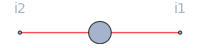
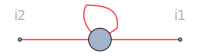
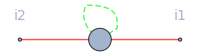
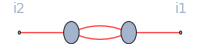
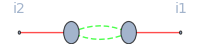
-Graphics-∂_t ^-1= | -Graphics--1/2^ | -Graphics-+^ | -Graphics--1/2^ | -Graphics-+^

```mathematica
doRGE[action,{A,A},tDerivative->False]
RGEPlot[%,fieldRules]
```

1/2 op[dR[{A,r1},{A,s1}],P[{A,t1},{A,r1}],P[{A,s1},{A,u1}],V[{A,i1},{A,i2},{A,t1},{A,u1}]]-op[dR[{cb,r1},{c,s1}],P[{c,t1},{cb,r1}],P[{c,s1},{cb,u1}],V[{A,i1},{A,i2},{cb,u1},{c,t1}]]-op[dR[{A,r1},{A,s1}],P[{A,t1},{A,r1}],P[{A,s1},{A,u1}],V[{A,i2},{A,u1},{A,v1}],P[{A,v1},{A,w1}],V[{A,i1},{A,t1},{A,w1}]]+2 op[dR[{cb,r1},{c,s1}],P[{c,t1},{cb,r1}],P[{c,s1},{cb,u1}],V[{A,i2},{cb,u1},{c,v1}],P[{c,v1},{cb,w1}],V[{A,i1},{cb,w1},{c,t1}]]

-Graphics-∂_t ^-1= | -Graphics-+1/2^ | -Graphics--^ | -Graphics--^ | -Graphics-+2^

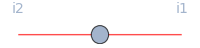
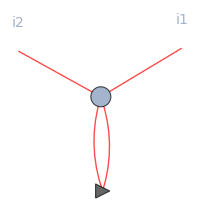
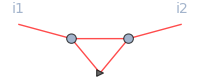
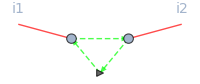
-Graphics-∂_t ^-1= | -Graphics-+1/2^ | -Graphics-+^ | -Graphics--2^ |

```mathematica
doRGE[action,{A,A},tDerivative->True]
RGEPlot[%,fieldRules,regulatorSymbol->triangleSymbol]
```

Ghost propagator
WORKS

```mathematica
doRGE[action,{cb,c},tDerivative->False]
RGEPlot[%,fieldRules]
```

-1/2 op[P[{A,r1},{A,s1}],V[{A,r1},{A,s1},{cb,i1},{c,i2}]]-op[P[{c,r1},{cb,s1}],V[{cb,i1},{cb,s1},{c,i2},{c,r1}]]+op[P[{A,r1},{A,s1}],V[{A,s1},{cb,t1},{c,i2}],P[{c,u1},{cb,t1}],V[{A,r1},{cb,i1},{c,u1}]]

-Graphics-∂_t ^-1= | -Graphics--1/2^ | -Graphics--^ | -Graphics-+^ |

-Graphics-∂_t ^-1= | -Graphics-+1/2^ | -Graphics-+^ | -Graphics-+^ |

Change order of external derivatives:

```mathematica
doRGE[action,{c,cb},tDerivative->False]
RGEPlot[%,fieldRules]
```

-1/2 op[P[{A,r1},{A,s1}],V[{A,r1},{A,s1},{cb,i2},{c,i1}]]-op[P[{c,r1},{cb,s1}],V[{cb,i2},{cb,s1},{c,i1},{c,r1}]]-op[P[{A,r1},{A,s1}],V[{A,s1},{cb,i2},{c,t1}],P[{c,t1},{cb,u1}],V[{A,r1},{cb,u1},{c,i1}]]

-Graphics-∂_t ^-1= | -Graphics--1/2^ | -Graphics--^ | -Graphics--^ |

#### AA step by step

```mathematica
action={{A,A},{c,cb},{A,cb,c},{A,A,A},{A,A,A,A},{A,A,cb,c},{cb,cb,c,c},{A,A,A,cb,c},{cb,cb,c,c,A},{A,A,A,A,A}};
```

```mathematica
fieldRules={{A,Red},{c,Green,Dashing[{0.02,0.01}]}};
```

```mathematica
setFields[{A},{{c,cb}}]
```

```mathematica
orderedDerivs={{A,i},{A,j}};
```

```mathematica
$signConvention=-1;
```

```mathematica
$signConvention=1;
```

```mathematica
onePoint=1/2 op[sf[First@orderedDerivs,{{$dummyField,traceIndex1},{$dummyField,ind}}],P[{$dummyField,traceIndex1},{$dummyField,ind}],-$signConvention V[First@orderedDerivs,{$dummyField,ind},{$dummyField,traceIndex2}]]
```

1/2 op[P[{ϕ,traceIndex1},{ϕ,ind}],V[{A,i},{ϕ,ind},{ϕ,traceIndex2}]]

```mathematica
RGEPlot[onePoint/.traceIndex2:>traceIndex1,fieldRules,output->forceEquation]
```

-Graphics-∂_t ^= | -Graphics-+1/2^-1 |  |  |

-Graphics-∂_t ^= | -Graphics--1/2^-1 |  |  |

```mathematica
twoPoint=derivRGE[onePoint,orderedDerivs[[2]]]
```

1/2 op[P[{ϕ,traceIndex1},{ϕ,ind}],V[{A,j},{A,i},{ϕ,ind},{ϕ,traceIndex2}]]-1/2 op[P[{ϕ,traceIndex1},{ϕ,dummy[39]}],V[{A,j},{ϕ,dummy[39]},{ϕ,dummy[40]}],P[{ϕ,dummy[40]},{ϕ,ind}],V[{A,i},{ϕ,ind},{ϕ,traceIndex2}]]

```mathematica
RGEPlot[twoPoint/.traceIndex2:>traceIndex1/.sf[_,_]:>1,fieldRules]
```

-Graphics-∂_t ^-1= | -Graphics-+1/2^ | -Graphics--1/2^ |  |

-Graphics-∂_t ^-1= | -Graphics--1/2^ | -Graphics--1/2^ |  |

```mathematica
twoPointS0=setSourcesZeroRGE[twoPoint/.traceIndex2:>traceIndex1,action,orderedDerivs,{{A,A},{c,cb}}];
```

```mathematica
RGEPlot[twoPointS0,fieldRules]
```

-Graphics-∂_t ^-1= | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--1/2^ |  |

-Graphics-∂_t ^-1= | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--1/2^ |  |

```mathematica
twoPointS02=twoPointS0/.P[{f1_?grassmannQ,traceIndex1},{f2_,i2_}]:>-P[{f1,traceIndex1},{f2,i2}];
```

```mathematica
RGEPlot[twoPointS02,fieldRules]
```

-Graphics-∂_t ^-1= | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--1/2^ |  |

-Graphics-∂_t ^-1= | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--1/2^ |  |

```mathematica
twoPointS03=getSigns[twoPointS02];
```

```mathematica
RGEPlot[twoPointS03,fieldRules]
```

-Graphics-∂_t ^-1= | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--1/2^ |  |

-Graphics-∂_t ^-1= | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--1/2^ |  |

```mathematica
twoPointS04=identifyGraphs[twoPointS03,orderedDerivs];
```

```mathematica
RGEPlot[twoPointS04,fieldRules]
```

-Graphics-∂_t ^-1= | -Graphics-+1/2^ | -Graphics-+^ | -Graphics--1/2^ | -Graphics--^

-Graphics-∂_t ^-1= | -Graphics--1/2^ | -Graphics--^ | -Graphics--1/2^ | -Graphics--^

```mathematica
AA=doRGE[action,{A,A},tDerivative->False];
RGEPlot[AA,fieldRules]
```

-Graphics-∂_t ^-1= | -Graphics-+1/2^ | -Graphics--^ | -Graphics--1/2^ | -Graphics-+^

-Graphics-∂_t ^-1= | -Graphics--1/2^ | -Graphics-+^ | -Graphics--1/2^ | -Graphics-+^

#### AAA step by step

```mathematica
action={{A,A},{c,cb},{A,cb,c},{A,A,A},{A,A,A,A},{A,A,cb,c},{cb,cb,c,c},{A,A,A,cb,c},{cb,cb,c,c,A},{A,A,A,A,A}};
```

```mathematica
fieldRules={{A,Red},{c,Green,Dashing[{0.02,0.01}]}};
```

```mathematica
setFields[{A},{{c,cb}}]
```

```mathematica
orderedDerivs={{A,i},{A,j},{A,l}};
```

```mathematica
$signConvention=-1;
```

```mathematica
$signConvention=1;
```

```mathematica
onePoint=1/2 op[sf[First@orderedDerivs,{{$dummyField,traceIndex1},{$dummyField,ind}}],P[{$dummyField,traceIndex1},{$dummyField,ind}],-$signConvention V[First@orderedDerivs,{$dummyField,ind},{$dummyField,traceIndex2}]]
```

1/2 op[P[{ϕ,traceIndex1},{ϕ,ind}],V[{A,i},{ϕ,ind},{ϕ,traceIndex2}]]

```mathematica
RGEPlot[onePoint/.traceIndex2:>traceIndex1,fieldRules,output->forceEquation]
```

-Graphics-∂_t ^= | -Graphics-+1/2^-1 |  |  |

-Graphics-∂_t ^= | -Graphics--1/2^-1 |  |  |

```mathematica
twoPoint=derivRGE[onePoint,orderedDerivs[[2]]]
```

1/2 op[P[{ϕ,traceIndex1},{ϕ,ind}],V[{A,j},{A,i},{ϕ,ind},{ϕ,traceIndex2}]]-1/2 op[P[{ϕ,traceIndex1},{ϕ,dummy[1]}],V[{A,j},{ϕ,dummy[1]},{ϕ,dummy[2]}],P[{ϕ,dummy[2]},{ϕ,ind}],V[{A,i},{ϕ,ind},{ϕ,traceIndex2}]]

```mathematica
RGEPlot[twoPoint/.traceIndex2:>traceIndex1/.sf[_,_]:>1,fieldRules]
```

-Graphics-∂_t ^-1= | -Graphics-+1/2^ | -Graphics--1/2^ |  |

```mathematica
threePoint=derivRGE[twoPoint,orderedDerivs[[3]]];
```

```mathematica
RGEPlot[threePoint/.traceIndex2:>traceIndex1,fieldRules]
```

-Graphics-∂_t ^= | -Graphics-+1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics-+1/2^ | -Graphics-+1/2^ |  |

-Graphics-∂_t ^= | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--1/2^ |  |

```mathematica
threePointS0=setSourcesZeroRGE[threePoint/.traceIndex1:>traceIndex2,action,orderedDerivs,{{A,A},{c,cb}}];
```

```mathematica
RGEPlot[threePointS0,fieldRules]
```

-Graphics-∂_t ^= | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^
 | -Graphics-+1/2^ | -Graphics-+1/2^ |  |

-Graphics-∂_t ^= | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--1/2^ |  |

```mathematica
$
```

```mathematica
threePointS02=threePointS0/.P[{f1_?grassmannQ,traceIndex2},{f2_,i2_}]:>-P[{f1,traceIndex2},{f2,i2}];
```

```mathematica
RGEPlot[threePointS02,fieldRules]
```

-Graphics-∂_t ^= | -Graphics-+1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^
 | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^
 | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--1/2^ |  |

-Graphics-∂_t ^= | -Graphics--1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^
 | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^
 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^
 | -Graphics-+1/2^ | -Graphics-+1/2^ |  |

```mathematica
threePointS03=getSigns[threePointS02];
```

```mathematica
RGEPlot[threePointS03,fieldRules]
```

-Graphics-∂_t ^= | -Graphics-+1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^
 | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^
 | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--1/2^ |  |

-Graphics-∂_t ^= | -Graphics--1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^
 | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^
 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^
 | -Graphics-+1/2^ | -Graphics-+1/2^ |  |

```mathematica
threePointS04=-$signConvention identifyGraphs[threePointS03,orderedDerivs];
```

```mathematica
RGEPlot[threePointS04,fieldRules]
```

-Graphics-∂_t ^= | -Graphics-+1/2^ | -Graphics--^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+^
 | -Graphics-+^ | -Graphics--^ | -Graphics--^ |

-Graphics-∂_t ^= | -Graphics-+1/2^ | -Graphics--^ | -Graphics-+1/2^ | -Graphics-+1/2^
 | -Graphics-+1/2^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics-+^ | -Graphics--^ | -Graphics--^ |

```mathematica
RGEPlot[X1,fieldRules]
```

-Graphics-∂_t ^= | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^
 | -Graphics-+1/2^ | -Graphics-+1/2^ |  |

```mathematica
RGEPlot[X2,fieldRules]
```

-Graphics-∂_t ^= | -Graphics-+1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^
 | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^
 | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--1/2^ |  |

```mathematica
RGEPlot[X3,fieldRules]
```

-Graphics-∂_t ^= | -Graphics-+1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^
 | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^
 | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--1/2^ |  |

```mathematica
RGEPlot[X4,fieldRules]
```

-Graphics-∂_t ^= | -Graphics-+1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics-+^ | -Graphics-+^
 | -Graphics-+^ | -Graphics-+^ | -Graphics--^ | -Graphics--^

```mathematica
AAA=doRGE[action,{A,A,A},tDerivative->False];
RGEPlot[AAA,fieldRules]
```

-Graphics-∂_t ^= | -Graphics-+1/2^ | -Graphics--^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+^
 | -Graphics-+^ | -Graphics--^ | -Graphics--^ |

-Graphics-∂_t ^= | -Graphics-+1/2^ | -Graphics--^ | -Graphics-+1/2^ | -Graphics-+1/2^
 | -Graphics-+1/2^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics-+^ | -Graphics--^ | -Graphics--^ |

#### AA

```mathematica
AA=doRGE[action,{A,A},tDerivative->False];
RGEPlot[AA,fieldRules]
```

-Graphics-∂_t ^-1= | -Graphics-+1/2^ | -Graphics--^ | -Graphics--1/2^ | -Graphics-+^

```mathematica
AA=doRGE[action,{A,A},tDerivative->True];
RGEPlot[AA,fieldRules]
```

-Graphics-∂_t ^-1= | -Graphics--1/2^ | -Graphics-+^ | -Graphics-+^ | -Graphics--2^

#### AAA

Three-gluon vertex
WORKS

```mathematica
AAA=doRGE[action,{A,A,A},tDerivative->False];
RGEPlot[AAA,fieldRules]
```

-Graphics-∂_t ^= | -Graphics-+1/2^ | -Graphics--^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+^
 | -Graphics-+^ | -Graphics--^ | -Graphics--^ |

```mathematica
AAA=doRGE[action,{A,A,A},tDerivative->True];
RGEPlot[AAA,fieldRules]
```

-Graphics-∂_t ^= | -Graphics--1/2^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+^
 | -Graphics-+^ | -Graphics--2^ | -Graphics--2^ | -Graphics--2^
 | -Graphics--^ | -Graphics-+^ | -Graphics-+^ | -Graphics--^
 | -Graphics--^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+^
 | -Graphics-+^ |  |  |

#### AAAA

Four-gluon vertex
WORKS

```mathematica
doRGE[action,{A,A,A,A},tDerivative->False];
RGEPlot[%,fieldRules]
```

-Graphics-∂_t ^= | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics-+^ | -Graphics-+^
 | -Graphics-+^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+^
 | -Graphics--2^ | -Graphics--2^ | -Graphics--2^ | -Graphics--2^
 | -Graphics--2^ | -Graphics--2^ | -Graphics-+^ | -Graphics-+^
 | -Graphics-+^ | -Graphics--2^ | -Graphics--2^ | -Graphics--2^

#### Acbc

Ghost-gluon vertex
WORKS

```mathematica
doRGE[action,{A,cb,c},tDerivative->False];
RGEPlot[%,fieldRules]
```

-Graphics-∂_t ^= | -Graphics--1/2^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--1/2^ | -Graphics--^ | -Graphics--^ | -Graphics--^

```mathematica
doRGE[action,{A,c,cb},tDerivative->False];
RGEPlot[%,fieldRules]
```

-Graphics-∂_t ^= | -Graphics-+1/2^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+^
 | -Graphics-+1/2^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+^

```mathematica
doRGE[action,{c,cb,A},tDerivative->False];
RGEPlot[%,fieldRules]
```

-Graphics-∂_t ^= | -Graphics-+1/2^ | -Graphics-+^ | -Graphics-+1/2^ | -Graphics-+^
 | -Graphics-+^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+^

```mathematica
doRGE[action,{cb,c,A},tDerivative->False];
RGEPlot[%,fieldRules]
```

-Graphics-∂_t ^= | -Graphics--1/2^ | -Graphics--^ | -Graphics--1/2^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^

#### Acbc step by step

```mathematica
action={{A,A},{c,cb},{A,cb,c},{A,A,A},{A,A,A,A},{A,A,cb,c},{cb,cb,c,c},{A,A,A,cb,c},{cb,cb,c,c,A}};
```

```mathematica
fieldRules={{A,Red},{c,Green,Dashing[{0.02,0.01}]}};
```

```mathematica
setFields[{A},{{c,cb}}]
```

```mathematica
orderedDerivs={{A,i},{cb,j},{c,k}};
```

```mathematica
onePoint=1/2 op[sf[First@orderedDerivs,{{$dummyField,traceIndex1},{$dummyField,ind}}],P[{$dummyField,traceIndex1},{$dummyField,ind}],-$signConvention V[First@orderedDerivs,{$dummyField,ind},{$dummyField,traceIndex2}]]
```

1/2 op[P[{ϕ,traceIndex1},{ϕ,ind}],V[{A,i},{ϕ,ind},{ϕ,traceIndex2}]]

```mathematica
RGEPlot[onePoint/.traceIndex2:>traceIndex1,fieldRules,output->forceEquation]
```

-Graphics-∂_t ^= | -Graphics-+1/2^-1 |  |  |

```mathematica
twoPoint=derivRGE[onePoint,orderedDerivs[[2]]]
```

1/2 op[P[{ϕ,traceIndex1},{ϕ,ind}],sf[{cb,j},{{ϕ,traceIndex1},{ϕ,ind}}],V[{cb,j},{A,i},{ϕ,ind},{ϕ,traceIndex2}]]-1/2 op[sf[{cb,j},{{ϕ,traceIndex1},{ϕ,dummy[124]}}],P[{ϕ,traceIndex1},{ϕ,dummy[124]}],V[{cb,j},{ϕ,dummy[124]},{ϕ,dummy[125]}],P[{ϕ,dummy[125]},{ϕ,ind}],V[{A,i},{ϕ,ind},{ϕ,traceIndex2}]]

```mathematica
RGEPlot[twoPoint/.traceIndex2:>traceIndex1/.sf[_,_]:>1,fieldRules]
```

-Graphics-∂_t ^-1= | -Graphics-+1/2^ | -Graphics--1/2^ |  |

```mathematica
threePoint=derivRGE[twoPoint,orderedDerivs[[3]]]
```

-1/2 op[P[{ϕ,traceIndex1},{ϕ,ind}],sf[{cb,j},{{ϕ,traceIndex1},{ϕ,ind}}],sf[{c,k},{{ϕ,traceIndex1},{ϕ,ind}}],V[{c,k},{cb,j},{A,i},{ϕ,ind},{ϕ,traceIndex2}]]-1/2 op[sf[{c,k},{{ϕ,traceIndex1},{ϕ,dummy[3]}}],P[{ϕ,traceIndex1},{ϕ,dummy[3]}],V[{c,k},{ϕ,dummy[3]},{ϕ,dummy[4]}],P[{ϕ,dummy[4]},{ϕ,ind}],sf[{cb,j},{{ϕ,traceIndex1},{ϕ,ind}}],V[{cb,j},{A,i},{ϕ,ind},{ϕ,traceIndex2}]]-1/2 op[sf[{cb,j},{{ϕ,traceIndex1},{ϕ,dummy[1]}}],P[{ϕ,traceIndex1},{ϕ,dummy[1]}],sf[{c,k},{{ϕ,traceIndex1},{ϕ,dummy[1]}}],V[{c,k},{cb,j},{ϕ,dummy[1]},{ϕ,dummy[2]}],P[{ϕ,dummy[2]},{ϕ,ind}],V[{A,i},{ϕ,ind},{ϕ,traceIndex2}]]-1/2 op[sf[{cb,j},{{ϕ,traceIndex1},{ϕ,dummy[1]}}],P[{ϕ,traceIndex1},{ϕ,dummy[1]}],V[{cb,j},{ϕ,dummy[1]},{ϕ,dummy[2]}],P[{ϕ,dummy[2]},{ϕ,ind}],sf[{c,k},{{ϕ,traceIndex1},{cb,j},{ϕ,ind}}],V[{c,k},{A,i},{ϕ,ind},{ϕ,traceIndex2}]]-1/2 op[sf[{cb,j},{{ϕ,traceIndex1},{ϕ,dummy[1]}}],sf[{c,k},{{ϕ,traceIndex1},{ϕ,dummy[5]}}],P[{ϕ,traceIndex1},{ϕ,dummy[5]}],V[{c,k},{ϕ,dummy[5]},{ϕ,dummy[6]}],P[{ϕ,dummy[6]},{ϕ,dummy[1]}],V[{cb,j},{ϕ,dummy[1]},{ϕ,dummy[2]}],P[{ϕ,dummy[2]},{ϕ,ind}],V[{A,i},{ϕ,ind},{ϕ,traceIndex2}]]-1/2 op[sf[{cb,j},{{ϕ,traceIndex1},{ϕ,dummy[1]}}],P[{ϕ,traceIndex1},{ϕ,dummy[1]}],V[{cb,j},{ϕ,dummy[1]},{ϕ,dummy[2]}],sf[{c,k},{{ϕ,traceIndex1},{cb,j},{ϕ,dummy[2]}}],sf[{c,k},{{ϕ,dummy[2]},{ϕ,dummy[7]}}],P[{ϕ,dummy[2]},{ϕ,dummy[7]}],V[{c,k},{ϕ,dummy[7]},{ϕ,dummy[8]}],P[{ϕ,dummy[8]},{ϕ,ind}],V[{A,i},{ϕ,ind},{ϕ,traceIndex2}]]

```mathematica
RGEPlot[identifyGraphs[threePoint/.traceIndex2:>traceIndex1,orderedDerivs]/.sf[_,_]:>1,fieldRules]
```

-Graphics-∂_t ^= | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--^ |  |  |

```mathematica
threePointS0=setSourcesZeroRGE[threePoint/.traceIndex2:>traceIndex1,action,orderedDerivs,{{A,A},{c,cb}}];
```

All diagrams are there in the correct multiplicity.

```mathematica
RGEPlot[threePointS0/.sf[_,_]:>1,fieldRules]
```

-Graphics-∂_t ^= | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--1/2^ |  |

Add signs:
For closing the fermion loops, for reordering fermions, for sf’s.

```mathematica
threePointFinal=sortCanonical[threePointS0/.{P[a___,{c,traceIndex2},b___]:>-P[a,{c,traceIndex2},b],P[a___,{cb,traceIndex2},b___]:>-P[a,{cb,traceIndex2},b]}//orderFermions//getSigns,orderedDerivs];
```

```mathematica
threePointFinal=identifyGraphs[sortCanonical[threePointS0/.{P[a___,{c,traceIndex2},b___]:>-P[a,{c,traceIndex2},b],P[a___,{cb,traceIndex2},b___]:>-P[a,{cb,traceIndex2},b]}//orderFermions//getSigns,orderedDerivs],orderedDerivs];
```

```mathematica
RGEPlot[threePointFinal,fieldRules]
```

-Graphics-∂_t ^= | -Graphics-+1/2^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+1/2^
 | -Graphics-+^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+^

#### AAcbc

Two-ghost-two-gluon vertex
WORKS

```mathematica
AAcbc=doRGE[action,{A,A,cb,c},tDerivative->False];
RGEPlot[%,fieldRules]
```

-Graphics-∂_t ^= | -Graphics--1/2^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics--2^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^

```mathematica
getVertexNumbers[#]&/@List@@AAcbc
```

{{3,5},{3,5},{3,5},{4,4},{4,4},{4,4},{3,5},{3,5},{4,4},{3,5},{3,3,4},{3,3,4},{3,3,4},{3,3,4},{3,3,4},{3,3,4},{3,3,4},{3,3,4},{3,3,4},{3,3,4},{3,3,4},{3,3,4},{3,3,3,3},{3,3,3,3},{3,3,3,3},{3,3,3,3},{3,3,3,3},{3,3,3,3}}

Plot single groups:

```mathematica
RGEPlot[#,fieldRules]&/@groupDiagrams[AAcbc][[All,2]]
```

{-Graphics-∂_t ^= | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ |  | ,-Graphics-∂_t ^= | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--2^ | -Graphics--^ | -Graphics--^ | -Graphics--^,-Graphics-∂_t ^= | -Graphics--^ | -Graphics--^ | -Graphics--1/2^ | -Graphics--^,-Graphics-∂_t ^= | -Graphics--1/2^ | -Graphics--^ | -Graphics--^ | -Graphics--1/2^
 | -Graphics--^ | -Graphics--^ |  | }

#### cbcbcc

Four-ghost vertex
WORKS

Reduced action:

```mathematica
action={{A,A},{c,cb},{A,cb,c},{cb,cb,c,c}};
```

```mathematica
fieldRules={{A,Red},{c,Green,Dashing[{0.02,0.01}]}};
```

```mathematica
setFields[{A},{{c,cb}}]
```

```mathematica
cbcbcc=doRGE[action,{{c,i},{c,j},{cb,k},{cb,l}},tDerivative->False];
RGEPlot[%,fieldRules]
```

-Graphics-∂_t ^= | -Graphics--1/2^ | -Graphics--^ | -Graphics-+^ | -Graphics-+^
 | -Graphics--^ | -Graphics-+^ | -Graphics-+^ | -Graphics--^
 | -Graphics-+^ | -Graphics-+^ | -Graphics--^ | -Graphics-+^
 | -Graphics--^ |  |  |

With reduced action:

-Graphics-∂_t ^= | -Graphics--1/2^ | -Graphics--^ | -Graphics-+^ | -Graphics-+^
 | -Graphics--^ | -Graphics-+^ | -Graphics-+^ | -Graphics--^
 | -Graphics-+^ | -Graphics-+^ | -Graphics--^ | -Graphics-+^
 | -Graphics--^ |  |  |

Plot single groups:

```mathematica
RGEPlot[#,fieldRules]&/@groupDiagrams[cbcbcc][[All,2]]
```

{-Graphics-∂_t ^= | -Graphics-+^ | -Graphics--^ | -Graphics-+^ | -Graphics--^,-Graphics-∂_t ^= | -Graphics-+^ | -Graphics--^ | -Graphics-+^ | -Graphics-+^
 | -Graphics--^ | -Graphics-+^ |  | ,-Graphics-∂_t ^= | -Graphics--1/2^ | -Graphics--^ | -Graphics-+^ | }

#### cbcbcc step by step

Step by step:

```mathematica
orderedDerivs={{c,i},{c,j},{cb,k},{cb,l}};
```

```mathematica
onePoint=1/2 op[sf[First@orderedDerivs,{{$dummyField,traceIndex1},{$dummyField,ind}}],P[{$dummyField,traceIndex1},{$dummyField,ind}],-V[First@orderedDerivs,{$dummyField,ind},{$dummyField,traceIndex2}]]
```

-1/2 op[sf[{c,i},{{ϕ,traceIndex1},{ϕ,ind}}],P[{ϕ,traceIndex1},{ϕ,ind}],V[{c,i},{ϕ,ind},{ϕ,traceIndex2}]]

```mathematica
RGEPlot[onePoint/.traceIndex2:>traceIndex1/.sf[_,_]:>1,fieldRules,output->forceEquation]
```

-Graphics-∂_t ^= | -Graphics--1/2^-1 |  |  |

```mathematica
twoPoint=derivRGE[onePoint,orderedDerivs[[2]]]
```

-1/2 op[sf[{c,i},{{ϕ,traceIndex1},{ϕ,ind}}],P[{ϕ,traceIndex1},{ϕ,ind}],sf[{c,j},{{ϕ,traceIndex1},{ϕ,ind}}],V[{c,j},{c,i},{ϕ,ind},{ϕ,traceIndex2}]]-1/2 op[sf[{c,i},{{ϕ,traceIndex1},{ϕ,ind}}],sf[{c,j},{{ϕ,traceIndex1},{ϕ,dummy[103]}}],P[{ϕ,traceIndex1},{ϕ,dummy[103]}],V[{c,j},{ϕ,dummy[103]},{ϕ,dummy[104]}],P[{ϕ,dummy[104]},{ϕ,ind}],V[{c,i},{ϕ,ind},{ϕ,traceIndex2}]]

```mathematica
RGEPlot[twoPoint/.traceIndex2:>traceIndex1/.sf[_,_]:>1,fieldRules]
```

-Graphics-∂_t ^-1= | -Graphics--1/2^ | -Graphics--1/2^ |  |

```mathematica
threePoint=derivRGE[twoPoint,orderedDerivs[[3]]];
```

```mathematica
RGEPlot[identifyGraphs[threePoint/.traceIndex2:>traceIndex1,orderedDerivs]/.sf[_,_]:>1,fieldRules]
```

-Graphics-∂_t ^= | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--^ |  |  |

```mathematica
fourPoint=derivRGE[threePoint,orderedDerivs[[4]]];
```

```mathematica
RGEPlot[identifyGraphs[fourPoint/.traceIndex2:>traceIndex1,orderedDerivs]/.sf[_,_]:>1,fieldRules]
```

-Graphics-∂_t ^= | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ |  |  |

```mathematica
fourPointS0=setSourcesZeroRGE[fourPoint,action,orderedDerivs,{{A,A},{c,cb}}];
```

```mathematica
RGEPlot[fourPointS0/.traceIndex2:>traceIndex1/.sf[_,_]:>1,fieldRules]
```

-Graphics-∂_t ^= | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ |  |  |

```mathematica
fourPointS0Signs=orderFermions[fourPointS0]/.{P[a___,{c,traceIndex2},b___]:>-P[a,{c,traceIndex2},b],P[a___,{cb,traceIndex2},b___]:>-P[a,{cb,traceIndex2},b]}//getSigns;
```

```mathematica
fourPointS0SignsId=identifyGraphs[sortCanonical[fourPointS0Signs,orderedDerivs],orderedDerivs];
```

```mathematica
RGEPlot[fourPointS0SignsId,fieldRules]
```

-Graphics-∂_t ^= | -Graphics-+^ | -Graphics--^ | -Graphics--1/2^ | -Graphics--^
 | -Graphics--^ | -Graphics-+^ | -Graphics-+^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics-+^ | -Graphics--^
 | -Graphics-+^ |  |  |

### Examples which made problems in the past

#### Four-point 1

Two triangle diagrams with equally oriented fermion lines are missing.

```mathematica
action={{psi,psibar},{A,A},{A,psibar,psi},{psibar,psibar,psi,psi}};
```

```mathematica
setFields[{A},{{psi,psibar}}];
```

```mathematica
fS={{A,Red},{psi,Blue}};
```

```mathematica
tp=doRGE[action,{psibar,psi},tDerivative->False];
```

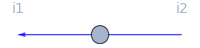
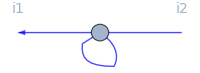
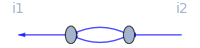
-Graphics-∂_t ^-1= | -Graphics-+^ | -Graphics-+^ |  |

```mathematica
RGEPlot[tp,fS]
```

```mathematica
fp=doRGE[action,{psi,psi,psibar,psibar},tDerivative->False];
```

```mathematica
RGEPlot[#,fS,ImageSize->100]&/@groupDiagrams[fp][[All,2]]
```

{-Graphics-∂_t ^= | -Graphics-+^ | -Graphics--^ | -Graphics-+^ | -Graphics--^,-Graphics-∂_t ^= | -Graphics-+^ | -Graphics--^ | -Graphics-+^ | -Graphics-+^
 | -Graphics--^ | -Graphics-+^ |  | ,-Graphics-∂_t ^= | -Graphics--1/2^ | -Graphics--^ | -Graphics-+^ | }

Expected result:

-Graphics-∂_t ^= | -Graphics--^ | -Graphics-+^ | -Graphics--1/2^ | -Graphics-+^
 | -Graphics--^ | -Graphics-+^ | -Graphics--^ | -Graphics--^
 | -Graphics-+^ | -Graphics-+^ | -Graphics--^ | -Graphics-+^
 | -Graphics--^ |  |  |

Original result before bugfix in 2.0:

-Graphics-∂_t ^= | -Graphics--^ | -Graphics-+^ | -Graphics--1/2^ | -Graphics-+^
 | -Graphics--^ | -Graphics--^ | -Graphics-+^ | -Graphics-+^
 | -Graphics--^ | -Graphics-+^ | -Graphics--^ |

#### Four-point 2

```mathematica
action={{b,b},{f,fBar},{f,fBar,b}, {f,f,fBar,fBar}};
```

```mathematica
setFields[{b},{{f,fBar}}];
```

```mathematica
fS={{f,Blue},{b,Red}};
```

```mathematica
fffbfb=doRGE[action,{fBar,fBar,f,f},tDerivative->False];
RGEPlot[fbfbff,fS,11,ImageSize->100]
```

-Graphics-∂_t ^= | -Graphics--^ | -Graphics-+^ | -Graphics--1/2^ | -Graphics-+^ | -Graphics-+^ | -Graphics--^ | -Graphics--^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+^
 | -Graphics--^ | -Graphics-+^ | -Graphics--^ |  |  |  |  |  |  |

```mathematica
fbfbff=doRGE[action,{f,f,fBar,fBar},tDerivative->False];
RGEPlot[fbfbff,fS,11]
```

-Graphics-∂_t ^= | -Graphics--1/2^ | -Graphics--^ | -Graphics-+^ | -Graphics-+^ | -Graphics--^ | -Graphics-+^ | -Graphics-+^ | -Graphics--^ | -Graphics-+^ | -Graphics-+^
 | -Graphics--^ | -Graphics-+^ | -Graphics--^ |  |  |  |  |  |  |

```mathematica
fbfbff=doRGE[action,{{fBar,a1},{fBar,a2},{f,a3},{f,a4}},tDerivative->False];
RGEPlot[fbfbff,fS,11]
```

-Graphics-∂_t ^= | -Graphics--^ | -Graphics-+^ | -Graphics--1/2^ | -Graphics-+^ | -Graphics-+^ | -Graphics--^ | -Graphics--^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+^
 | -Graphics--^ | -Graphics-+^ | -Graphics--^ |  |  |  |  |  |  |

Expected result:

-Graphics-∂_t ^= | -Graphics--^ | -Graphics-+^ | -Graphics--1/2^ | -Graphics--^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+^ | -Graphics--^ | -Graphics-+^ | -Graphics-+^
 | -Graphics--^ | -Graphics-+^ | -Graphics--^ |  |  |  |  |  |  |

### Four fermion 3

```mathematica
(*<<DoFun`;*)
<<FormTracer`;
SetDirectory[NotebookDirectory[]];
```

FormTracer 2.3.5 loaded.

Copyright (C) 2013-2018, Anton K. Cyrol, Mario Mitter, Jan M. Pawlowski, and Nils Strodthoff.
FormTracer is released under the GNU General Public License version three or later.

If used in scientific publications, please acknowledge our work by citing:
A. K. Cyrol, M. Mitter, and N. Strodthoff, Comput. Phys. Commun. 219C (2017) 346-352, arXiv:1610.09331 [hep-ph]

FormTracer version 2.3.6 is available. You are currently using version 2.3.5.
You can update the FormTracer by evaluating UpdateFormTracer[]. The changelog is available from ShowFormTracerChangeLog[].

Using FORM 4.2.0 (Jul  6 2017, v4.2.0) 64-bits.

```mathematica
setFields[{A},{{psi,psib}}];
```

```mathematica
DefineLorentzTensors[deltaLorentz[mu,nu],vec[p,mu],sp[p,q],eps[],deltaDirac[i,j],gamma[mu,i,j],gamma5[i,j]];
DefineExtraVars[Zpsi,Z1,gBar,ZA,chi,ZMinus,lambdaBarMinus,ZPlus,lambdaBarPlus,Zsigma,lambdaBarsigma,ZVA,lambdaBarVA,Rpsi,RA,dRpsi,dRA,rpsi,rA,k];
defineFieldsSpecific[{{psi[momentum,dirac,FundFlav,FundCol],psib[momentum,dirac,FundFlav,FundCol]},A[momentum,lorentz,adjCol]}];
DefineLorentzDimensions[4,4]
DefineGroupTensors[{
{SUNfund,{flavor,Nf},delta[adjFlav,a,b],SUNFF[a,b,c],delta[FundFlav,a,b],SUNTF[a,i,j]},
{SUNfund,{color,Nc},delta[adjCol,a,b],SUNF[a,b,c],delta[FundCol,a,b],SUNT[a,i,j]}
}]
ShowGroupConstants[]
```

| type | NR | cR | NA | cA | I2R
flavor(f) | SUNfund | Nf | (-1+Nf^2)/(2 Nf) | -1+Nf^2 | Nf | 1/2
color(c) | SUNfund | Nc | (-1+Nc^2)/(2 Nc) | -1+Nc^2 | Nc | 1/2

```mathematica
addIndices[{dirac,{h,i,j,k,l,m,n,o,d1,d2,d3,d4,d5,d6,d7,d8}}];
addIndices[{lorentz,{mu,mu1,mu2,mu3,mu4,mu5,mu6,mu7,mu8}}];
addIndices[{FundFlav,{f1,f2,f3,f4,f5,f6,f7,f8}}];
addIndices[{FundCol,{c1,c2,c3,c4,c5,c6,c7,c8}}];
addIndices[{adjCol,{ca1,ca2,ca3,ca4,ca5,ca6,ca7,ca8}}];
```

Derive Flow Equations:

```mathematica
PL[p_,mu1_,mu2_]:=Module[{},vec[p,mu1]vec[p,mu2]/sp[p,p]];
PT[p_,mu1_,mu2_]:=Module[{},deltaLorentz[mu1,mu2]-vec[p,mu1]vec[p,mu2]/sp[p,p]];
```

```mathematica
action=convertAction[
-vec[q,mu]gamma[mu,d1,d2] Zpsi op[psib[q,d1,f1,c1],psi[q,d2,f1,c1]](*kinetic psi*)+
 Rpsi[q,k,d1,d2,f1,f2,c1,c2] op[psib[q,d1,f1,c1],psi[q,d2,f2,c2]](*Fermion regulator*)+
Z1*gBar* gamma[mu1,d1,d2]SUNT[ca1,c1,c2] delta[FundFlav,f1,f2]op[psib[q1,d1,f1,c1],psi[q1-q2,d2,f2,c2],A[q2,mu1,ca1]](*psi A coupling*)+
(1/2)*q^2*ZA PT[q,mu1,mu2]op[A[-q,mu1,ca1],A[q,mu2,ca1]](*kinetic A *)+
(1/(2chi))*q^2* PL[q,mu1,mu2]op[A[-q,mu1,ca1],A[q,mu2,ca1]](*gauge fixing *)+
(1/2)* RA[q,k,mu1,mu2,ca1,ca2]op[A[-q,mu1,ca1],A[q,mu2,ca2]](*gluon regulator*)+
(1/2)*(
ZMinus*lambdaBarMinus((gamma[mu1,d1,d2]gamma[mu1,d3,d4])+(gamma[mu2,d1,i]gamma5[i,d2]gamma[mu2,d3,j]gamma5[j,d4]))delta[FundFlav,f1,f2]delta[FundFlav,f3,f4]delta[FundCol,c1,c2]delta[FundCol,c3,c4](*V-A*)+
ZPlus*lambdaBarPlus((gamma[mu1,d1,d2]gamma[mu1,d3,d4])-(gamma[mu2,d1,k]gamma5[k,d2]gamma[mu2,d3,l]gamma5[l,d4]))delta[FundFlav,f1,f2]delta[FundFlav,f3,f4]delta[FundCol,c1,c2]delta[FundCol,c3,c4](*V+A*)+
Zsigma*lambdaBarsigma((deltaDirac[d1,d2]deltaDirac[d3,d4])-(gamma5[d1,d2]gamma5[d3,d4]))delta[FundFlav,f1,f4]delta[FundFlav,f2,f3]delta[FundCol,c1,c2]delta[FundCol,c3,c4](*S-P*)+
ZVA*lambdaBarVA(2((gamma[mu1,d1,d2]gamma[mu1,d3,d4]SUNT[ca1,c1,c2]SUNT[ca1,c3,c4])+(gamma[mu2,d1,m]gamma5[m,d2]gamma[mu2,d3,n]gamma5[n,d4]SUNT[ca2,c1,c2]SUNT[ca2,c3,c4]))(*(V-A)^adj*)
+(1/Nc)*((gamma[mu1,d1,d2]gamma[mu1,d3,d4])+(gamma[mu2,d1,o]gamma5[o,d2]gamma[mu2,d3,h]gamma5[h,d4]))delta[FundCol,c1,c2]delta[FundCol,c3,c4])delta[FundFlav,f1,f2]delta[FundFlav,f3,f4](*(V-A)*)
)op[psib[q1,d1,f1,c1],psi[q2,d2,f2,c2],psib[q3,d3,f3,c3],psi[q3+q1-q2,d4,f4,c4]]];
```

```mathematica
fourPoint=doRGE[action,{{psib,i1},{psib,i2},{psi,i3},{psi,i4}},tDerivative->False];
```

Have to change the order of derivatives here to get the correct sign as below. TODO Check if this is ok.

```mathematica
fourPoint=doRGE[action,{{psib,i1},{psi,i3},{psib,i2},{psi,i4}},tDerivative->False];
```

```mathematica
fieldStyle={{psi, Black},{psib,Black},{A,Red}};
```

```mathematica
RGEPlot[fourPoint,fieldStyle,output->forceEquation]
```

-Graphics-∂_t ^= | -Graphics-+^ | -Graphics--^ | -Graphics-+1/2^ | -Graphics--^
 | -Graphics--^ | -Graphics-+^ | -Graphics-+^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics-+^ | -Graphics--^
 | -Graphics-+^ |  |  |

To get the same RG equations as in the paper I have to change the sign in the following two diagrams:
DoFun 3.0: No change necessary.

```mathematica
(*fourPointTemp=List@@fourPoint;
fourPointTemp[[6]]=-fourPointTemp[[6]];
fourPointTemp[[9]]=-fourPointTemp[[9]];
fourPoint=Plus@@fourPointTemp;*)
```

```mathematica
RGEPlot[fourPoint,fieldStyle,output->forceEquation]
```

-Graphics-∂_t ^= | -Graphics-+^ | -Graphics--^ | -Graphics-+1/2^ | -Graphics--^
 | -Graphics--^ | -Graphics-+^ | -Graphics-+^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics-+^ | -Graphics--^
 | -Graphics-+^ |  |  |

Define propagators and vertices:

```mathematica
FR3PointPsiA=getFR[action,{psib[p1,d1,f1,c1],psi[p2,d2,f2,c2],A[p3,mu3,ca3]}]/deltam[-p1+p2+p3] 
FR4PointPsi=getFR[action,{psib[p1,d1,f1,c1],psib[p2,d2,f2,c2],psi[p3,d3,f3,c3],psi[p4,d4,f4,c4]}]/deltam[-p1-p2+p3+p4]/.delta[dirac,a_,b_]->deltaDirac[a,b]//FullSimplify
```

gBar Z1 delta[FundFlav,f1,f2] gamma[mu3,d1,d2] SUNT[ca3,c1,c2]

1/(2 Nc)(-delta[FundCol,c1,c4] delta[FundCol,c2,c3] (2 lambdaBarsigma Nc Zsigma delta[FundFlav,f1,f3] delta[FundFlav,f2,f4] (deltaDirac[d1,d4] deltaDirac[d2,d3]-gamma5[d1,d4] gamma5[d2,d3])+delta[FundFlav,f1,f4] delta[FundFlav,f2,f3] (2 (lambdaBarMinus Nc ZMinus+lambdaBarPlus Nc ZPlus+lambdaBarVA ZVA) gamma[mu1,d1,d4] gamma[mu1,d2,d3]+lambdaBarMinus Nc ZMinus (gamma[mu2,d1,i] gamma[mu2,d2,j] gamma5[i,d4] gamma5[j,d3]+gamma[mu2,d1,j] gamma[mu2,d2,i] gamma5[i,d3] gamma5[j,d4])-lambdaBarPlus Nc ZPlus (gamma[mu2,d1,k] gamma[mu2,d2,l] gamma5[k,d4] gamma5[l,d3]+gamma[mu2,d1,l] gamma[mu2,d2,k] gamma5[k,d3] gamma5[l,d4])+lambdaBarVA ZVA (gamma[mu2,d1,h] gamma[mu2,d2,o] gamma5[h,d4] gamma5[o,d3]+gamma[mu2,d1,o] gamma[mu2,d2,h] gamma5[h,d3] gamma5[o,d4])))+delta[FundCol,c1,c3] delta[FundCol,c2,c4] (2 lambdaBarsigma Nc Zsigma delta[FundFlav,f1,f4] delta[FundFlav,f2,f3] (deltaDirac[d1,d3] deltaDirac[d2,d4]-gamma5[d1,d3] gamma5[d2,d4])+delta[FundFlav,f1,f3] delta[FundFlav,f2,f4] (2 (lambdaBarMinus Nc ZMinus+lambdaBarPlus Nc ZPlus+lambdaBarVA ZVA) gamma[mu1,d1,d3] gamma[mu1,d2,d4]+lambdaBarMinus Nc ZMinus (gamma[mu2,d1,j] gamma[mu2,d2,i] gamma5[i,d4] gamma5[j,d3]+gamma[mu2,d1,i] gamma[mu2,d2,j] gamma5[i,d3] gamma5[j,d4])-lambdaBarPlus Nc ZPlus (gamma[mu2,d1,l] gamma[mu2,d2,k] gamma5[k,d4] gamma5[l,d3]+gamma[mu2,d1,k] gamma[mu2,d2,l] gamma5[k,d3] gamma5[l,d4])+lambdaBarVA ZVA (gamma[mu2,d1,o] gamma[mu2,d2,h] gamma5[h,d4] gamma5[o,d3]+gamma[mu2,d1,h] gamma[mu2,d2,o] gamma5[h,d3] gamma5[o,d4])))+2 lambdaBarVA Nc ZVA (-delta[FundFlav,f1,f4] delta[FundFlav,f2,f3] (2 gamma[mu1,d1,d4] gamma[mu1,d2,d3] SUNT[ca1,c1,c4] SUNT[ca1,c2,c3]+(gamma[mu2,d1,m] gamma[mu2,d2,n] gamma5[m,d4] gamma5[n,d3]+gamma[mu2,d1,n] gamma[mu2,d2,m] gamma5[m,d3] gamma5[n,d4]) SUNT[ca2,c1,c4] SUNT[ca2,c2,c3])+delta[FundFlav,f1,f3] delta[FundFlav,f2,f4] (2 gamma[mu1,d1,d3] gamma[mu1,d2,d4] SUNT[ca1,c1,c3] SUNT[ca1,c2,c4]+(gamma[mu2,d1,n] gamma[mu2,d2,m] gamma5[m,d4] gamma5[n,d3]+gamma[mu2,d1,m] gamma[mu2,d2,n] gamma5[m,d3] gamma5[n,d4]) SUNT[ca2,c1,c3] SUNT[ca2,c2,c4])))

```mathematica
P[psi[p1_,d1_,f1_,c1_],psib[p2_,d2_,f2_,c2_],explicit->True]:=Module[{mu},
-delta[FundCol,c1,c2] delta[FundFlav,f1,f2]vec[p1,mu]gamma[mu,d1,d2]/(p1^2*Zpsi*(1+rpsi))
]
P[A[p1_,mu1_,ca1_],A[p2_,mu2_,ca2_],explicit->True]:=Module[{},
delta[adjCol,ca1,ca2](deltaLorentz[mu1,mu2]-vec[p1,mu1] vec[p1,mu2]/p1^2)/(p1^2*ZA(1+rA))
]
V[A[p3_,mu3_,ca3_],psib[p1_,d1_,f1_,c1_],psi[p2_,d2_,f2_,c2_],explicit->True]:=
Module[{},
-gBar Z1 delta[FundFlav,f1,f2] gamma[mu3,d1,d2] SUNT[ca3,c1,c2]
]
V[psib[p1_,d1_,f1_,c1_],psib[p2_,d2_,f2_,c2_],psi[p3_,d3_,f3_,c3_],psi[p4_,d4_,f4_,c4_],explicit->True]:=Module[{i,mu2,j,mu1,ca1,ca2,m,n,h,k,l,o},
1/(2 Nc)(-delta[FundCol,c1,c4] delta[FundCol,c2,c3] (2 lambdaBarsigma Nc Zsigma delta[FundFlav,f1,f3] delta[FundFlav,f2,f4] (deltaDirac[d1,d4] deltaDirac[d2,d3]-gamma5[d1,d4] gamma5[d2,d3])+delta[FundFlav,f1,f4] delta[FundFlav,f2,f3] (2 (lambdaBarMinus Nc ZMinus+lambdaBarPlus Nc ZPlus+lambdaBarVA ZVA) gamma[mu1,d1,d4] gamma[mu1,d2,d3]+lambdaBarMinus Nc ZMinus (gamma[mu2,d1,i] gamma[mu2,d2,j] gamma5[i,d4] gamma5[j,d3]+gamma[mu2,d1,j] gamma[mu2,d2,i] gamma5[i,d3] gamma5[j,d4])-lambdaBarPlus Nc ZPlus (gamma[mu2,d1,k] gamma[mu2,d2,l] gamma5[k,d4] gamma5[l,d3]+gamma[mu2,d1,l] gamma[mu2,d2,k] gamma5[k,d3] gamma5[l,d4])+lambdaBarVA ZVA (gamma[mu2,d1,h] gamma[mu2,d2,o] gamma5[h,d4] gamma5[o,d3]+gamma[mu2,d1,o] gamma[mu2,d2,h] gamma5[h,d3] gamma5[o,d4])))+delta[FundCol,c1,c3] delta[FundCol,c2,c4] (2 lambdaBarsigma Nc Zsigma delta[FundFlav,f1,f4] delta[FundFlav,f2,f3] (deltaDirac[d1,d3] deltaDirac[d2,d4]-gamma5[d1,d3] gamma5[d2,d4])+delta[FundFlav,f1,f3] delta[FundFlav,f2,f4] (2 (lambdaBarMinus Nc ZMinus+lambdaBarPlus Nc ZPlus+lambdaBarVA ZVA) gamma[mu1,d1,d3] gamma[mu1,d2,d4]+lambdaBarMinus Nc ZMinus (gamma[mu2,d1,j] gamma[mu2,d2,i] gamma5[i,d4] gamma5[j,d3]+gamma[mu2,d1,i] gamma[mu2,d2,j] gamma5[i,d3] gamma5[j,d4])-lambdaBarPlus Nc ZPlus (gamma[mu2,d1,l] gamma[mu2,d2,k] gamma5[k,d4] gamma5[l,d3]+gamma[mu2,d1,k] gamma[mu2,d2,l] gamma5[k,d3] gamma5[l,d4])+lambdaBarVA ZVA (gamma[mu2,d1,o] gamma[mu2,d2,h] gamma5[h,d4] gamma5[o,d3]+gamma[mu2,d1,h] gamma[mu2,d2,o] gamma5[h,d3] gamma5[o,d4])))+2 lambdaBarVA Nc ZVA (-delta[FundFlav,f1,f4] delta[FundFlav,f2,f3] (2 gamma[mu1,d1,d4] gamma[mu1,d2,d3] SUNT[ca1,c1,c4] SUNT[ca1,c2,c3]+(gamma[mu2,d1,m] gamma[mu2,d2,n] gamma5[m,d4] gamma5[n,d3]+gamma[mu2,d1,n] gamma[mu2,d2,m] gamma5[m,d3] gamma5[n,d4]) SUNT[ca2,c1,c4] SUNT[ca2,c2,c3])+delta[FundFlav,f1,f3] delta[FundFlav,f2,f4] (2 gamma[mu1,d1,d3] gamma[mu1,d2,d4] SUNT[ca1,c1,c3] SUNT[ca1,c2,c4]+(gamma[mu2,d1,n] gamma[mu2,d2,m] gamma5[m,d4] gamma5[n,d3]+gamma[mu2,d1,m] gamma[mu2,d2,n] gamma5[m,d3] gamma5[n,d4]) SUNT[ca2,c1,c3] SUNT[ca2,c2,c4])))
]
```

Define Projectors:

```mathematica
Projector1[d1_,f1_,c1_,d2_,f2_,c2_,d3_,f3_,c3_,d4_,f4_,c4_]:=Module[{mu1,mu2,j,i},
delta[FundCol,c1,c4] delta[FundCol,c2,c3] delta[FundFlav,f1,f4] delta[FundFlav,f2,f3] gamma5[d3,d1] gamma5[d4,d2]
]
Projector2[d1_,f1_,c1_,d2_,f2_,c2_,d3_,f3_,c3_,d4_,f4_,c4_]:=Module[{mu1,mu2,j,i},
delta[FundCol,c1,c4] delta[FundCol,c2,c3] delta[FundFlav,f1,f4] delta[FundFlav,f2,f3] gamma[mu1,d4,d1] gamma[mu1,d3,d2]
]
Projector3[d1_,f1_,c1_,d2_,f2_,c2_,d3_,f3_,c3_,d4_,f4_,c4_]:=Module[{mu1,mu2,j,i},
 delta[FundCol,c1,c4] delta[FundCol,c2,c3] delta[FundFlav,f1,f3] delta[FundFlav,f2,f4] deltaDirac[d4,d1] deltaDirac[d3,d2]
]
Projector4[d1_,f1_,c1_,d2_,f2_,c2_,d3_,f3_,c3_,d4_,f4_,c4_]:=Module[{mu1,mu2,j,i,ca1,ca2},
 delta[FundFlav,f1,f4] delta[FundFlav,f2,f3] gamma[mu1,d4,d1] gamma[mu1,d3,d2]delta[FundCol,c1,c2] delta[FundCol,c3,c4]
]
```

```mathematica
list={FormTrace[V[psib[p1,d1,f1,c1],psib[p2,d2,f2,c2],psi[p3,d3,f3,c3],psi[p4,d4,f4,c4],explicit->True]Projector1[d1,f1,c1,d2,f2,c2,d3,f3,c3,d4,f4,c4]],
FormTrace[V[psib[p1,d1,f1,c1],psib[p2,d2,f2,c2],psi[p3,d3,f3,c3],psi[p4,d4,f4,c4],explicit->True]Projector2[d1,f1,c1,d2,f2,c2,d3,f3,c3,d4,f4,c4]],
FormTrace[V[psib[p1,d1,f1,c1],psib[p2,d2,f2,c2],psi[p3,d3,f3,c3],psi[p4,d4,f4,c4],explicit->True]Projector3[d1,f1,c1,d2,f2,c2,d3,f3,c3,d4,f4,c4]],
FormTrace[V[psib[p1,d1,f1,c1],psib[p2,d2,f2,c2],psi[p3,d3,f3,c3],psi[p4,d4,f4,c4],explicit->True]Projector4[d1,f1,c1,d2,f2,c2,d3,f3,c3,d4,f4,c4]]};
list//MatrixForm
```

(32 lambdaBarPlus Nc^2 Nf^2 ZPlus-16 lambdaBarsigma Nc Nf^2 Zsigma
-64 lambdaBarMinus Nc Nf ZMinus-64 lambdaBarMinus Nc^2 Nf^2 ZMinus-64 lambdaBarPlus Nc^2 Nf^2 ZPlus+32 lambdaBarsigma Nc Nf^2 Zsigma-64 lambdaBarVA Nc^2 Nf ZVA-64 lambdaBarVA Nc Nf^2 ZVA
32 lambdaBarPlus Nc Nf^2 ZPlus-16 lambdaBarsigma Nc^2 Nf^2 Zsigma
-64 lambdaBarMinus Nc Nf ZMinus-64 lambdaBarMinus Nc Nf^2 ZMinus-64 lambdaBarPlus Nc Nf^2 ZPlus+32 lambdaBarsigma Nc Nf^2 Zsigma-64 lambdaBarVA Nc Nf ZVA-64 lambdaBarVA Nc Nf^2 ZVA)

```mathematica
Transpose[Coefficient[list,#]&/@{lambdaBarMinus ZMinus,lambdaBarPlus ZPlus,lambdaBarsigma Zsigma,lambdaBarVA ZVA}]//MatrixForm
Transpose[Coefficient[list,#]&/@{lambdaBarMinus ZMinus,lambdaBarPlus ZPlus,lambdaBarsigma Zsigma,lambdaBarVA ZVA}]//MatrixRank
```

(0 | 32 Nc^2 Nf^2 | -16 Nc Nf^2 | 0
-64 Nc Nf-64 Nc^2 Nf^2 | -64 Nc^2 Nf^2 | 32 Nc Nf^2 | -64 Nc^2 Nf-64 Nc Nf^2
0 | 32 Nc Nf^2 | -16 Nc^2 Nf^2 | 0
-64 Nc Nf-64 Nc Nf^2 | -64 Nc Nf^2 | 32 Nc Nf^2 | -64 Nc Nf-64 Nc Nf^2)

4

```mathematica
ProjectorMatrix=Inverse[Transpose[Coefficient[list,#]&/@{lambdaBarMinus ZMinus,lambdaBarPlus ZPlus,lambdaBarsigma Zsigma,lambdaBarVA ZVA}]]//FullSimplify;
ProjectorMatrix//MatrixForm
```

(-(1+Nc Nf)/(32 Nc (-1+Nc^2) (-Nf+Nf^3)) | -1/(64 (-1+Nc) Nc (-1+Nf) Nf) | (Nc+Nf)/(32 Nc (-1+Nc^2) (-Nf+Nf^3)) | (Nc+Nf)/(64 (-1+Nc) Nc (-Nf+Nf^3))
1/(32 (-1+Nc^2) Nf^2) | 0 | 1/(32 (Nc-Nc^3) Nf^2) | 0
1/(16 (-Nc+Nc^3) Nf^2) | 0 | -1/(16 (-1+Nc^2) Nf^2) | 0
(Nc+Nf)/(32 Nc (-1+Nc^2) (-Nf+Nf^3)) | 1/(64 (-1+Nc) Nc (-1+Nf) Nf) | -(1+Nc Nf)/(32 Nc (-1+Nc^2) (-Nf+Nf^3)) | -(1+Nc Nf)/(64 (-1+Nc) Nc (-Nf+Nf^3)))

```mathematica
ProjectorList=ProjectorMatrix.{P1,P2,P3,P4}//FullSimplify;
ProjectorList=ProjectorList/.{P1->Hold[Projector1[d1,f1,c1,d2,f2,c2,d3,f3,c3,d4,f4,c4]],P2->Hold[Projector2[d1,f1,c1,d2,f2,c2,d3,f3,c3,d4,f4,c4]],P3->Hold[Projector3[d1,f1,c1,d2,f2,c2,d3,f3,c3,d4,f4,c4]],P4->Hold[Projector4[d1,f1,c1,d2,f2,c2,d3,f3,c3,d4,f4,c4]]};
```

Now test if Projector works correctly:

```mathematica
FormTrace[V[psib[p1,d1,f1,c1],psib[p2,d2,f2,c2],psi[p3,d3,f3,c3],psi[p4,d4,f4,c4],explicit->True] ProjectorList[[#]]//ReleaseHold]&/@{1,2,3,4}//FullSimplify
```

{lambdaBarMinus ZMinus,lambdaBarPlus ZPlus,lambdaBarsigma Zsigma,lambdaBarVA ZVA}

Calculate the runnings of the 4-Fermion couplings:

```mathematica
fourPointAlg=Plus@@getAE[fourPoint,{{psib,i1,0,d2,f2,c2},{psib,i2,0,d1,f1,c1},{psi,i3,0,d3,f3,c3},{psi,i4,0,d4,f4,c4}}];
```

```mathematica
runnings=FormTrace[fourPointAlg ProjectorList[[#]]//ReleaseHold]&/@{1,2,3,4}/.sp[a_,a_]->a^2/.{q1->p,Nc->Subscript[N, c],Nf->Subscript[N, f],Zpsi->Subscript[Z, ψ],ZA->Subscript[Z, A],gBar->ḡ,Z1->Subscript[Z, 1],lambdaBarVA->Subscript[λ̄, VA],ZVA->Subscript[Z, VA],lambdaBarMinus->SubMinus[λ̄],ZMinus->SubMinus[Z],lambdaBarPlus->SubPlus[λ̄],ZPlus->SubPlus[Z],lambdaBarsigma->Subscript[λ̄, σ],Zsigma->Subscript[Z, σ]}/.{SubMinus[λ̄]->SubMinus[λ]*Subscript[Z, ψ]^2/(k^2*SubMinus[Z]),SubPlus[λ̄]->SubPlus[λ]*Subscript[Z, ψ]^2/(k^2*SubPlus[Z]),Subscript[λ̄, VA]->Subscript[λ, VA]*Subscript[Z, ψ]^2/(k^2*Subscript[Z, VA]),Subscript[λ̄, σ]->Subscript[λ, σ]*Subscript[Z, ψ]^2/(k^2*Subscript[Z, σ]),ḡ->g*Sqrt[Subscript[Z, A]]*Subscript[Z, ψ]/Subscript[Z, 1]}/.{Subscript[Z, ψ]->1,Subscript[η, ψ]->0};
```

```mathematica
runningsPropagatorForm=Collect[runnings[[#]]/.{(1+rpsi)->1/(Sqrt[invrpsi2]),(1+rA)->1/(invrA)},{invrpsi2,invrpsi2 invrA,invrpsi2 invrA^2}]&/@{1,2,3,4}/.{invrpsi2->x*Subscript[G̃, ψ],invrA->x*Subscript[G̃, A]};
Measure[p_]:=p^3*(2Pi^2)/(2Pi)^4
integrand=Measure[p]*runningsPropagatorForm;
Substitution = {p->Sqrt[x]k};
integrand=Collect[integrand[[#]]*k^2/(2p)/.Substitution//Expand,{Subscript[G̃, ψ],Subscript[G̃, A] Subscript[G̃, ψ],Subscript[G̃, A]^2 Subscript[G̃, ψ]}]&/@{1,2,3,4};
```

Integration is performed by substituting the dimensionless regularized propagators with the respective threshold functions.

```mathematica
integratedrunnings=integrand*(Subscript[v, 4]*32Pi^2)/.{Subscript[G̃, A]^2 Subscript[G̃, ψ]->-2 Subscript[ℓ, "1,2"]^("FB,4")/x}/.{Subscript[G̃, A] Subscript[G̃, ψ]->-2 Subscript[ℓ, "1,1"]^("FB,4")/x}/.{ Subscript[G̃, ψ]->-2 Subscript[ℓ, "1"]^("F,4")/x}//FullSimplify;
integratedrunnings=Collect[integratedrunnings[[#]],{Subscript[ℓ, "1,2"]^("FB,4"),Subscript[ℓ, "1,1"]^("FB,4"),Subscript[ℓ, "1"]^("F,4")}]&/@{1,2,3,4};
integratedrunnings/.x_:>MatrixForm[x,TableAlignments->Left]
```

(((-12 g^4-9 g^4 N_c^2) v_4 ℓ_(1,2)^(FB,4))/(8 k^2 N_c^2)+(v_4 ℓ_(1,1)^(FB,4) (-96 g^2 λ_- N_c+96 g^2 N_c^2 λ_VA))/(8 k^2 N_c^2)+(v_4 ℓ_1^(F,4) (-64 λ_-^2 N_c^2+64 λ_-^2 N_c^3 N_f+64 λ_+^2 N_c^3 N_f+128 λ_- N_c^3 λ_VA+128 λ_- N_c^2 N_f λ_VA-128 N_c^2 λ_VA^2-64 λ_+ N_c^2 N_f λ_σ))/(8 k^2 N_c^2)
(12 g^2 λ_+ v_4 ℓ_(1,1)^(FB,4))/(k^2 N_c)+((12 g^4+3 g^4 N_c^2) v_4 ℓ_(1,2)^(FB,4))/(8 k^2 N_c^2)+(v_4 ℓ_1^(F,4) (128 λ_- λ_+ N_c^2+192 λ_+^2 N_c^2+128 λ_- λ_+ N_c^3 N_f+128 λ_+ N_c^3 λ_VA+128 λ_+ N_c^2 N_f λ_VA-64 λ_- N_c^2 N_f λ_σ-64 N_c^2 λ_VA λ_σ-16 N_c^2 λ_σ^2))/(8 k^2 N_c^2)
((24 g^4-9 g^4 N_c^2) v_4 ℓ_(1,2)^(FB,4))/(4 k^2 N_c)+(v_4 ℓ_(1,1)^(FB,4) (96 g^2 λ_+ N_c+48 g^2 λ_σ-48 g^2 N_c^2 λ_σ))/(4 k^2 N_c)+(v_4 ℓ_1^(F,4) (64 λ_- N_c λ_σ+192 λ_+ N_c λ_σ+64 N_c N_f λ_VA λ_σ-64 N_c^2 λ_σ^2))/(4 k^2 N_c)
((24 g^4-3 g^4 N_c^2) v_4 ℓ_(1,2)^(FB,4))/(8 k^2 N_c)+(v_4 ℓ_(1,1)^(FB,4) (96 g^2 λ_- N_c-96 g^2 λ_VA))/(8 k^2 N_c)+(v_4 ℓ_1^(F,4) (-256 λ_- N_c λ_VA+64 N_c^2 λ_VA^2+64 N_c N_f λ_VA^2+16 N_c N_f λ_σ^2))/(8 k^2 N_c))

```mathematica
RGEquations=ReleaseHold[{
Hold[D[SubMinus[λ],t]]==2 SubMinus[λ]+Collect[k^2*integratedrunnings[[1]]//Simplify,{Subscript[ℓ, "1,2"]^("FB,4"),Subscript[ℓ, "1,1"]^("FB,4"),Subscript[ℓ, "1"]^("F,4")}]//Cancel,
Hold[D[SubPlus[λ],t]]==2 SubPlus[λ]+Collect[k^2*integratedrunnings[[2]]//Simplify,{Subscript[ℓ, "1,2"]^("FB,4"),Subscript[ℓ, "1,1"]^("FB,4"),Subscript[ℓ, "1"]^("F,4")}]//Cancel,
Hold[D[Subscript[λ, σ],t]]==2 Subscript[λ, σ]+Collect[k^2*integratedrunnings[[3]]//Simplify,{Subscript[ℓ, "1,2"]^("FB,4"),Subscript[ℓ, "1,1"]^("FB,4"),Subscript[ℓ, "1"]^("F,4")}]//Cancel,
Hold[D[Subscript[λ, VA],t]]==2 Subscript[λ, VA]+Collect[k^2*integratedrunnings[[4]]//Simplify,{Subscript[ℓ, "1,2"]^("FB,4"),Subscript[ℓ, "1,1"]^("FB,4"),Subscript[ℓ, "1"]^("F,4")}]//Cancel
}/.{SubPlus[λ]->SubPlus[λ][t],SubMinus[λ]->SubMinus[λ][t],Subscript[λ, VA]->Subscript[λ, VA][t],Subscript[λ, σ]->Subscript[λ, σ][t]}];
```

```mathematica
literatureRGEquations={
SubMinus[λ]'[t]==-(g^4 (12+9 Subscript[N, c]^2) Subscript[v, 4] Subscript[ℓ, "1,2"]^("FB,4"))/(8 Subscript[N, c]^2)+2 SubMinus[λ][t]-4 Subscript[v, 4] Subscript[ℓ, "1,1"]^("FB,4") ((3 g^2 SubMinus[λ][t])/Subscript[N, c]-3 g^2 Subscript[λ, VA][t])-8 Subscript[v, 4] Subscript[ℓ, "1"]^("F,4") ((SubMinus[λ][t])^2-Subscript[N, c] Subscript[N, f] ((SubMinus[λ][t])^2+(SubPlus[λ][t])^2)-2 (Subscript[N, c]+Subscript[N, f]) SubMinus[λ][t] Subscript[λ, VA][t]+2 (Subscript[λ, VA][t])^2+Subscript[N, f] SubPlus[λ][t] Subscript[λ, σ][t]),SubPlus[λ]'[t]==-(g^4 (-12-3 Subscript[N, c]^2) Subscript[v, 4] Subscript[ℓ, "1,2"]^("FB,4"))/(8 Subscript[N, c]^2)+2 SubPlus[λ][t]+(12 g^2 Subscript[v, 4] Subscript[ℓ, "1,1"]^("FB,4") SubPlus[λ][t])/Subscript[N, c]-8 Subscript[v, 4] Subscript[ℓ, "1"]^("F,4") (-2 Subscript[N, c] Subscript[N, f] SubMinus[λ][t] SubPlus[λ][t]-3 (SubPlus[λ][t])^2-2 SubPlus[λ][t] (SubMinus[λ][t]+(Subscript[N, c]+Subscript[N, f]) Subscript[λ, VA][t])+Subscript[N, f] SubMinus[λ][t] Subscript[λ, σ][t]+Subscript[λ, VA][t] Subscript[λ, σ][t]+1/4 (Subscript[λ, σ][t])^2),Subscript[λ, σ]'[t]==-(g^4 (-24+9 Subscript[N, c]^2) Subscript[v, 4] Subscript[ℓ, "1,2"]^("FB,4"))/(4 Subscript[N, c])+2 Subscript[λ, σ][t]-4 Subscript[v, 4] Subscript[ℓ, "1,1"]^("FB,4") (-6 g^2 SubPlus[λ][t]+(3 g^2 (-1+Subscript[N, c]^2) Subscript[λ, σ][t])/Subscript[N, c])-8 Subscript[v, 4] Subscript[ℓ, "1"]^("F,4") (-2 SubMinus[λ][t] Subscript[λ, σ][t]-6 SubPlus[λ][t] Subscript[λ, σ][t]-2 Subscript[N, f] Subscript[λ, VA][t] Subscript[λ, σ][t]+2 Subscript[N, c] (Subscript[λ, σ][t])^2),
Subscript[λ, VA]'[t]==-(g^4 (-24+3 Subscript[N, c]^2) Subscript[v, 4] Subscript[ℓ, "1,2"]^("FB,4"))/(8 Subscript[N, c])+2 Subscript[λ, VA][t]-4 Subscript[v, 4] Subscript[ℓ, "1,1"]^("FB,4") (-3 g^2 SubMinus[λ][t]+(3 g^2 Subscript[λ, VA][t])/Subscript[N, c])-8 Subscript[v, 4] Subscript[ℓ, "1"]^("F,4") (4 SubMinus[λ][t] Subscript[λ, VA][t]+(-Subscript[N, c]-Subscript[N, f]) (Subscript[λ, VA][t])^2-1/4 Subscript[N, f] (Subscript[λ, σ][t])^2)
};
```

```mathematica
RGEquations/.x_:>MatrixForm[x,TableAlignments->Left]
literatureRGEquations/.x_:>MatrixForm[x,TableAlignments->Left]
```

(λ_-'[t]==-(3 g^4 (4+3 N_c^2) v_4 ℓ_(1,2)^(FB,4))/(8 N_c^2)+2 λ_-[t]+(12 g^2 v_4 ℓ_(1,1)^(FB,4) (-λ_-[t]+N_c λ_VA[t]))/N_c+8 v_4 ℓ_1^(F,4) (-(λ_-[t])^2+N_c N_f (λ_-[t])^2+N_c N_f (λ_+[t])^2+2 N_c λ_-[t] λ_VA[t]+2 N_f λ_-[t] λ_VA[t]-2 λ_VA[t]^2-N_f λ_+[t] λ_σ[t])
λ_+'[t]==(3 g^4 (4+N_c^2) v_4 ℓ_(1,2)^(FB,4))/(8 N_c^2)+2 λ_+[t]+(12 g^2 v_4 ℓ_(1,1)^(FB,4) λ_+[t])/N_c+2 v_4 ℓ_1^(F,4) (8 λ_-[t] λ_+[t]+8 N_c N_f λ_-[t] λ_+[t]+12 (λ_+[t])^2+8 N_c λ_+[t] λ_VA[t]+8 N_f λ_+[t] λ_VA[t]-4 N_f λ_-[t] λ_σ[t]-4 λ_VA[t] λ_σ[t]-λ_σ[t]^2)
λ_σ'[t]==-(3 g^4 (-8+3 N_c^2) v_4 ℓ_(1,2)^(FB,4))/(4 N_c)+2 λ_σ[t]+16 v_4 ℓ_1^(F,4) λ_σ[t] (λ_-[t]+3 λ_+[t]+N_f λ_VA[t]-N_c λ_σ[t])-(12 g^2 v_4 ℓ_(1,1)^(FB,4) (-2 N_c λ_+[t]-λ_σ[t]+N_c^2 λ_σ[t]))/N_c
λ_VA'[t]==-(3 g^4 (-8+N_c^2) v_4 ℓ_(1,2)^(FB,4))/(8 N_c)+(12 g^2 v_4 ℓ_(1,1)^(FB,4) (N_c λ_-[t]-λ_VA[t]))/N_c+2 λ_VA[t]-2 v_4 ℓ_1^(F,4) (16 λ_-[t] λ_VA[t]-4 N_c λ_VA[t]^2-4 N_f λ_VA[t]^2-N_f λ_σ[t]^2))

(λ_-'[t]==-(g^4 (12+9 N_c^2) v_4 ℓ_(1,2)^(FB,4))/(8 N_c^2)+2 λ_-[t]-4 v_4 ℓ_(1,1)^(FB,4) ((3 g^2 λ_-[t])/N_c-3 g^2 λ_VA[t])-8 v_4 ℓ_1^(F,4) ((λ_-[t])^2-N_c N_f ((λ_-[t])^2+(λ_+[t])^2)-2 (N_c+N_f) λ_-[t] λ_VA[t]+2 λ_VA[t]^2+N_f λ_+[t] λ_σ[t])
λ_+'[t]==-(g^4 (-12-3 N_c^2) v_4 ℓ_(1,2)^(FB,4))/(8 N_c^2)+2 λ_+[t]+(12 g^2 v_4 ℓ_(1,1)^(FB,4) λ_+[t])/N_c-8 v_4 ℓ_1^(F,4) (-2 N_c N_f λ_-[t] λ_+[t]-3 (λ_+[t])^2-2 λ_+[t] (λ_-[t]+(N_c+N_f) λ_VA[t])+N_f λ_-[t] λ_σ[t]+λ_VA[t] λ_σ[t]+1/4 λ_σ[t]^2)
λ_σ'[t]==-(g^4 (-24+9 N_c^2) v_4 ℓ_(1,2)^(FB,4))/(4 N_c)+2 λ_σ[t]-4 v_4 ℓ_(1,1)^(FB,4) (-6 g^2 λ_+[t]+(3 g^2 (-1+N_c^2) λ_σ[t])/N_c)-8 v_4 ℓ_1^(F,4) (-2 λ_-[t] λ_σ[t]-6 λ_+[t] λ_σ[t]-2 N_f λ_VA[t] λ_σ[t]+2 N_c λ_σ[t]^2)
λ_VA'[t]==-(g^4 (-24+3 N_c^2) v_4 ℓ_(1,2)^(FB,4))/(8 N_c)+2 λ_VA[t]-4 v_4 ℓ_(1,1)^(FB,4) (-3 g^2 λ_-[t]+(3 g^2 λ_VA[t])/N_c)-8 v_4 ℓ_1^(F,4) (4 λ_-[t] λ_VA[t]+(-N_c-N_f) λ_VA[t]^2-1/4 N_f λ_σ[t]^2))

```mathematica
literatureRGEquations[[All,2]]-RGEquations[[All,2]]//FullSimplify//MatrixForm
```

(0
0
0
0)

### Yukawa

Take a theory with one fermion, one real boson, and one complex boson, and investigate the flow diagrams of the Yukawa couplings.

```mathematica
setFields[{realBoson}, {{f,fBar}}, {{complexBoson,complexBosonStar}}]
```

```mathematica
fieldStyle = {{f,Black,Thickness[.04]},{fBar,Black,Thickness[.04]},{realBoson,Blue, Dotted,Thickness[.03]},{complexBoson,Red, Dotted,Thickness[.03]},{complexBosonStar,Red, Dotted,Thickness[.03]}};
```

```mathematica
doRGE[{{f,fBar},{realBoson,realBoson},{complexBosonStar,complexBoson},{f,fBar,realBoson}, {f,f,complexBosonStar}, {fBar,fBar,complexBoson}},{fBar,fBar,complexBoson},doGrassmannTest->False];
RGEPlot[%,fieldStyle,output->forceEquation]
```

-Graphics-∂_t ^= | -Graphics-+^ | -Graphics-+^ | -Graphics-+^ |

Vertex fBar fBar complexBoson:

```mathematica
doRGE[{{f,fBar},{realBoson,realBoson},{complexBoson,complexBosonStar},{f,fBar,realBoson}, {f,f,complexBosonStar}, {fBar,fBar,complexBoson}},{fBar,fBar,complexBoson},tDerivative->False,doGrassmannTest->False];
RGEPlot[%,fieldStyle,output->forceEquation]
```

-Graphics-∂_t ^= | -Graphics--^ |  |  |

And its counterpart f f complexBosonStar:

```mathematica
doRGE[{{f,fBar},{realBoson,realBoson},{complexBoson,complexBosonStar},{f,fBar,realBoson}, {f,f,complexBosonStar}, {fBar,fBar,complexBoson}},{{f,a1},{f,a2},{complexBosonStar,a3}},tDerivative->False,doGrassmannTest->False];
RGEPlot[%,fieldStyle,output->forceEquation]
```

-Graphics-∂_t ^= | -Graphics--^ |  |  |

Changing the order of the complex fields does not change anything:

```mathematica
doRGE[{{f,fBar},{realBoson,realBoson},{complexBosonStar,complexBoson},{f,fBar,realBoson}, {f,f,complexBosonStar}, {fBar,fBar,complexBoson}},{{f,a1},{f,a2},{complexBosonStar,a3}},tDerivative->False,doGrassmannTest->False];
RGEPlot[%,fieldStyle,output->forceEquation]
```

-Graphics-∂_t ^= | -Graphics--^ |  |  |

The diagrams of the vertex V(f,fBar,realBoson) also exist in either case:

```mathematica
doRGE[{{f,fBar},{realBoson,realBoson},{complexBoson,complexBosonStar},{f,fBar,realBoson}, {f,f,complexBosonStar}, {fBar,fBar,complexBoson}},{{f,a1},{fBar,a2},{realBoson,a3}},tDerivative->False,doGrassmannTest->False];
RGEPlot[%,fieldStyle,output->forceEquation]
```

-Graphics-∂_t ^= | -Graphics-+^ | -Graphics-+^ |  |

```mathematica
doRGE[{{f,fBar},{realBoson,realBoson},{complexBosonStar,complexBoson},{f,fBar,realBoson}, {f,f,complexBosonStar}, {fBar,fBar,complexBoson}},{{f,a1},{fBar,a2},{realBoson,a3}},tDerivative->False,doGrassmannTest->False];
RGEPlot[%,fieldStyle,output->forceEquation]
```

-Graphics-∂_t ^= | -Graphics-+^ | -Graphics-+^ |  |

```mathematica
doRGE[{{fBar,f},{realBoson,realBoson},{complexBoson,complexBosonStar},{f,fBar,realBoson}, {f,f,complexBosonStar}, {fBar,fBar,complexBoson}},{{f,a1},{fBar,a2},{realBoson,a3}},tDerivative->False,doGrassmannTest->False];
RGEPlot[%,fieldStyle,output->forceEquation]
```

-Graphics-∂_t ^= | -Graphics-+^ | -Graphics-+^ |  |

```mathematica
doRGE[{{fBar,f},{realBoson,realBoson},{complexBosonStar,complexBoson},{f,fBar,realBoson}, {f,f,complexBosonStar}, {fBar,fBar,complexBoson}},{{f,a1},{fBar,a2},{realBoson,a3}},tDerivative->False,doGrassmannTest->False];
RGEPlot[%,fieldStyle,output->forceEquation]
```

-Graphics-∂_t ^= | -Graphics-+^ | -Graphics-+^ |  |

## Correlation functions of composite operators

```mathematica
action={{A,A},{A,A,A},{A,A,A,A}};
```

```mathematica
fieldRules={{A,Red},{F2,Thick,Orange},{c,Green,Dashing[{0.02,0.01}]},{d,Blue,Dotted}};
```

The composite fields is represented by F2.

```mathematica
setFields[{A,F2}]
```

### Simple example (outdated)

Simple example: A[x] A[y].

```mathematica
cf=op[CO[{A,i1},{A,i2}],{A,i1},{A,i2}]
```

op[CO[{A,i1},{A,i2}],{A,i1},{A,i2}]

Replace fields:

```mathematica
X1=sortDummies@replaceFields[cf]
```

op[CO[{A,r1},{A,s1}],P[{A,r1},{A,s1}]]+op[CO[{A,r1},{A,s1}],{A,r1},{A,s1}]

Set sources to zero:

```mathematica
X2=setSourcesZero[X1,action,{}]
```

op[CO[{A,r1},{A,s1}],P[{A,r1},{A,s1}]]+op[CO[{A,r1},{A,s1}],{A,r1},{A,s1}]

Deal with the composite operator: Since I want the propagator, the corresponding fields should be external ones.
We get D[A,A]+<A><A>, which is the full propagator.

```mathematica
X3=X2/.CO[{A,i1_},{A,i2_}]:>Sequence[]
```

op[P[{A,r1},{A,s1}]]+op[{A,r1},{A,s1}]

Plotting is not working well, but the structure is ok:

```mathematica
List@@X3
DSEPlot[#]&/@%
```

{op[P[{A,r1},{A,s1}]],op[{A,r1},{A,s1}]}

{-Graphics-+^,-Graphics-+^-1}

```mathematica
DSEPlot[AA[[1]],fieldRules]
```

-Graphics-+^-1

```mathematica
Block[{$RecursionLimit=30,$IterationLimit=30},DSEPlot[X3[[2]],indexStyle->{Red}]]
```

-Graphics-+^-1

```mathematica
Block[{$RecursionLimit=30,$IterationLimit=30},DSEPlot[X3[[2]],fieldRules,indexStyle->{Blue}]]
```

-Graphics-+^-1

```mathematica
DSEPlot[X3[[1]],fieldRules]
DSEPlot[X3[[1]]]
```

-Graphics-+^

-Graphics-+^

```mathematica
DSEPlot[op[P[{A,r1},{A,s1}],P[{A,i1},{A,i2}]],fieldRules]
```

-Graphics-+^

```mathematica
Cases[X3[[1]],{_,_},{1}]
Cases[X3[[2]],{_,_},{1}]
```

{}

{{A,r1},{A,s1}}

### A^2 example (outdated)

More advanced example: A[x]^2 A[y]^2

```mathematica
cf=op[CO[{A,i1},{A,i2},{A,j1},{A,j2}],{A,i1},{A,i2},{A,j1},{A,j2}]
```

op[CO[{A,i1},{A,i2},{A,j1},{A,j2}],{A,i1},{A,i2},{A,j1},{A,j2}]

Replace fields:

```mathematica
X1=sortDummies@replaceFields[cf];
```

Set sources to zero:

```mathematica
setSourcesZero[op[CO[{A,r1},{A,s1},{A,t1},{A,u1}],{A,r1},{A,s1},P[{A,t1},{A,u1}]],action,{}]
```

0

```mathematica
op[CO[{A,r1},{A,s1},{A,t1},{A,u1}],{{A,r1},ext},{{A,s1},ext},P[{A,t1},{A,u1}]]/.exp_op:>0/;Count[exp,{_List,ext}]>0/.{l_List,ext}:>l
```

0

```mathematica
X2=setSourcesZero[X1,action,{}];
```

Deal with the composite operator:

```mathematica
X3=X2/.op[CO[{A,i1_},{A,i2_},{A,i3_},{A,i4_}],rest___]:>delta[i1,i2]delta[i3,i4]op[rest]//integrateDeltas
```

op[P[{A,s1},{A,s1}],P[{A,u1},{A,u1}]]+2 op[P[{A,s1},{A,u1}],P[{A,s1},{A,u1}]]+op[P[{A,s1},{A,v1}],P[{A,s1},{A,w1}],P[{A,u1},{A,x1}],P[{A,y1},{A,u1}],V[{A,v1},{A,w1},{A,x1},{A,y1}]]+op[P[{A,r2},{A,t1}],P[{A,r2},{A,t2}],P[{A,s2},{A,u1}],V[{A,t2},{A,u1},{A,u2}],P[{A,u2},{A,v1}],V[{A,t1},{A,v1},{A,v2}],P[{A,v2},{A,s2}]]+op[P[{A,r2},{A,t1}],P[{A,r2},{A,t2}],V[{A,t2},{A,u1},{A,u2}],P[{A,u2},{A,s2}],P[{A,s2},{A,v1}],V[{A,t1},{A,v1},{A,v2}],P[{A,v2},{A,u1}]]+op[P[{A,r2},{A,t1}],P[{A,s2},{A,t2}],V[{A,u1},{A,t2},{A,u2}],P[{A,u2},{A,s2}],P[{A,r2},{A,v1}],V[{A,t1},{A,v1},{A,v2}],P[{A,v2},{A,u1}]]

Plotting is not working well, but the structure is ok:
Checked the expressions manually.

```mathematica
List@@X3
DSEPlot[#,fieldRules]&/@%
```

{op[P[{A,s1},{A,s1}],P[{A,u1},{A,u1}]],2 op[P[{A,s1},{A,u1}],P[{A,s1},{A,u1}]],op[P[{A,s1},{A,v1}],P[{A,s1},{A,w1}],P[{A,u1},{A,x1}],P[{A,y1},{A,u1}],V[{A,v1},{A,w1},{A,x1},{A,y1}]],op[P[{A,r2},{A,t1}],P[{A,r2},{A,t2}],P[{A,s2},{A,u1}],V[{A,t2},{A,u1},{A,u2}],P[{A,u2},{A,v1}],V[{A,t1},{A,v1},{A,v2}],P[{A,v2},{A,s2}]],op[P[{A,r2},{A,t1}],P[{A,r2},{A,t2}],V[{A,t2},{A,u1},{A,u2}],P[{A,u2},{A,s2}],P[{A,s2},{A,v1}],V[{A,t1},{A,v1},{A,v2}],P[{A,v2},{A,u1}]],op[P[{A,r2},{A,t1}],P[{A,s2},{A,t2}],V[{A,u1},{A,t2},{A,u2}],P[{A,u2},{A,s2}],P[{A,r2},{A,v1}],V[{A,t1},{A,v1},{A,v2}],P[{A,v2},{A,u1}]]}

{-Graphics-+^-1,-Graphics-+2^,-Graphics-+^,-Graphics-+^,-Graphics-+^,-Graphics-+^}

### F^2 in one, up to two-loop, as for paper

```mathematica
setFields[{A,FF}]
```

```mathematica
fieldRules={{A,Red},{FF,Thick,Blue,Dotted}};
```

```mathematica
action={{A,A},{A,A,A},{A,A,A,A}};
```

F^2 exists schematically of A^2+A^3 +A^4.
Thus, correlation functions can be 
<A^2 A^2>
<A^2 A^3>
<A^2 A^4>
<A^3 A^2>
<A^3 A^3>
<A^3 A^4>
<A^4 A^2>
<A^4 A^3>
<A^4 A^4>

Ignore prefactors and take only a subset to illustrate structural urelement with Haas.

```mathematica
Clear@F
F[j_]:=Module[{j1,j2,j3,j4,j5,j6,j7,j8,j9},
{op[CO[{FF,j},{A,j1},{A,j2}],{A,j1},{A,j2}]/2!,
op[CO[{FF,j},{A,j3},{A,j4},{A,j5}],{A,j3},{A,j4},{A,j5}]/3!,
op[CO[{FF,j},{A,j6},{A,j7},{A,j8},{A,j9}],{A,j6},{A,j7},{A,j8},{A,j9}]/4!}]
```

```mathematica
Clear[pi]
pi[i_,j_,k_,l_]:=op[F[i][[k-1]],F[j][[l-1]]]
```

```mathematica
G1=pi[i,j,2,2]+pi[i,j,2,3]+pi[i,j,3,2]+pi[i,j,3,3]+pi[i,j,2,4]+pi[i,j,4,2];
```

```mathematica
Length@G1
```

6

Replace fields:

```mathematica
G2=replaceFieldsCO@(G1)
```

1/4 op[CO[{FF,i},{A,j1$745226},{A,j2$745226}],P[{A,j1$745226},{A,j1$745227}],P[{A,j2$745226},{A,j2$745227}],CO[{FF,j},{A,j1$745227},{A,j2$745227}]]+1/4 op[CO[{FF,i},{A,j1$745226},{A,j2$745226}],2,P[1]]+2232+1+1/48 op[CO[{FF,i},{A,j6$745236},{A,j7$745236},{A,j8$745236},{A,j9$745236}],P[{A,j6$745236},{ϕ,dummy[8852]}],P[{A,j7$745236},{ϕ,dummy[1808]}],P[{A,j8$745236},{ϕ,dummy[348]}],P[{A,j9$745236},{ϕ,dummy[52]}],CO[{FF,j},{A,j1$745237},{A,j2$745237}],sf[{ϕ,dummy[52]},{{ϕ,dummy[53]}}],6,P[{ϕ,dummy[350]},{ϕ,dummy[1809]}],V[{ϕ,dummy[1808]},{ϕ,dummy[1809]},{ϕ,dummy[1810]}],sf[{ϕ,dummy[8852]},{{ϕ,dummy[1810]},{ϕ,dummy[8853]}}],P[{ϕ,dummy[1810]},{ϕ,dummy[8853]}],V[{ϕ,dummy[8852]},{ϕ,dummy[8853]},{ϕ,dummy[8854]}],P[{ϕ,dummy[8854]},{A,j2$745237}]]
 |  |  |  |

```mathematica
G2=replaceFields@(G1)
```

1/4 op[CO[{FF,i},{A,j1$745226},{A,j2$745226}],P[{A,j1$745226},{A,j1$745227}],P[{A,j2$745226},{A,j2$745227}],CO[{FF,j},{A,j1$745227},{A,j2$745227}]]+1/4 op[CO[{FF,i},{A,j1$745226},{A,j2$745226}],2,P[1]]+2232+1+1/48 op[CO[{FF,i},{A,j6$745236},{A,j7$745236},{A,j8$745236},{A,j9$745236}],P[{A,j6$745236},{ϕ,dummy[8852]}],P[{A,j7$745236},{ϕ,dummy[1808]}],P[{A,j8$745236},{ϕ,dummy[348]}],P[{A,j9$745236},{ϕ,dummy[52]}],CO[{FF,j},{A,j1$745237},{A,j2$745237}],sf[{ϕ,dummy[52]},{{ϕ,dummy[53]}}],6,P[{ϕ,dummy[350]},{ϕ,dummy[1809]}],V[{ϕ,dummy[1808]},{ϕ,dummy[1809]},{ϕ,dummy[1810]}],sf[{ϕ,dummy[8852]},{{ϕ,dummy[1810]},{ϕ,dummy[8853]}}],P[{ϕ,dummy[1810]},{ϕ,dummy[8853]}],V[{ϕ,dummy[8852]},{ϕ,dummy[8853]},{ϕ,dummy[8854]}],P[{ϕ,dummy[8854]},{A,j2$745237}]]
 |  |  |  |

Set sources to zero:

```mathematica
G3=setSourcesZero[G2,action,{}]
```

1/4 op[CO[{FF,i},{A,j1$745226},{A,j2$745226}],P[{A,j1$745226},{A,j1$745227}],P[{A,j2$745226},{A,j2$745227}],CO[{FF,j},{A,j1$745227},{A,j2$745227}]]+1040+1/48 op[CO[{FF,i},{A,j6$745236},{A,j7$745236},{A,j8$745236},{A,j9$745236}],P[{A,j6$745236},{A,dummy[8852]}],P[{A,j7$745236},{A,dummy[1808]}],P[{A,j8$745236},{A,dummy[348]}],P[{A,j9$745236},{A,dummy[52]}],CO[{FF,j},{A,j1$745237},{A,j2$745237}],P[{A,j1$745237},{A,dummy[53]}],V[{A,dummy[52]},{A,dummy[53]},{A,dummy[54]}],P[{A,dummy[54]},{A,dummy[349]}],V[{A,dummy[348]},{A,dummy[349]},{A,dummy[350]}],P[{A,dummy[350]},{A,dummy[1809]}],V[{A,dummy[1808]},{A,dummy[1809]},{A,dummy[1810]}],P[{A,dummy[1810]},{A,dummy[8853]}],V[{A,dummy[8852]},{A,dummy[8853]},{A,dummy[8854]}],P[{A,dummy[8854]},{A,j2$745237}]]
 |  |  |  |

Select up to two-loops:

```mathematica
Union[getLoopNumber/@(List@@G3)]
```

{1,2,3,4}

```mathematica
G4=Select[G3,getLoopNumber[#]<=2&];
```

```mathematica
G4[[1]]
```

1/4 op[CO[{FF,i},{A,j1$745226},{A,j2$745226}],P[{A,j1$745226},{A,j1$745227}],P[{A,j2$745226},{A,j2$745227}],CO[{FF,j},{A,j1$745227},{A,j2$745227}]]

Split into connected and disconnected diagrams:

```mathematica
(GConn=getConnected[G4])//Length
(GDisconn=getDisconnected[G4])//Length
Length@G4
```

63

9

72

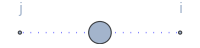
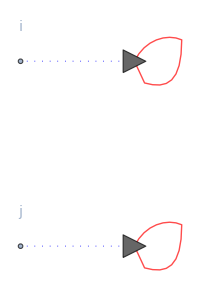
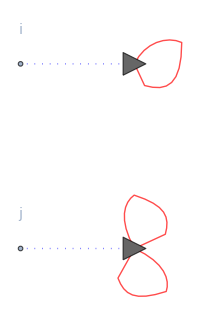
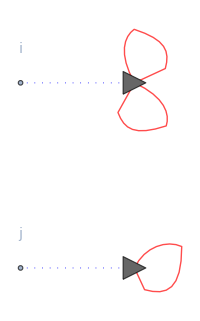
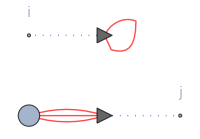
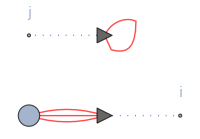
-Graphics-^-1= | -Graphics-+1/4^ | -Graphics-+1/48^ | -Graphics-+1/48^ | -Graphics-+1/48^
 | -Graphics-+1/48^ | -Graphics-+1/48^ | -Graphics-+1/48^ | -Graphics-+1/12^
 | -Graphics-+1/12^ |  |  |

```mathematica
DSEPlot[GDisconn,fieldRules]
```

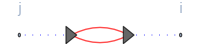
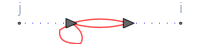
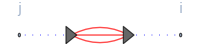
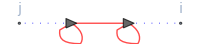
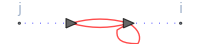
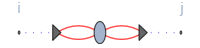
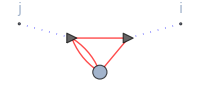
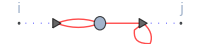
-Graphics-^-1= | -Graphics-+1/4^ | -Graphics-+1/4^ | -Graphics-+1/48^ | -Graphics-+1/48^
 | -Graphics-+1/48^ | -Graphics-+1/48^ | -Graphics-+1/48^ | -Graphics-+1/48^
 | -Graphics-+1/48^ | -Graphics-+1/48^ | -Graphics-+1/48^ | -Graphics-+1/48^
 | -Graphics-+1/48^ | -Graphics-+1/48^ | -Graphics-+1/36^ | -Graphics-+1/36^
 | -Graphics-+1/36^ | -Graphics-+1/36^ | -Graphics-+1/36^ | -Graphics-+1/36^
 | -Graphics-+1/36^ | -Graphics-+1/36^ | -Graphics-+1/36^ | -Graphics-+1/36^
 | -Graphics-+1/36^ | -Graphics-+1/36^ | -Graphics-+1/36^ | -Graphics-+1/36^
 | -Graphics-+1/36^ | -Graphics-+1/48^ | -Graphics-+1/48^ | -Graphics-+1/48^
 | -Graphics-+1/48^ | -Graphics-+1/48^ | -Graphics-+1/48^ | -Graphics-+1/48^
 | -Graphics-+1/48^ | -Graphics-+1/48^ | -Graphics-+1/48^ | -Graphics-+1/48^
 | -Graphics-+1/48^ | -Graphics-+1/4^ | -Graphics-+1/12^ | -Graphics-+1/12^
 | -Graphics-+1/12^ | -Graphics-+1/12^ | -Graphics-+1/12^ | -Graphics-+1/12^
 | -Graphics-+1/12^ | -Graphics-+1/12^ | -Graphics-+1/12^ | -Graphics-+1/12^
 | -Graphics-+1/12^ | -Graphics-+1/12^ | -Graphics-+1/12^ | -Graphics-+1/12^
 | -Graphics-+1/12^ | -Graphics-+1/12^ | -Graphics-+1/12^ | -Graphics-+1/12^
 | -Graphics-+1/4^ | -Graphics-+1/4^ | -Graphics-+1/4^ |

```mathematica
DSEPlot[GConn,fieldRules]
```

```mathematica
GConnId=identifyGraphs[sortCanonical[GConn,{{FF,i},{FF,j}}],{{FF,i},{FF,j}}];
```

```mathematica
pGConnected=DSEPlot[GConnId,fieldRules]
```

-Graphics-^-1= | -Graphics-+1/2^ | -Graphics-+1/4^ | -Graphics-+1/6^ | -Graphics-+1/4^
 | -Graphics-+1/4^ | -Graphics-+1/4^ | -Graphics-+1/2^ | -Graphics-+1/4^
 | -Graphics-+1/2^ | -Graphics-+1/4^ | -Graphics-+1/4^ | -Graphics-+1/2^

```mathematica
Export[FileNameJoin[{exportDir,"pGConnected.pdf"}],pGConnected]
```

~/git_repos/DoFun_article/images/pGConnected.pdf

Split 1PI/not 1PI:

```mathematica
(G=get1PI[GConnId])//Length
(GNon1PI=getNon1PI[GConnId])//Length
Length@GConnId
```

8

4

12

```mathematica
pG=DSEPlot[G,fieldRules]
DSEPlot[GNon1PI,fieldRules]
```

-Graphics-^-1= | -Graphics-+1/2^ | -Graphics-+1/4^ | -Graphics-+1/6^ | -Graphics-+1/4^
 | -Graphics-+1/4^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^

-Graphics-^-1= | -Graphics-+1/4^ | -Graphics-+1/4^ | -Graphics-+1/4^ | -Graphics-+1/4^

```mathematica
Export[FileNameJoin[{exportDir,"pG.pdf"}],pG]
```

~/git_repos/DoFun_article/images/pG.pdf

```mathematica
defineFieldsSpecific[{A[mom,col,lor],FF[mom,lors,lors]}]
```

{A[mom,col,lor],FF[mom,lors,lors]}

```mathematica
getAE[G,{{FF,i,p,k,l},{FF,j,q,m,n}}]
```

{1/2 CO[FF[p,k,l],A[q1,a$27952,μ$27960],A[-p-q1,g$27952,β$27960],explicit→True] CO[FF[q,m,n],A[-q1,b$27952,ν$27960],A[p+q1,h$27952,γ$27960],explicit→True] P[A[-p-q1,g$27952,β$27960],A[p+q1,h$27952,γ$27960],explicit→True] P[A[q1,a$27952,μ$27960],A[-q1,b$27952,ν$27960],explicit→True],1/4 CO[FF[p,k,l],A[q2,e$27952,τ$27960],A[-p-q2,c$27953,μ$27961],explicit→True] CO[FF[q,m,n],A[-q2,a$27955,τ$27962],A[p+q2,c$27955,β$27962],A[q1,e$27955,δ$27962],A[-q1,g$27955,μ$27963],explicit→True] P[A[q1,e$27955,δ$27962],A[-q1,g$27955,μ$27963],explicit→True] P[A[-p-q2,c$27953,μ$27961],A[p+q2,c$27955,β$27962],explicit→True] P[A[q2,e$27952,τ$27960],A[-q2,a$27955,τ$27962],explicit→True],1/6 CO[FF[p,k,l],A[q1,g$27953,τ$27961],A[-p-q1-q2,c$27954,δ$27961],A[q2,g$27954,ρ$27962],explicit→True] CO[FF[q,m,n],A[-q1,h$27953,α$27961],A[p+q1+q2,d$27954,ϵ$27961],A[-q2,h$27954,σ$27962],explicit→True] P[A[q1,g$27953,τ$27961],A[-q1,h$27953,α$27961],explicit→True] P[A[-p-q1-q2,c$27954,δ$27961],A[p+q1+q2,d$27954,ϵ$27961],explicit→True] P[A[q2,g$27954,ρ$27962],A[-q2,h$27954,σ$27962],explicit→True],1/4 CO[FF[q,m,n],A[-q2,f$27952,α$27960],A[p+q2,d$27953,ν$27961],explicit→True] CO[FF[p,k,l],A[q1,b$27955,α$27962],A[-q1,d$27955,γ$27962],A[q2,f$27955,ϵ$27962],A[-p-q2,h$27955,ν$27963],explicit→True] P[A[q1,b$27955,α$27962],A[-q1,d$27955,γ$27962],explicit→True] P[A[-p-q2,h$27955,ν$27963],A[p+q2,d$27953,ν$27961],explicit→True] P[A[q2,f$27955,ϵ$27962],A[-q2,f$27952,α$27960],explicit→True],1/4 CO[FF[p,k,l],A[q1,a$27952,μ$27960],A[-p-q1,g$27952,β$27960],explicit→True] CO[FF[q,m,n],A[q2,b$27952,ν$27960],A[-q-q2,h$27952,γ$27960],explicit→True] P[A[-p-q1,g$27952,β$27960],A[p+q1,a$27956,ρ$27963],explicit→True] P[A[q1,a$27952,μ$27960],A[-q1,d$27956,α$27963],explicit→True] P[A[q2,b$27952,ν$27960],A[-q2,b$27956,σ$27963],explicit→True] P[A[q+q2,c$27956,τ$27963],A[-q-q2,h$27952,γ$27960],explicit→True] V[A[p+q1,a$27956,ρ$27963],A[-q1,d$27956,α$27963],A[-q2,b$27956,σ$27963],A[q+q2,c$27956,τ$27963],explicit→True],1/2 CO[FF[p,k,l],A[q1,c$27952,ρ$27960],A[-p-q1,a$27953,δ$27960],explicit→True] CO[FF[q,m,n],A[-q1,e$27953,ρ$27961],A[q2,a$27954,β$27961],A[-q+q1-q2,e$27954,μ$27962],explicit→True] P[A[-p-q1,a$27953,δ$27960],A[p+q1,h$27956,ϵ$27963],explicit→True] P[A[q1,c$27952,ρ$27960],A[-q1,e$27953,ρ$27961],explicit→True] P[A[q2,a$27954,β$27961],A[-q2,a$27957,μ$27964],explicit→True] P[A[q-q1+q2,b$27957,ν$27964],A[-q+q1-q2,e$27954,μ$27962],explicit→True] V[A[p+q1,h$27956,ϵ$27963],A[-q2,a$27957,μ$27964],A[q-q1+q2,b$27957,ν$27964],explicit→True],1/2 CO[FF[q,m,n],A[-q1,d$27952,σ$27960],A[-q+q1,b$27953,ϵ$27960],explicit→True] CO[FF[p,k,l],A[q1,f$27953,σ$27961],A[-p-q1-q2,b$27954,γ$27961],A[q2,f$27954,ν$27962],explicit→True] P[A[q-q1,e$27957,τ$27964],A[-q+q1,b$27953,ϵ$27960],explicit→True] P[A[q1,f$27953,σ$27961],A[-q1,d$27952,σ$27960],explicit→True] P[A[-p-q1-q2,b$27954,γ$27961],A[p+q1+q2,c$27957,ρ$27964],explicit→True] P[A[q2,f$27954,ν$27962],A[-q2,d$27957,σ$27964],explicit→True] V[A[p+q1+q2,c$27957,ρ$27964],A[-q2,d$27957,σ$27964],A[q-q1,e$27957,τ$27964],explicit→True],1/2 CO[FF[p,k,l],A[q1,a$27952,μ$27960],A[-p-q1,g$27952,β$27960],explicit→True] CO[FF[q,m,n],A[q2,b$27952,ν$27960],A[-q-q2,h$27952,γ$27960],explicit→True] P[A[-p-q1,g$27952,β$27960],A[p+q1,a$27956,ρ$27963],explicit→True] P[A[q1,a$27952,μ$27960],A[-q1,e$27956,β$27963],explicit→True] P[A[q2,b$27952,ν$27960],A[-q2,f$27956,γ$27963],explicit→True] P[A[q+q2,c$27956,τ$27963],A[-q-q2,h$27952,γ$27960],explicit→True] P[A[p+q+q1+q2,g$27956,δ$27963],A[-p-q-q1-q2,b$27956,σ$27963],explicit→True] V[A[-q1,e$27956,β$27963],A[-q2,f$27956,γ$27963],A[p+q+q1+q2,g$27956,δ$27963],explicit→True] V[A[p+q1,a$27956,ρ$27963],A[q+q2,c$27956,τ$27963],A[-p-q-q1-q2,b$27956,σ$27963],explicit→True]}

Ok:

```mathematica
X=G[[1]];
DSEPlot[X,fieldRules]
getAE[X,{{FF,i,p,k,l},{FF,j,-p,m,n}}]
Cases[%,P[___],∞][[All,1,1]]
```

-Graphics-+1/2^

{1/2 CO[FF[-p,m,n],A[-q1,b$28046,ν$28049],A[p+q1,d$28046,σ$28049],explicit→True] CO[FF[p,k,l],A[q1,a$28046,μ$28049],A[-p-q1,c$28046,ρ$28049],explicit→True] P[A[-p-q1,c$28046,ρ$28049],A[p+q1,d$28046,σ$28049],explicit→True] P[A[q1,a$28046,μ$28049],A[-q1,b$28046,ν$28049],explicit→True]}

{-p-q1,q1}

Ok:

```mathematica
X=G[[2]];
DSEPlot[X,fieldRules]
getAE[X,{{FF,i,p,k,l},{FF,j,-p,m,n}}]
Cases[%,P[___],∞][[All,1,1]]
```

-Graphics-+1/4^

{1/4 CO[FF[p,k,l],A[q2,a$28008,μ$28011],A[-p-q2,b$28008,ν$28011],explicit→True] CO[FF[-p,m,n],A[-q2,c$28008,ρ$28011],A[p+q2,d$28008,σ$28011],A[q1,e$28008,τ$28011],A[-q1,f$28008,α$28011],explicit→True] P[A[q1,e$28008,τ$28011],A[-q1,f$28008,α$28011],explicit→True] P[A[-p-q2,b$28008,ν$28011],A[p+q2,d$28008,σ$28011],explicit→True] P[A[q2,a$28008,μ$28011],A[-q2,c$28008,ρ$28011],explicit→True]}

{q1,-p-q2,q2}

Ok:

```mathematica
X=G[[3]];
DSEPlot[X,fieldRules]
getAE[X,{{FF,i,p,k,l},{FF,j,-p,m,n}}]
Cases[%,P[___],∞][[All,1,1]]
```

-Graphics-+1/6^

{1/6 CO[FF[-p,m,n],A[-q1,b$28090,ν$28093],A[p+q1+q2,d$28090,σ$28093],A[-q2,f$28090,α$28093],explicit→True] CO[FF[p,k,l],A[q1,a$28090,μ$28093],A[-p-q1-q2,c$28090,ρ$28093],A[q2,e$28090,τ$28093],explicit→True] P[A[q1,a$28090,μ$28093],A[-q1,b$28090,ν$28093],explicit→True] P[A[-p-q1-q2,c$28090,ρ$28093],A[p+q1+q2,d$28090,σ$28093],explicit→True] P[A[q2,e$28090,τ$28093],A[-q2,f$28090,α$28093],explicit→True]}

{q1,-p-q1-q2,q2}

Ok:

```mathematica
X=G[[4]];
DSEPlot[X,fieldRules]
getAE[X,{{FF,i,p,k,l},{FF,j,-p,m,n}}]
Cases[%,P[___],∞][[All,1,1]]
```

-Graphics-+1/4^

{1/4 CO[FF[-p,m,n],A[-q2,a$28134,μ$28137],A[p+q2,b$28134,ν$28137],explicit→True] CO[FF[p,k,l],A[q1,c$28134,ρ$28137],A[-q1,d$28134,σ$28137],A[q2,e$28134,τ$28137],A[-p-q2,f$28134,α$28137],explicit→True] P[A[q1,c$28134,ρ$28137],A[-q1,d$28134,σ$28137],explicit→True] P[A[-p-q2,f$28134,α$28137],A[p+q2,b$28134,ν$28137],explicit→True] P[A[q2,e$28134,τ$28137],A[-q2,a$28134,μ$28137],explicit→True]}

{q1,-p-q2,q2}

Ok:

```mathematica
X=G[[5]];
DSEPlot[X,fieldRules]
getAE[X,{{FF,i,p,k,l},{FF,j,-p,m,n}}]
Cases[%,P[___],∞][[All,1,1]]
```

-Graphics-+1/4^

{1/4 CO[FF[-p,m,n],A[q2,b$28186,ν$28189],A[p-q2,d$28186,σ$28189],explicit→True] CO[FF[p,k,l],A[q1,a$28186,μ$28189],A[-p-q1,c$28186,ρ$28189],explicit→True] P[A[-p-q1,c$28186,ρ$28189],A[p+q1,e$28186,τ$28189],explicit→True] P[A[q1,a$28186,μ$28189],A[-q1,h$28186,γ$28189],explicit→True] P[A[q2,b$28186,ν$28189],A[-q2,f$28186,α$28189],explicit→True] P[A[-p+q2,g$28186,β$28189],A[p-q2,d$28186,σ$28189],explicit→True] V[A[p+q1,e$28186,τ$28189],A[-q1,h$28186,γ$28189],A[-q2,f$28186,α$28189],A[-p+q2,g$28186,β$28189],explicit→True]}

{-p-q1,q1,q2,-p+q2}

Ok:

```mathematica
X=G[[6]];
DSEPlot[X,fieldRules]
getAE[X,{{FF,i,p,k,l},{FF,j,-p,m,n}}]
Cases[%,P[___],∞][[All,1,1]]
```

-Graphics-+1/2^

{1/2 CO[FF[p,k,l],A[q1,a$28238,μ$28241],A[-p-q1,b$28238,ν$28241],explicit→True] CO[FF[-p,m,n],A[-q1,c$28238,ρ$28241],A[q2,d$28238,σ$28241],A[p+q1-q2,e$28238,τ$28241],explicit→True] P[A[-p-q1,b$28238,ν$28241],A[p+q1,f$28238,α$28241],explicit→True] P[A[q1,a$28238,μ$28241],A[-q1,c$28238,ρ$28241],explicit→True] P[A[q2,d$28238,σ$28241],A[-q2,g$28238,β$28241],explicit→True] P[A[-p-q1+q2,h$28238,γ$28241],A[p+q1-q2,e$28238,τ$28241],explicit→True] V[A[p+q1,f$28238,α$28241],A[-q2,g$28238,β$28241],A[-p-q1+q2,h$28238,γ$28241],explicit→True]}

{-p-q1,q1,q2,-p-q1+q2}

Ok:

```mathematica
X=G[[7]];
DSEPlot[X,fieldRules]
getAE[X,{{FF,i,p,k,l},{FF,j,-p,m,n}}]
Cases[%,P[___],∞][[All,1,1]]
```

-Graphics-+1/2^

{1/2 CO[FF[-p,m,n],A[-q1,a$28289,μ$28292],A[p+q1,b$28289,ν$28292],explicit→True] CO[FF[p,k,l],A[q1,c$28289,ρ$28292],A[-p-q1-q2,d$28289,σ$28292],A[q2,e$28289,τ$28292],explicit→True] P[A[-p-q1,h$28289,γ$28292],A[p+q1,b$28289,ν$28292],explicit→True] P[A[q1,c$28289,ρ$28292],A[-q1,a$28289,μ$28292],explicit→True] P[A[-p-q1-q2,d$28289,σ$28292],A[p+q1+q2,f$28289,α$28292],explicit→True] P[A[q2,e$28289,τ$28292],A[-q2,g$28289,β$28292],explicit→True] V[A[p+q1+q2,f$28289,α$28292],A[-q2,g$28289,β$28292],A[-p-q1,h$28289,γ$28292],explicit→True]}

{-p-q1,q1,-p-q1-q2,q2}

Ok:

```mathematica
X=G[[8]];
DSEPlot[X,fieldRules]
getAE[X,{{FF,i,p,k,l},{FF,j,-p,m,n}}]
Cases[%,P[___],∞][[All,1,1]]
```

-Graphics-+1/2^

{1/2 CO[FF[-p,m,n],A[q2,b$28351,ν$28355],A[p-q2,d$28351,σ$28355],explicit→True] CO[FF[p,k,l],A[q1,a$28351,μ$28355],A[-p-q1,c$28351,ρ$28355],explicit→True] P[A[-p-q1,c$28351,ρ$28355],A[p+q1,e$28351,τ$28355],explicit→True] P[A[q1,a$28351,μ$28355],A[-q1,h$28351,γ$28355],explicit→True] P[A[q2,b$28351,ν$28355],A[-q2,a$28352,δ$28355],explicit→True] P[A[-p+q2,g$28351,β$28355],A[p-q2,d$28351,σ$28355],explicit→True] P[A[q1+q2,b$28352,ϵ$28355],A[-q1-q2,f$28351,α$28355],explicit→True] V[A[-q1,h$28351,γ$28355],A[-q2,a$28352,δ$28355],A[q1+q2,b$28352,ϵ$28355],explicit→True] V[A[p+q1,e$28351,τ$28355],A[-p+q2,g$28351,β$28355],A[-q1-q2,f$28351,α$28355],explicit→True]}

{-p-q1,q1,q2,-p+q2,q1+q2}

### F^2: Higher loops

```mathematica
Clear@FF
```

```mathematica
setFields[{A,FF}]
```

```mathematica
fieldRules={{A,Red},{FF,Thick,Blue,Dotted}};
```

```mathematica
action={{A,A},{A,A,A},{A,A,A,A}};
```

F^2 exists schematically of A^2+A^3 +A^4.
Thus, correlation functions can be 
<A^2 A^2>
<A^2 A^3>
<A^2 A^4>
<A^3 A^2>
<A^3 A^3>
<A^3 A^4>
<A^4 A^2>
<A^4 A^3>
<A^4 A^4>

Ignore prefactors and take only a subset to illustrate structural agreement with Haas.

```mathematica
Clear@F
F[j_]:=Module[{j1,j2,j3,j4,j5,j6,j7,j8,j9},
{op[CO[{FF,j},{A,j1},{A,j2}],{A,j1},{A,j2}]/2!,
op[CO[{FF,j},{A,j3},{A,j4},{A,j5}],{A,j3},{A,j4},{A,j5}]/3!,
op[CO[{FF,j},{A,j6},{A,j7},{A,j8},{A,j9}],{A,j6},{A,j7},{A,j8},{A,j9}]/4!}]
```

```mathematica
Clear[pi]
pi[i_,j_,k_,l_]:=op[F[i][[k-1]],F[j][[l-1]]]
```

```mathematica
G1=pi[i,j,2,2]+pi[i,j,2,3]+pi[i,j,3,2]+pi[i,j,3,3]+pi[i,j,2,4]+pi[i,j,4,2];
```

```mathematica
G1=pi[i,j,2,2];
```

All parts:

```mathematica
G1=Sum[pi[i,j,a,b],{a,2,4},{b,2,4}];
```

```mathematica
Timing[G4=doCO[action,G1]]
```

{126.635,1/4 op[CO[{FF,i},{A,j1$2836},{A,j2$2836}],P[{A,j1$2836},{A,j1$2837}],P[{A,j2$2836},{A,j2$2837}],CO[{FF,j},{A,j1$2837},{A,j2$2837}]]+1/4 op[1]+57181+1/576 op[1]+1/576 op[CO[{FF,i},{A,j6$2852},{A,j7$2852},{A,j8$2852},{A,j9$2852}],P[{A,j6$2852},{A,dummy[424454]}],P[{A,j7$2852},{A,dummy[91722]}],P[{A,j8$2852},{A,dummy[16926]}],P[{A,j9$2852},{A,dummy[2838]}],CO[{FF,j},{A,j6$2853},{A,j7$2853},{A,j8$2853},{A,j9$2853}],P[{A,j6$2853},{A,dummy[502]}],8,V[{A,dummy[16926]},{A,dummy[16927]},{A,dummy[16928]}],P[{A,dummy[16928]},{A,dummy[91723]}],V[{A,dummy[91722]},{A,dummy[91723]},{A,dummy[91724]}],P[{A,dummy[91724]},{A,dummy[424455]}],V[{A,dummy[424454]},{A,dummy[424455]},{A,dummy[424456]}],P[{A,dummy[424456]},{A,j9$2853}]]}
 |  |  |  |

```mathematica
G4=doCO[action,G1,onePIQ]
```

1/4 op[CO[{FF,i},{A,j1$5671},{A,j2$5671}],P[{A,j1$5671},{A,j1$5672}],P[{A,j2$5671},{A,j2$5672}],CO[{FF,j},{A,j1$5672},{A,j2$5672}]]+1/4 op[CO[{FF,i},{A,j1$5671},{A,j2$5671}],P[{A,j1$5671},{A,j2$5672}],P[{A,j2$5671},{A,j1$5672}],CO[{FF,j},{A,j1$5672},{A,j2$5672}]]+1/4 op[CO[{FF,i},{A,j1$5671},{A,j2$5671}],P[{A,j1$5671},{A,dummy[173]}],P[{A,j2$5671},{A,dummy[128]}],CO[{FF,j},{A,j1$5672},{A,j2$5672}],P[{A,j1$5672},{A,dummy[129]}],P[{A,dummy[130]},{A,j2$5672}],V[{A,dummy[173]},{A,dummy[128]},{A,dummy[129]},{A,dummy[130]}]]+1/4 op[CO[{FF,i},{A,j1$5671},{A,j2$5671}],P[{A,j1$5671},{A,dummy[180]}],P[{A,j2$5671},{A,dummy[128]}],CO[{FF,j},{A,j1$5672},{A,j2$5672}],V[{A,dummy[128]},{A,dummy[129]},{A,dummy[130]}],P[{A,dummy[130]},{A,j2$5672}],P[{A,j1$5672},{A,dummy[181]}],V[{A,dummy[180]},{A,dummy[181]},{A,dummy[182]}],P[{A,dummy[182]},{A,dummy[129]}]]+1/4 op[CO[{FF,i},{A,j1$5671},{A,j2$5671}],P[{A,j1$5671},{A,dummy[184]}],P[{A,j2$5671},{A,dummy[128]}],CO[{FF,j},{A,j1$5672},{A,j2$5672}],P[{A,j1$5672},{A,dummy[129]}],V[{A,dummy[128]},{A,dummy[129]},{A,dummy[130]}],P[{A,dummy[130]},{A,dummy[185]}],V[{A,dummy[184]},{A,dummy[185]},{A,dummy[186]}],P[{A,dummy[186]},{A,j2$5672}]]

```mathematica
COPlot[G4,fieldRules]
```

-Graphics-^-1= | -Graphics-+1/4^ | -Graphics-+1/4^ | -Graphics-+1/4^ | -Graphics-+1/4^
 | -Graphics-+1/4^ |  |  |

```mathematica
Length@G4
```

57185

```mathematica
G4L3=Select[G4,getLoopNumber[#]==3&];
```

```mathematica
Length@G4L3
```

577

Get 1PI:

```mathematica
G4L3Conn=getConnected[G4L3];
```

```mathematica
Length@G4L3Conn
```

553

```mathematica
Timing[G4L31PI=get1PI[G4L3Conn];]
```

{86.1201,Null}

```mathematica
Length@G4L31PI
```

441

```mathematica
Timing[G4L31PIId=identifyGraphs[G4L31PI,{{FF,i},{FF,j}}];]
```

{50.1859,Null}

```mathematica
Length@G4L31PIId
```

46

Export for quick access:

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"data","G4L31PIId.dat"}],G4L31PIId]
```

/data/git_repos/DoFun/Development/data/G4L31PIId.dat

```mathematica
G4L31PIId=Get[FileNameJoin[{NotebookDirectory[],"data","G4L31PIId.dat"}]];
```

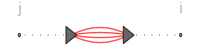
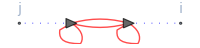
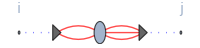
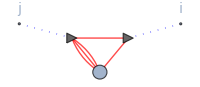
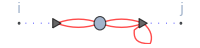
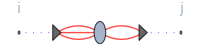
-Graphics-^-1= | -Graphics-+24^ | -Graphics-+72^ | -Graphics-+^ | -Graphics-+8^
 | -Graphics-+6^ | -Graphics-+^ | -Graphics-+9^ | -Graphics-+36^
 | -Graphics-+36^ | -Graphics-+8^ | -Graphics-+6^ | -Graphics-+36^
 | -Graphics-+36^ | -Graphics-+3^ | -Graphics-+3^ | -Graphics-+3^
 | -Graphics-+24^ | -Graphics-+6^ | -Graphics-+12^ | -Graphics-+^
 | -Graphics-+^ | -Graphics-+2^ | -Graphics-+^ | -Graphics-+2^
 | -Graphics-+2^ | -Graphics-+9^ | -Graphics-+18^ | -Graphics-+3^
 | -Graphics-+3^ | -Graphics-+3^ | -Graphics-+8^ | -Graphics-+8^
 | -Graphics-+8^ | -Graphics-+12^ | -Graphics-+2^ | -Graphics-+2^
 | -Graphics-+2^ | -Graphics-+6^ | -Graphics-+3^ | -Graphics-+3^
 | -Graphics-+2^ | -Graphics-+2^ | -Graphics-+2^ | -Graphics-+2^
 | -Graphics-+2^ | -Graphics-+2^ |  |

```mathematica
DSEPlot[G4L31PIId,fieldRules]
```

Select different topologies:

```mathematica
G4L31PISel=G4L31PIId[[{1,2,3,4,
5,7,8,
9,
14,16,
17,18,19,
26,27,28,
40}]];
```

```mathematica
DSEPlot[G4L31PISel/.a_?NumericQ b_op:>b,fieldRules,output->List,indexStyle->{Transparent}]
```

{-Graphics-+^,-Graphics-+^,-Graphics-+^,-Graphics-+^,-Graphics-+^,-Graphics-+^,-Graphics-+^,-Graphics-+^,-Graphics-+^,-Graphics-+^,-Graphics-+^,-Graphics-+^,-Graphics-+^,-Graphics-+^,-Graphics-+^,-Graphics-+^,-Graphics-+^}

```mathematica
Length[G4L31PISel]
```

17

```mathematica
pGL3Graphs=GraphicsGrid@Partition[PadRight[Map[DSEPlot[#,fieldRules,indexStyle->{Transparent},ImageSize->70]&,List@@G4L31PISel],18,Graphics[]],6]
```

-Graphics-

```mathematica
Export[FileNameJoin[{exportDir,"pGL3Graphs.pdf"}],pGL3Graphs]
```

~/git_repos/DoFun_article/images/pGL3Graphs.pdf

Four loops:
Do not run in debug mode on computer with little RAM.

```mathematica
G4L4=Select[G4,getLoopNumber[#]==4&];
```

```mathematica
Length@G4L4
```

3200

Get 1PI:

```mathematica
G4L4Conn=getConnected[G4L4];
```

```mathematica
Length@G4L4Conn
```

3168

```mathematica
G4L41PI=get1PI[G4L4Conn];
```

```mathematica
Length@G4L41PI
```

2764

```mathematica
G4L41PI[[1]]
```

1/48 op[CO[{FF,15},{A,j1$2840},{A,j2$2840}],P[{A,j1$2840},{A,dummy[3720]}],P[{A,j2$2840},{A,dummy[1275]}],CO[{FF,j},{A,j6$2841},{A,j7$2841},{A,j8$2841},{A,j9$2841}],P[{A,j6$2841},{A,dummy[262]}],P[{A,j7$2841},{A,dummy[34]}],P[{A,j8$2841},{A,dummy[35]}],P[{A,dummy[36]},{A,j9$2841}],V[{A,dummy[3720]},{A,dummy[1275]},{A,dummy[262]},{A,dummy[34]},{A,dummy[35]},{A,dummy[36]}]]

```mathematica
G4L41PI[[2]]
```

1/36 op[CO[{FF,15},{A,j3$2844},{A,j4$2844},{A,j5$2844}],P[{A,j3$2844},{A,dummy[6068]}],P[{A,j4$2844},{A,dummy[1567]}],P[{A,j5$2844},{A,dummy[311]}],CO[{FF,j},{A,j3$2845},{A,j4$2845},{A,j5$2845}],P[{A,j3$2845},{A,dummy[42]}],P[{A,j4$2845},{A,dummy[43]}],P[{A,dummy[44]},{A,j5$2845}],V[{A,dummy[6068]},{A,dummy[1567]},{A,dummy[311]},{A,dummy[42]},{A,dummy[43]},{A,dummy[44]}]]

Some 4-loop diagrams:

```mathematica
DSEPlot[List@@G4L41PI[[1;;20]],fieldRules]
```

{-Graphics-+1/48^,-Graphics-+1/36^,-Graphics-+1/144^,-Graphics-+1/144^,-Graphics-+1/144^,-Graphics-+1/144^,-Graphics-+1/144^,-Graphics-+1/144^,-Graphics-+1/144^,-Graphics-+1/144^,-Graphics-+1/144^,-Graphics-+1/144^,-Graphics-+1/144^,-Graphics-+1/144^,-Graphics-+1/144^,-Graphics-+1/144^,-Graphics-+1/144^,-Graphics-+1/144^,-Graphics-+1/144^,-Graphics-+1/144^}

```mathematica
G4L41PIId=identifyGraphs[G4L41PI,{{FF,i},{FF,j}}];
```

$Aborted

```mathematica
Length@G4L41PIId
```

```mathematica
DSEPlot[G4L41PIId,fieldRules]
```

## New plotting routines

```mathematica
action={{A,A},{c,cb},{A,cb,c},{A,A,A},{A,A,A,A}};
```

```mathematica
actionRG={{A,A},{c,cb},{A,cb,c},{A,A,A},{A,A,A,A},{A,A,cb,c},{cb,cb,c,c},{A,A,A,cb,c},{cb,cb,c,c,A}};
```

```mathematica
fieldRules={{A,Red},{c,Green,Dashing[{0.02,0.01}]},{FF,Blue,Dotted}};
```

```mathematica
setFields[{A,FF},{{c,cb}}]
```

```mathematica
$signConvention=1;
```

```mathematica
doRGE[actionRG,{},tDerivative->False]
RGEPlot[%,fieldRules]
RGEPlot[%%,VertexSize->0.01]
```

1/2 op[dR[{A,r1},{A,s1}],P[{A,s1},{A,r1}]]-op[dR[{cb,r1},{c,s1}],P[{c,s1},{cb,r1}]]

Γ^k∂_t ^= | -Graphics-+1/2^ | -Graphics--^ |  |

Γ^k∂_t ^= | -Graphics-+1/2^ | -Graphics--^ |  |

```mathematica
doRGE[actionRG,{A,A},tDerivative->False]
RGEPlot[%,fieldRules]
RGEPlot[%%]
RGEPlot[%%%,indexStyle->{Black}]
```

-1/2 op[P[{A,r1},{A,s1}],V[{A,i1},{A,i2},{A,r1},{A,s1}]]+op[P[{c,r1},{cb,s1}],V[{A,i1},{A,i2},{cb,s1},{c,r1}]]-1/2 op[P[{A,r1},{A,s1}],V[{A,i2},{A,s1},{A,t1}],P[{A,t1},{A,u1}],V[{A,i1},{A,r1},{A,u1}]]+op[P[{c,r1},{cb,s1}],V[{A,i2},{cb,s1},{c,t1}],P[{c,t1},{cb,u1}],V[{A,i1},{cb,u1},{c,r1}]]

-Graphics-∂_t ^-1= | -Graphics--1/2^ | -Graphics-+^ | -Graphics--1/2^ | -Graphics-+^

-Graphics-∂_t ^-1= | -Graphics--1/2^ | -Graphics-+^ | -Graphics--1/2^ | -Graphics-+^

-Graphics-∂_t ^-1= | -Graphics--1/2^ | -Graphics-+^ | -Graphics--1/2^ | -Graphics-+^

```mathematica
doRGE[actionRG,{c,cb},tDerivative->False]
RGEPlot[%,fieldRules]
RGEPlot[%%]
```

1/2 op[P[{A,r1},{A,s1}],V[{A,r1},{A,s1},{cb,i2},{c,i1}]]+op[P[{c,r1},{cb,s1}],V[{cb,i2},{cb,s1},{c,i1},{c,r1}]]-op[P[{A,r1},{A,s1}],V[{A,s1},{cb,i2},{c,t1}],P[{c,t1},{cb,u1}],V[{A,r1},{cb,u1},{c,i1}]]

-Graphics-∂_t ^-1= | -Graphics-+1/2^ | -Graphics-+^ | -Graphics--^ |

-Graphics-∂_t ^-1= | -Graphics-+1/2^ | -Graphics-+^ | -Graphics--^ |

```mathematica
doRGE[actionRG,{A,A},tDerivative->True]
RGEPlot[%,fieldRules,regulatorSymbol->crossSymbol,vertexSymbol->boxSymbol]
RGEPlot[%%,regulatorSymbol->diskOpenSymbol,vertexSymbol->boxSymbol,VertexSize->0.05]
```

1/2 op[dR[{A,r1},{A,s1}],P[{A,t1},{A,r1}],P[{A,s1},{A,u1}],V[{A,i1},{A,i2},{A,t1},{A,u1}]]-op[dR[{cb,r1},{c,s1}],P[{c,t1},{cb,r1}],P[{c,s1},{cb,u1}],V[{A,i1},{A,i2},{cb,u1},{c,t1}]]+op[dR[{A,r1},{A,s1}],P[{A,t1},{A,r1}],P[{A,s1},{A,u1}],V[{A,i2},{A,u1},{A,v1}],P[{A,v1},{A,w1}],V[{A,i1},{A,t1},{A,w1}]]-2 op[dR[{cb,r1},{c,s1}],P[{c,t1},{cb,r1}],P[{c,s1},{cb,u1}],V[{A,i2},{cb,u1},{c,v1}],P[{c,v1},{cb,w1}],V[{A,i1},{cb,w1},{c,t1}]]

-Graphics-∂_t ^-1= | -Graphics-+1/2^ | -Graphics--^ | -Graphics-+^ | -Graphics--2^

-Graphics-∂_t ^-1= | -Graphics-+1/2^ | -Graphics--^ | -Graphics-+^ | -Graphics--2^

```mathematica
doDSE[action,{A,A}]
DSEPlot[%,fieldRules]
DSEPlot[%%,fieldRules,bareVertexSymbol->diskOpenSymbol,vertexSymbol->triangleSymbol]
DSEPlot[%%%,bareVertexSymbol->diskOpenSymbol,vertexSymbol->triangleSymbol]
```

op[S[{A,i1},{A,i2}]]-1/2 op[P[{A,r1},{A,s1}],S[{A,i1},{A,i2},{A,r1},{A,s1}]]-1/2 op[S[{A,i1},{A,r1},{A,s1}],P[{A,s1},{A,t1}],V[{A,i2},{A,t1},{A,u1}],P[{A,u1},{A,r1}]]+op[S[{A,i1},{cb,r1},{c,s1}],P[{c,s1},{cb,t1}],V[{A,i2},{cb,t1},{c,u1}],P[{c,u1},{cb,r1}]]-1/6 op[S[{A,i1},{A,r1},{A,s1},{A,t1}],P[{A,t1},{A,u1}],P[{A,s1},{A,v1}],V[{A,i2},{A,u1},{A,v1},{A,w1}],P[{A,w1},{A,r1}]]-1/2 op[S[{A,i1},{A,r1},{A,s1},{A,t1}],P[{A,t1},{A,u1}],P[{A,s1},{A,v1}],V[{A,u1},{A,v1},{A,w1}],P[{A,w1},{A,x1}],V[{A,i2},{A,y1},{A,x1}],P[{A,y1},{A,r1}]]

-Graphics-^-1= | -Graphics-+^-1 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics-+^
 | -Graphics--1/6^ | -Graphics--1/2^ |  |

-Graphics-^-1= | -Graphics-+^-1 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics-+^
 | -Graphics--1/6^ | -Graphics--1/2^ |  |

-Graphics-^-1= | -Graphics-+^-1 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics-+^
 | -Graphics--1/6^ | -Graphics--1/2^ |  |

```mathematica
G1:=Module[{j1,j2,j3,j4},op[op[CO[{FF,i},{A,j1},{A,j2}],{A,j1},{A,j2}]/2!,op[CO[{FF,j},{A,j3},{A,j4}],{A,j3},{A,j4}]/2!]];
G4=doCO[action,G1,getLoopNumber[#]≤2&];
COPlot[%,fieldRules,coSymbol->boxSymbol,vertexSymbol->diskTinySymbol]
COPlot[%%,coSymbol->boxSymbol,vertexSymbol->diskTinySymbol]
```

-Graphics-^-1= | -Graphics-+1/4^ | -Graphics-+1/4^ | -Graphics-+1/4^ | -Graphics-+1/4^
 | -Graphics-+1/4^ | -Graphics-+1/4^ | -Graphics-+1/4^ |

-Graphics-^-1= | -Graphics-+1/4^ | -Graphics-+1/4^ | -Graphics-+1/4^ | -Graphics-+1/4^
 | -Graphics-+1/4^ | -Graphics-+1/4^ | -Graphics-+1/4^ |

## Examples from DoFun2 article

Examples taken from DoFun 2 article and modified where necessary.

### 4.1 Derivation of DSEs OK

```mathematica
setFields[{phi},{{psi,psib}}]
```

```mathematica
doDSE[{{phi,phi},{phi,phi,phi,phi}},{phi,phi}]
```

op[S[{phi,i1},{phi,i2}]]-1/2 op[P[{phi,r1},{phi,s1}],S[{phi,i1},{phi,i2},{phi,r1},{phi,s1}]]-1/6 op[S[{phi,i1},{phi,r1},{phi,s1},{phi,t1}],P[{phi,t1},{phi,u1}],P[{phi,s1},{phi,v1}],V[{phi,i2},{phi,u1},{phi,v1},{phi,w1}],P[{phi,w1},{phi,r1}]]

```mathematica
twoPointPhi=doDSE[{{phi,phi},{phi,phi,phi,phi}},{{phi,a},{phi,b}}]
```

op[S[{phi,a},{phi,b}]]-1/2 op[P[{phi,r1},{phi,s1}],S[{phi,a},{phi,b},{phi,r1},{phi,s1}]]-1/6 op[S[{phi,a},{phi,r1},{phi,s1},{phi,t1}],P[{phi,t1},{phi,u1}],P[{phi,s1},{phi,v1}],V[{phi,b},{phi,u1},{phi,v1},{phi,w1}],P[{phi,w1},{phi,r1}]]

```mathematica
twoPointPsi=doDSE[{{psi,psib},{psib,psib,psi,psi}},{{psib,a},{psi,b}}]
```

-op[S[{psi,b},{psib,a}]]-1/2 op[S[{psib,a},{psib,r1},{psi,s1},{psi,t1}],P[{psi,t1},{psib,u1}],sf[{psib,u1},{{psi,s1},{psib,v1}}],P[{psi,s1},{psib,v1}],V[{psib,u1},{psib,v1},{psi,b},{psi,w1}],P[{psi,w1},{psib,r1}]]

```mathematica
setFields[{},{{psi,psib}},{{phi,phib}}]
```

```mathematica
twoPointMixed=doDSE[{{phi,phib},{psi,psib},{psib,psi,phib,phi},{phib,phib,phi,phi},{psib,psib,psi,psi}},{{phi,b},{phib,a}},specificFieldDefinitions->{phi,phib,{psi,psib}}]
```

op[S[{phi,b},{phib,a}]]-op[P[{phi,r1},{phib,s1}],S[{phi,b},{phib,a},{phi,r1},{phib,s1}]]+op[P[{psi,r1},{psib,s1}],S[{phi,b},{phib,a},{psib,s1},{psi,r1}]]

### 4.2 Derivation of RGEs OK

```mathematica
setFields[{phi}]
```

```mathematica
doRGE[{{phi,phi},{phi,phi,phi,phi}},{}]
```

1/2 op[dR[{phi,r1},{phi,s1}],P[{phi,s1},{phi,r1}]]

```mathematica
doRGE[{{phi,phi},{phi,phi,phi,phi}},{phi,phi}]
```

1/2 op[dR[{phi,r1},{phi,s1}],P[{phi,t1},{phi,r1}],P[{phi,s1},{phi,u1}],V[{phi,i1},{phi,i2},{phi,t1},{phi,u1}]]

```mathematica
threeR=doRGE[{{phi,phi},{phi,phi,phi}},{phi,phi,phi}];
```

```mathematica
threeRPnot=doRGE[{{phi,phi},{phi,phi,phi}},{phi,phi,phi},tDerivative->False]
```

op[P[{phi,r1},{phi,s1}],V[{phi,i2},{phi,s1},{phi,t1}],P[{phi,t1},{phi,u1}],V[{phi,i3},{phi,v1},{phi,u1}],P[{phi,v1},{phi,w1}],V[{phi,i1},{phi,r1},{phi,w1}]]

### 4.3 (Graphical) Rpresentation of the output of doRGE and doDSE OK

```mathematica
shortExpression[op[S[{W,i},{W,k},{W,l}],P[{W,k},{W,ks}],P[{W,l},{W,ls}],V[{W,ks},{W,ls},{W,j}]]]
```

S_(W W W)^(i k l) Γ_(W W W)^(ks ls j) Δ_(W W)^(k ks) Δ_(W W)^(l ls)

```mathematica
shortExpression[op[S[{W,i},{W,k},{W,l}],P[{W,k},{W,ks}],dR[{W,ks},{W,ms}],P[{W,ms},{W,m}],P[{W,l},{W,ls}],V[{W,m},{W,ls},{W,j}]],FontSize->20,Bold]
```

∂_t R_(W W)^(ks ms) S_(W W W)^(i k l) Γ_(W W W)^(m ls j) Δ_(W W)^(k ks) Δ_(W W)^(l ls) Δ_(W W)^(ms m)

```mathematica
RGEPlot[doRGE[{{phi,phi},{phi,phi,phi},{phi,phi,phi,phi}},{{phi,a},{phi,b}}]]
```

-Graphics-∂_t ^-1= | -Graphics-+1/2^ | -Graphics-+^ |  |

```mathematica
RGEPlot[doRGE[{{phi,phi},{phi,phi,phi},{phi,phi,phi,phi}},{{phi,a},{phi,b}}],{{phi,Black}}]
```

-Graphics-∂_t ^-1= | -Graphics-+1/2^ | -Graphics-+^ |  |

### 4.4 Algebraic expressions OK

```mathematica
addIndices[{flavor,{i,j,k,l,m,n}}]
```

{dummyNames[flavor]→{i,j,k,l,m,n},dummyNames[adjCol]→{ca1,ca2,ca3,ca4,ca5,ca6,ca7,ca8},dummyNames[FundCol]→{c1,c2,c3,c4,c5,c6,c7,c8},dummyNames[FundFlav]→{f1,f2,f3,f4,f5,f6,f7,f8},dummyNames[lorentz]→{mu,mu1,mu2,mu3,mu4,mu5,mu6,mu7,mu8},dummyNames[dirac]→{h,i,j,k,l,m,n,o,d1,d2,d3,d4,d5,d6,d7,d8},dummyNames[adj]→{a,b,c,d,e,f,g,h,i,j},dummyNames[lor]→{μ,ν,ρ,σ,τ,α,β,γ,δ,ϵ}}

```mathematica
setFields[{phi}]
```

```mathematica
defineFieldsSpecific[{phi[momentum,type]}];
```

```mathematica
addIndices[{type,{i,j,l,m,n}}];
```

```mathematica
P[phi[p1_,i_],phi[p2_,j_],explicit->True]:=delta[type,i,j]/(Z[k,p1^2]p1^2+R[k,p1^2])
dR[phi[p1_,i_],phi[p2_,j_],explicit->True]:=delta[type,i,j] dR[k,p1^2]
V[phi[p1_,i_],phi[p2_,j_],phi[p3_,k_],phi[p4_,l_],explicit->True]:=-lambda delta[type,i,l] delta[type,j,k]-lambda delta[type,i,k] delta[type,j,l]-lambda delta[type,i,j] delta[type,k,l]
```

```mathematica
twoR=doRGE[{{phi,phi},{phi,phi,phi,phi}},{{phi,a},{phi,b}}]
```

1/2 op[dR[{phi,r1},{phi,s1}],P[{phi,t1},{phi,r1}],P[{phi,s1},{phi,u1}],V[{phi,a},{phi,b},{phi,t1},{phi,u1}]]

```mathematica
fourR=doRGE[{{phi,phi},{phi,phi,phi,phi}},{{phi,a},{phi,b},{phi,c},{phi,d}}];
```

```mathematica
Plus@@getAE[fourR,{{phi,a,0,i},{phi,b,0,j},{phi,c,0,l},{phi,d,0,m}}];
```

```mathematica
integrateDeltas[delta[type,j,1] delta[type,j,1] Plus@@getAE[twoR,{{phi,a,0,i},{phi,b,0,j}}]]/.dim[type]:>Ntype
```

-(lambda delta[type,i,j] dR[k,q1^2])/((R[k,q1^2]+q1^2 Z[k,q1^2])^2)-(lambda Ntype delta[type,i,j] dR[k,q1^2])/(2 (R[k,q1^2]+q1^2 Z[k,q1^2])^2)

```mathematica
integrateDeltas[delta[type,i,1] delta[type,j,1] delta[type,l,1] delta[type,m,1] Plus@@getAE[fourR,{{phi,a,0,i},{phi,b,0,j},{phi,c,0,l}, {phi,d,0,m}}]]/.dim[type]:>Ntype
```

-(24 lambda^2 dR[k,q1^2])/((R[k,q1^2]+q1^2 Z[k,q1^2])^3)-(3 lambda^2 Ntype dR[k,q1^2])/((R[k,q1^2]+q1^2 Z[k,q1^2])^3)

### O(N) model BROKEN: broken phase

#### 5.1 Introduction OK

```mathematica
actionONSymbolic={{phi,10,even}};
```

```mathematica
actionONSTrunc2={{phi,4,even}};
```

```mathematica
setFields[{phi}]
```

```mathematica
defineFieldsSpecific[{phi[momentum,type]}];
```

```mathematica
setFields[{phi}]
```

```mathematica
actionONPotential=convertAction[1/2 (q^2 Z[q^2]+R[k]) op[phi[q,a],phi[-q,a]]+U[phi]];
```

```mathematica
fieldStyleON={{phi,Black}};
```

#### 5.1.1 Symmetric regime OK

```mathematica
zeroPoint=doRGE[actionONSymbolic,{}];
twoPoint=doRGE[actionONSymbolic,{phi,phi}];
fourPoint=doRGE[actionONSymbolic,{phi,phi,phi,phi}];
sixPoint=doRGE[actionONSymbolic,{phi,phi,phi,phi,phi,phi}];
```

```mathematica
P[phi[p1_,a_],phi[p2_,b_],explicit->True]:=(delta[type,a,b])/(Z[p1^2]+R[p1^2,k]);
dR[phi[p1_,a_],phi[p2_,b_],explicit->True]:=delta[type,a,b] dR[p1^2,k];
```

```mathematica
actionON2=convertAction[1/2 (p^2 Z[p^2]+R[k])op[phi[p,i],phi[-p,i]]+lambda2/8op[phi[p,i],phi[q,i],phi[r,j],phi[-p-q-r,j]]];
```

```mathematica
V[phi[p1_,i_],phi[p2_,j_],phi[p3_,l_],phi[p4_,m_],explicit->True]=getFR[actionON2,{phi[p1,i],phi[p2,j],phi[p3,l],phi[p4,m]}]/deltam[p1+p2+p3+p4]//Expand;
```

```mathematica
zeroPointAlg=Plus@@getAE[zeroPoint,{}]//integrateDeltas
```

(dim[type] dR[q1^2,k])/(2 (R[q1^2,k]+Z[q1^2]))

```mathematica
twoPointAlg=Plus@@getAE[twoPoint,{{phi,i1,p1,i},{phi,i2,p2,j}}]//integrateDeltas
```

-(lambda2 delta[type,i,j] dR[q1^2,k])/((R[q1^2,k]+Z[q1^2]) (R[(p1+p2+q1)^2,k]+Z[(p1+p2+q1)^2]))-(lambda2 delta[type,i,j] dim[type] dR[q1^2,k])/(2 (R[q1^2,k]+Z[q1^2]) (R[(p1+p2+q1)^2,k]+Z[(p1+p2+q1)^2]))

```mathematica
fourPointAlg=Plus@@getAE[fourPoint,{{phi,i1,0,i},{phi,i2,0,j},{phi,i3,0,l},{phi,i4,0,m}}]/.V[a___]:>0/;Length@{a}>4//integrateDeltas//Simplify
```

-1/((R[q1^2,k]+Z[q1^2])^3)lambda2^2 (delta[type,i,m] delta[type,j,l]+delta[type,i,l] delta[type,j,m]+delta[type,i,j] delta[type,l,m]) (8+dim[type]) dR[q1^2,k]

#### 5.1.2 (Spontaneously) Broken O(N) symmetry in the ground state BROKEN

```mathematica
setFields[{phi,phi0}];
```

```mathematica
defineFieldsSpecific[{phi[momentum,type],phi0[momentum,type]}];
actionON2=convertAction[1/2 (p^2 Z[p^2]+R[k]) op[phi[p,i],phi[-p,i]]+lambda2b/8 op[op[phi[p,i],phi[q,i]]-op[phi0[p,i],phi0[q,i]],op[phi[r,j],phi[-p-q-r,j]]-op[phi0[r,j],phi0[-p-q-r,j]]]];
```

```mathematica
actionON2=convertAction[1/2 (p^2 Z[p^2]+R[k]) op[phi[p,i],phi[-p,i]]+lambda2b/8 op[op[phi[p,i],phi[q,i]]-op[phi0[p,i],phi0[q,i]],op[phi[r,j],phi[-p-q-r,j]]-op[phi0[r,j],phi0[-p-q-r,j]]]];
```

```mathematica
P[phi[p1_,a_],phi[p2_,b_],explicit->True]:=delta[type,a,1] delta[type,b,1]/(Z[p1^2] p1^2+R[p1^2,k]+2 rho0 lambda2b)+(delta[type,a,b]-delta[type,a,1] delta[type,b,1])/(Z[p1^2] p1^2+R[p1^2,k]);
```

```mathematica
dR[phi[p1_,a_],phi[p2_,b_],explicit->True]:=delta[type,a,b] dR[p1^2,k];
```

```mathematica
V[phi[p1_,i_],phi[p2_,j_],phi[p3_,k_],phi[p4_,l_],explicit->True]=getFR[actionON2,{phi[p1,i],phi[p2,j],phi[p3,k],phi[p4,l]},symmetry->broken]/deltam[p1+p2+p3+p4]//Expand;
```

```mathematica
zeroPointAlg=Plus@@getAE[zeroPoint,{}]//integrateDeltas
```

-dR[q1^2,k]/(2 (R[q1^2,k]+q1^2 Z[q1^2]))+(dim[type] dR[q1^2,k])/(2 (R[q1^2,k]+q1^2 Z[q1^2]))+dR[q1^2,k]/(2 (2 lambda2b rho0+R[q1^2,k]+q1^2 Z[q1^2]))

```mathematica
fourPointTrunc2=doRGE[actionONSTrunc2,{phi,phi,phi,phi}];
```

```mathematica
fourPointT2Alg=Plus@@getAE[fourPointTrunc2,{{phi,i1,0,i},{phi,i2,0,j},{phi,i3,0,l},{phi,i4,0,m}}]//integrateDeltas;
```

```mathematica
dimLessRulesON={R[q1^2,k]:>q1^2 r[y],rho0:>Z[q1^2]^(-1) kappa k^(d-2),lambda2b:>Z[q1^2]^2 lambda2 k^(4-d),dR[q1^2,k]:>q1^2 dtr[y],q1:>Sqrt[y] k,dq1:>k^2/2/q1};
```

```mathematica
angleInt[d_]:=4v[d];
fourPointT2Algy=Simplify[(angleInt[d] dq1 q1^(d-1) integrateDeltas[delta[type,i,1] delta[type,j,1] delta[type,l,1] delta[type,m,1] fourPointT2Alg]//.dimLessRulesON),d∈Integers]
```

6 k^(4-d) lambda2^2 y^(d/2) dtr[y] v[d] Z[k^2 y]^4 (1/(y^3 (r[y]+Z[k^2 y])^3)-dim[type]/(y^3 (r[y]+Z[k^2 y])^3)-9/((y r[y]+(2 kappa lambda2+y) Z[k^2 y])^3))

```mathematica
integrateDeltas[delta[type,i,1] delta[type,j,1] delta[type,l,1] delta[type,m,1] (delta[type,i,j] delta[type,l,m]+delta[type,i,l] delta[type,j,m]+delta[type,i,m] delta[type,j,l])]//.dimLessRulesON
```

3

```mathematica
twoPointB=doRGE[actionONSTrunc2,{phi,phi},symmetry->broken];
```

```mathematica
twoPointB
```

1/2 op[dR[{phi,r1},{phi,s1}],P[{phi,t1},{phi,r1}],P[{phi,s1},{phi,u1}],V[{phi,i1},{phi,i2},{phi,t1},{phi,u1}]]+1/2 op[dR[{phi,r1},{phi,s1}],P[{phi,traceIndex2},{phi,r1}],P[{phi,s1},{phi,dummy[4758]}],{phi,dummy[4761]},{{phi V[{phi,t1},{phi,u1},{phi,traceIndex2},{phi,dummy[4758]}],dummy[4761] V[{phi,t1},{phi,u1},{phi,traceIndex2},{phi,dummy[4758]}]}}]

```mathematica
twoPointAlg=integrateDeltas[Plus@@getAE[twoPointB,{{phi,i1,0,i},{phi,i2,0,j}}]];
```

```mathematica
twoPointAlg=getAE[twoPointB[[2]],{{phi,i1,0,i},{phi,i2,0,j}}]
```

getAE::incorrectNumberOfMomenta: The expression has more or less legs than provided by {{phi,i1,0,i},{phi,i2,0,j}}. Adjust the number of legs.

```mathematica
Cases[Replace[twoPointB[[2]],op[b__]:>{op[b]}(*in case a=op[___]*)],op[___],∞][[1]]
Cases[%,{_?fieldQ,_},∞]
Tally[%]
Count[%,{_,1}]
```

op[dR[{phi,r1},{phi,s1}],P[{phi,traceIndex2},{phi,r1}],P[{phi,s1},{phi,dummy[4758]}],{phi,dummy[4761]},{{phi V[{phi,t1},{phi,u1},{phi,traceIndex2},{phi,dummy[4758]}],dummy[4761] V[{phi,t1},{phi,u1},{phi,traceIndex2},{phi,dummy[4758]}]}}]

{{phi,r1},{phi,s1},{phi,traceIndex2},{phi,r1},{phi,s1},{phi,dummy[4758]},{phi,dummy[4761]},{phi,t1},{phi,u1},{phi,traceIndex2},{phi,dummy[4758]},{phi,t1},{phi,u1},{phi,traceIndex2},{phi,dummy[4758]}}

{{{phi,r1},2},{{phi,s1},2},{{phi,traceIndex2},3},{{phi,dummy[4758]},3},{{phi,dummy[4761]},1},{{phi,t1},2},{{phi,u1},2}}

1

```mathematica
Count[Tally[Cases[Cases[Replace[twoPointB[[2]],op[b__]:>{op[b]}(*in case a=op[___]*)],op[___],∞][[1]](*take first instance*),{_?fieldQ,_},∞]],{_,1}]≠Length@2
```

True

```mathematica
twoPointAlgProj=integrateDeltas[delta[type,i,1] delta[type,j,1] twoPointAlg]/.phi[0,i_]:>phi0[i]/.phi0[_]^2:>2 rho0
```

-(2 lambda2b^2 rho0 dR[q1^2,k])/((R[q1^2,k]+q1^2 Z[q1^2])^3)+(2 lambda2b^2 rho0 dim[type] dR[q1^2,k])/((R[q1^2,k]+q1^2 Z[q1^2])^3)+(lambda2b dR[q1^2,k])/(2 (R[q1^2,k]+q1^2 Z[q1^2])^2)-(lambda2b dim[type] dR[q1^2,k])/(2 (R[q1^2,k]+q1^2 Z[q1^2])^2)+(18 lambda2b^2 rho0 dR[q1^2,k])/((2 lambda2b rho0+R[q1^2,k]+q1^2 Z[q1^2])^3)-(3 lambda2b dR[q1^2,k])/(2 (2 lambda2b rho0+R[q1^2,k]+q1^2 Z[q1^2])^2)

```mathematica
twoPointAlgProjy=Simplify[#,Element[d,Integers]]&/@(angleInt[d] dq1 q1^(d-1) twoPointAlgProj//.dimLessRulesON//Expand)//Simplify
```

k^2 lambda2 y^(d/2) dtr[y] v[d] Z[k^2 y]^2 (1/(y^2 (r[y]+Z[k^2 y])^2)-dim[type]/(y^2 (r[y]+Z[k^2 y])^2)-3/((y r[y]+(2 kappa lambda2+y) Z[k^2 y])^2)+4 kappa lambda2 Z[k^2 y] (-1/(y^3 (r[y]+Z[k^2 y])^3)+dim[type]/(y^3 (r[y]+Z[k^2 y])^3)+9/((y r[y]+(2 kappa lambda2+y) Z[k^2 y])^3)))

```mathematica
twoPointAlgProjy/k^2/Z[k^2 y]/lambda2
```

y^(d/2) dtr[y] v[d] Z[k^2 y] (1/(y^2 (r[y]+Z[k^2 y])^2)-dim[type]/(y^2 (r[y]+Z[k^2 y])^2)-3/((y r[y]+(2 kappa lambda2+y) Z[k^2 y])^2)+4 kappa lambda2 Z[k^2 y] (-1/(y^3 (r[y]+Z[k^2 y])^3)+dim[type]/(y^3 (r[y]+Z[k^2 y])^3)+9/((y r[y]+(2 kappa lambda2+y) Z[k^2 y])^3)))

```mathematica
regRulesZ={r[y]:>(1/y-1) UnitStep[1-y],dtr[y]:>2/y UnitStep[1-y],Z[_]:>1};
```

```mathematica
Integrate[fourPointT2Algy/(-3 k^(4-d))/.regRulesZ,{y,0,∞},Assumptions->{d>0}]
```

-(8 lambda2^2 (1-9/(1+2 kappa lambda2)^3-dim[type]) v[d])/d

### Gross-Neveu model BROKEN? Sign changes

```mathematica
setFields[{},{{psi,psib}}]
```

```mathematica
defineFieldsSpecific[{{psi[momentum,dirac,flavor],psib[momentum,dirac,flavor]}}];
```

Warning: defineFieldsSpecific should not be used anymore. Use setFields instead.

```mathematica
actionGN=convertAction[diracM[q,a,b] (Z[q^2]+Rs[q^2,k]) op[psib[q,a,i],psi[q,b,i]]+gb/(2 Nf) op[psib[q1,a,i],psi[q2,a,i],psib[q3,b,j],psi[q3+q1-q2,b,j]]];
```

```mathematica
twoPoint=doRGE[actionGN,{psib,psi}];
fourPoint=doRGE[actionGN,{{psib,i1},{psib,i2},{psi,i3},{psi,i4}}];
```

```mathematica
FR2Point=getFR[actionGN,{psib[p1,a,i],psi[p2,b,j]}]
```

delta[flavor,i,j] deltam[-p1+p2] diracM[p1,a,b] Rs[p1^2,k]+delta[flavor,i,j] deltam[-p1+p2] diracM[p1,a,b] Z[p1^2]

```mathematica
FR4Point=getFR[actionGN,{psib[p1,a,i],psib[p2,b,j],psi[p3,c,m],psi[p4,d,l]}]
```

1/Nf gb delta[dirac,a,c] delta[dirac,b,d] delta[flavor,i,m] delta[flavor,j,l] deltam[-p1-p2+p3+p4]-1/Nf gb delta[dirac,a,d] delta[dirac,b,c] delta[flavor,i,l] delta[flavor,j,m] deltam[-p1-p2+p3+p4]

```mathematica
P[psi[p1_,a_,i_],psib[p2_,b_,j_],explicit->True]:=delta[flavor,i,j] diracM[p1,a,b]/p1^2/(Z[p1^2]+Rs[p1^2,k]);
V[psib[p1_,a_,i_],psib[p2_,b_,j_],psi[p3_,c_,m_],psi[p4_,d_,l_],explicit->True]=FR4Point/deltam[-p1-p2+p3+p4]//Expand;
```

Must be treated like a vertex -> Set momenta accordingly.

```mathematica
dR[psib[p1_,a_,i_],psi[p2_,b_,j_],explicit->True]:=diracM[p2,a,b] delta[flavor,i,j] dRs[p1^2,k];
```

```mathematica
addIndices[{{flavor,{i,j,k,l,m,n}},{dirac,{a,b,c,d,e,f,g,h}}}];
```

```mathematica
dimRules={dim[flavor]:>Nf,dim[dirac]:>dgamma};
diracRules={diracM[-p_,a_,b_]:>-diracM[p,a,b],diracM[p_,a_,a_]:>0,diracM[q_,a_,b_] diracM[q_,b_,c_]:>q^2 delta[dirac,a,c],diracM[q_,b_,a_] diracM[q_,c_,b_]:>q^2 delta[dirac,a,c],diracM[q_,a_,b_]^2:>q^2 delta[dirac,a,a]};
```

```mathematica
twoPointAlg=Plus@@getAE[twoPoint,{{psi,i2,p1,b,j},{psib,i1,p2,a,i}}]//Expand;
```

Sign changed compared to original.

```mathematica
FixedPoint[integrateDeltas[#]/.diracRules&,twoPointAlg/.{p1->0,p2->0}]
```

-(gb delta[flavor,i,j] diracM[q1,a,b] dRs[q1^2,k])/(Nf q1^2 (Rs[q1^2,k]+Z[q1^2])^2)

(gb delta[flavor,i,j] diracM[q1,a,b] dRs[q1^2,k])/(Nf q1^2 (Rs[q1^2,k]+Z[q1^2])^2)

Note that the order of fields is such to obtain the flow eqauation for V[psib[a], psib[b], psi[c], psi[d].

```mathematica
fourPointAlg=Plus@@getAE[fourPoint,{{psib,i1,0,b,j},{psib,i2,0,a,i},{psi,i4,0,d,m},{psi,i3,0,c,l}}];
```

Sign changed compared to original.

```mathematica
fourPointAlgSim=Simplify[FixedPoint[integrateDeltas[#]/.diracRules&,fourPointAlg]]
```

-((2 gb^2 (delta[dirac,a,d] delta[dirac,b,c] delta[flavor,i,m] delta[flavor,j,l]-delta[dirac,a,c] delta[dirac,b,d] delta[flavor,i,l] delta[flavor,j,m]) (-2+dim[dirac] dim[flavor]) dRs[q1^2,k])/(Nf^2 q1^2 (Rs[q1^2,k]+Z[q1^2])^3))

(2 gb^2 (delta[dirac,a,d] delta[dirac,b,c] delta[flavor,i,m] delta[flavor,j,l]-delta[dirac,a,c] delta[dirac,b,d] delta[flavor,i,l] delta[flavor,j,m]) (-2+dim[dirac] dim[flavor]) dRs[q1^2,k])/(Nf^2 q1^2 (Rs[q1^2,k]+Z[q1^2])^3)

```mathematica
fourPointAlgSimProj=FixedPoint[integrateDeltas[#]/.diracRules&,V[psib[p1,a,i],psib[p2,b,j],psi[p3,c,l],psi[p4,d,m],explicit->True]/gb fourPointAlgSim]/.dimRules;
lhs=integrateDeltas[V[psib[p1,a,i],psib[p2,b,j],psi[p3,c,l],psi[p4,d,m],explicit->True] V[psib[p1,a,i],psib[p2,b,j],psi[p3,c,l],psi[p4,d,m],explicit->True]/gb^2]/.dimRules;
```

Sign changed compared to original.

```mathematica
beta=fourPointAlgSimProj/lhs//Simplify
```

(2 gb^2 (-2+dgamma Nf) dRs[q1^2,k])/(Nf q1^2 (Rs[q1^2,k]+Z[q1^2])^3)

-(2 gb^2 (-2+dgamma Nf) dRs[q1^2,k])/(Nf q1^2 (Rs[q1^2,k]+Z[q1^2])^3)

```mathematica
dimLessRulesGN={Rs[q1^2,k]:>r[y] Z[q1^2],gb->g k^(2-d),dRs[q1^2,k]:>-2 y Z[q1^2] r'[y],q1:>Sqrt[y] k,dq1:>k^2/2/q1};
```

```mathematica
angleInt[d_]:=4v[d];
```

Sign changed compared to original.

```mathematica
betaDimLess=angleInt[d] dq1 q1^(d-1) beta//.dimLessRulesGN//Expand;
Simplify[betaDimLess,Assumptions->Element[d,Integers]]
```

-(8 g^2 k^(2-d) (-2+dgamma Nf) y^(-1+d/2) v[d] r'[y])/(Nf (1+r[y])^3 Z[k^2 y]^2)

(8 g^2 k^(2-d) (-2+dgamma Nf) y^(-1+d/2) v[d] r'[y])/(Nf (1+r[y])^3 Z[k^2 y]^2)

```mathematica
sixPoint=doRGE[actionGN,{psib,psib,psib,psi,psi,psi}];
```

```mathematica
sixPointAlg=Plus@@getAE[sixPoint,{{psib,i1,0,a1,j1},{psib,i2,0,a2,j2},{psib,i3,0,a3,j3},{psi,i4,0,a4,j4},{psi,i5,0,a5,j5},{psi,i6,0,a6,j6}}];
```

```mathematica
fourPointAlgFinMom=Plus@@getAE[fourPoint,{{psib,i1,p1,a,i},{psib,i2,p2,b,j},{psi,i3,p3,c,l},{psi,i4,p4,d,m}}];
```

```mathematica
fourPointAlgFinMomProj=FixedPoint[integrateDeltas[#]/.diracRules&,V[psib[p1,a,i],psib[p2,b,j],psi[p3,c,l],psi[p4,d,m],explicit->True]/gb fourPointAlgFinMom]/.dimRules;
betaFinMom=fourPointAlgFinMomProj/lhs;
```

```mathematica
betaFinMomDimLess=angleInt[d] dq1 q1^(d-1) betaFinMom//.dimLessRulesGN//Expand;
```

Sign changed compared to original.

```mathematica
betaDimLessLargeNf=Limit[Expand@betaFinMomDimLess,Nf->∞];
Simplify[betaDimLessLargeNf,Assumptions->Element[d,Integers]]
```

1/((1+r[y])^2 Z[k^2 y])4 g^2 k^(2-d) y^(-1+d/2) diracM[k √y,c$232806,e$232806] v[d] (-diracM[-p2-p3-k √y,e$232806,c$232806]/((p2+p3+k √y)^2 (Rs[(p2+p3+k √y)^2,k]+Z[(p2+p3+k √y)^2]))-diracM[-p2-p4-k √y,e$232806,c$232806]/((p2+p4+k √y)^2 (Rs[(p2+p4+k √y)^2,k]+Z[(p2+p4+k √y)^2]))) r'[y]

(4 g^2 k^(2-d) y^(-1+d/2) diracM[k √y,c$172825,f$172825] v[d] ((p1+p3+k √y)^2 diracM[-p2-p3-k √y,f$172825,c$172825] (Rs[(p1+p3+k √y)^2,k]+Z[(p1+p3+k √y)^2])+(p2+p3+k √y)^2 diracM[-p1-p3-k √y,f$172825,c$172825] (Rs[(p2+p3+k √y)^2,k]+Z[(p2+p3+k √y)^2])) r'[y])/((p1+p3+k √y)^2 (p2+p3+k √y)^2 (1+r[y])^2 (Rs[(p1+p3+k √y)^2,k]+Z[(p1+p3+k √y)^2]) (Rs[(p2+p3+k √y)^2,k]+Z[(p2+p3+k √y)^2]) Z[k^2 y])

# Bug fixing

## 20200410, Grassmann fields in getFR, 3.0.1

Description: Results of getFR does not change when the order of Grassmann fields is changed.

```mathematica
setFields[{A},{{c,cb}}]
```

```mathematica
defineFieldsSpecific[{A[momentum,adj,lorentz],{c[momentum,adj],cb[momentum,adj]}}]
```

{A[momentum,adj,lorentz],{c[momentum,adj],cb[momentum,adj]}}

```mathematica
$signConvention=1;
```

The dummy is required because the indices in SUNF are only replaced if it appears also in a field.

```mathematica
actionYM:=Module[{dummy=insDummy[]},convertAction[1/2 (metr[μ,ν]-(1-1/ξ) vec[p,μ] vec[p,ν]/sp[p]) sp[p] op[A[p,a,μ],A[-p,a,ν]]-sp[p] op[cb[p,a],c[-p,a]]+I g (-vec[q,μ]) SUNF[a,b,d] op[A[p,a,μ],cb[q,b],c[-p-q,d]]+1/2 g SUNF[a,b,d] I (-vec[p,μ] op[A[p,a,ν],A[q,b,μ],A[-p-q,d,ν]]+vec[p,ν] op[A[p,a,μ],A[q,b,μ],A[-p-q,d,ν]])+1/4 g^2 SUNF[a,b,dummy] SUNF[e,f,dummy] op[A[p,a,μ],A[q,b,ν],A[r,e,μ],A[-p-q-r,f,ν]]]];
```

Ghost-gluon vertex part of action:

```mathematica
actionYM:=Module[{dummy=insDummy[]},convertAction[I g (-vec[q,μ]) SUNF[a,b,d] op[A[p,a,μ],cb[q,b],c[-p-q,d]]]];
```

```mathematica
getFR[actionYM,{A[p1,a,mu],cb[p2,b],c[p3,d]}]/deltam[p1+p2+p3]//Simplify
```

-ⅈ g SUNF[a,b,d] vec[p2,mu]

Original result:

-ⅈ g SUNF[a,b,d] vec[p2,mu]

After fixing, the sign must change.

```mathematica
getFR[actionYM,{A[p1,a,mu],c[p3,d],cb[p2,b]}]/deltam[p1+p2+p3]//Simplify
```

ⅈ g SUNF[a,b,d] vec[p2,mu]

Original result:

-ⅈ g SUNF[a,b,d] vec[p2,mu]

## 20191011, by Milczewski, 3.0.0

### Bug report

Im Detail geht es hierbei um die Flussgleichungen aus [1], hierbei gibt es 2 Spezies Fermionen: Spin-up sowie Spin-down und eine Spezies Bosonen (komplexes Feld), die ich im Folgenden Molekül nenne. In der Trunkierung aus [1] haben alle 3 Teilchen einen Propagator, desweiteren gibt es einen Vertex aus Spin-up,Spin-down, Molekül(c) und einen Vertex aus Spin-up(c), Spin-down(c),Molekül. Berechnet man nun die Flussgleichung des Propagators des Moleküls, so müsste diese dargestellt werden durch eine Bubble in der ein Spin-up, sowie ein Spin-down Teilchen in gleicher Richtung propagieren (Gleichung (8) in [1]). Stattdessen berechnet DoFun, dass die Flussgleichung null sei. Ist es möglich, dass diese Art von Gleichung von DoFun nicht korrekt reproduziert wird? Ich habe dies in angehängtem Notebook skizziert.

```mathematica
setFields[{},{{ψu, ψuc},{ψd,ψdc}},{{ϕ,ϕc}}]
```

```mathematica
action=generateAction[{{ψu,ψuc},{ψd,ψdc} ,{ϕ,ϕc} , { ψuc, ψdc,ϕ},{ϕc, ψu, ψd}}]
```

```mathematica
doRGE[action,{{ϕ,a},{ϕc,b}}]
```

0

### Bug analysis

```mathematica
setFields[{},{{ψu, ψuc},{ψd,ψdc}},{{ϕ1,ϕc}}]
```

```mathematica
action=generateAction[{{ψu,ψuc},{ψd,ψdc} ,{ϕ1,ϕc} , { ψuc, ψdc,ϕ1},{ϕc, ψu, ψd}}]
```

op[S[{ϕ1,r1},{ϕc,s1}],{ϕ1,r1},{ϕc,s1}]+op[S[{ψd,r1},{ψdc,s1}],{ψd,r1},{ψdc,s1}]+op[S[{ψu,r1},{ψuc,s1}],{ψu,r1},{ψuc,s1}]+op[S[{ϕc,r1},{ψu,s1},{ψd,t1}],{ψd,t1},{ψu,s1},{ϕc,r1}]+op[S[{ψuc,r1},{ψdc,s1},{ϕ1,t1}],{ϕ1,t1},{ψdc,s1},{ψuc,r1}]

```mathematica
rge=doRGE[action,{{ϕ1,a},{ϕc,b}},doGrassmannTest->False]
```

1

2

3

-op[dR[{ψdc,r1},{ψd,s1}],P[{ψd,t1},{ψdc,r1}],P[{ψd,s1},{ψdc,u1}],V[{ϕc,b},{ψd,t1},{ψu,v1}],P[{ψu,v1},{ψuc,w1}],V[{ϕ1,a},{ψdc,u1},{ψuc,w1}]]-op[P[{ψd,r1},{ψdc,s1}],V[{ϕc,b},{ψd,r1},{ψu,t1}],dR[{ψuc,u1},{ψu,v1}],P[{ψu,t1},{ψuc,u1}],P[{ψu,v1},{ψuc,w1}],V[{ϕ1,a},{ψdc,s1},{ψuc,w1}]]

```mathematica
RGEPlot[rge]
```

-Graphics-∂_t ^-1= | -Graphics-+1/2^ | -Graphics-+1/2^ |  |

This action requires to switch off the Grassmann test. However:

```mathematica
doRGE[action,{{ϕ,a},{ϕc,b}},doGrassmannTest->False]
```

0

--> Bug confirmed with version 3.0.0.

### Bug fix

Solution summary: Rename field ϕ and use doGrassmannTest->False.
Update in 3.0.1: Error handler that avoids the dummy field being used as field.

```mathematica
setFields[{},{{ψu, ψuc},{ψd,ψdc}},{{ϕ,ϕc}}]
```

```mathematica
action=generateAction[{{ψu,ψuc},{ψd,ψdc} ,{ϕ1,ϕc} , { ψuc, ψdc,ϕ},{ϕc, ψu, ψd}}]
```

op[S[{ϕ1,r1},{ϕc,s1}],{ϕ1,r1},{ϕc,s1}]+op[S[{ψd,r1},{ψdc,s1}],{ψd,r1},{ψdc,s1}]+op[S[{ψu,r1},{ψuc,s1}],{ψu,r1},{ψuc,s1}]+op[S[{ϕc,r1},{ψu,s1},{ψd,t1}],{ψd,t1},{ψu,s1},{ϕc,r1}]+op[S[{ψuc,r1},{ψdc,s1},{ϕ,t1}],{ϕ,t1},{ψdc,s1},{ψuc,r1}]

```mathematica
??ϕ
```

DoFun`DoDSERGE`ϕ

cFieldQ[ϕ]^=True
 
fieldType[ϕ]^:=complex
 
grassmannQ[ϕ]^=False

```mathematica
$dummyField
```

ϕ

Problem: ϕ is used as dummy field.

--> Use another name for the bosonic field.

```mathematica
setFields[{},{{ψu, ψuc},{ψd,ψdc}},{{σ,σc}}]
```

```mathematica
action=generateAction[{{ψu,ψuc},{ψd,ψdc} ,{σ,σc} , { ψuc, ψdc,σ},{σc, ψu, ψd}}]
```

op[S[{σ,r1},{σc,s1}],{σ,r1},{σc,s1}]+op[S[{ψd,r1},{ψdc,s1}],{ψd,r1},{ψdc,s1}]+op[S[{ψu,r1},{ψuc,s1}],{ψu,r1},{ψuc,s1}]-op[S[{σc,r1},{ψu,s1},{ψd,t1}],{ψd,t1},{ψu,s1},{σc,r1}]-op[S[{ψuc,r1},{ψdc,s1},{σ,t1}],{σ,t1},{ψdc,s1},{ψuc,r1}]

```mathematica
rge=doRGE[action,{{σ,a},{σc,b}}]
```

0

Second problem: doGrassmannTest needs to be False.

```mathematica
rge=doRGE[action,{{σ,a},{σc,b}},doGrassmannTest->False]
```

-op[dR[{ψdc,r1},{ψd,s1}],P[{ψd,t1},{ψdc,r1}],P[{ψd,s1},{ψdc,u1}],V[{σc,b},{ψd,t1},{ψu,v1}],P[{ψu,v1},{ψuc,w1}],V[{σ,a},{ψdc,u1},{ψuc,w1}]]-op[P[{ψd,r1},{ψdc,s1}],V[{σc,b},{ψd,r1},{ψu,t1}],dR[{ψuc,u1},{ψu,v1}],P[{ψu,t1},{ψuc,u1}],P[{ψu,v1},{ψuc,w1}],V[{σ,a},{ψdc,s1},{ψuc,w1}]]

```mathematica
RGEPlot[rge]
```

-Graphics-∂_t ^-1= | -Graphics--^ | -Graphics--^ |  |

## 20201117, by Alvaro Pasto Gutierrez

Not a bug. Default behavior was changed, though, to avoid that problem. This does not affect other cases.

### Bug report

I am trying to compute the Flow equations for a simple Yukawa theory keeping the right and left handed fields separated and therefore, defining these fields as independent from each other. When implementing it in DoFun, the direct presence of such terms ({ψL1, ψR1Bar}, { ψR1, ψL1Bar}) in the action make the flows 0. I am currently using the latest version (3.0.1) and I am not sure whether this is a bug or I am making any mistake.

I attach a very brief example where it can clearly be seen what I mean.

```mathematica
setFields[{G11,H},{{ψL1,ψL1Bar},{ψR1,ψR1Bar}},{}]
```

```mathematica
defineFieldsSpecific[{G11[mom],H[mom],ψL1[mom,spinor],ψL1Bar[mom,spinor],ψR1[mom,spinor],ψR1Bar[mom,spinor]}];
```

```mathematica
Action1={{G11,G11},{H,H},{ψL1,ψL1Bar},{ψR1,ψR1Bar},
{G11,ψL1,ψL1Bar},{G11,ψR1,ψR1Bar},{H,ψL1,ψR1Bar} ,{H,ψR1,ψL1Bar}
};


(*Same as before but we introduce a mass term (Chiral switch)*)
Action2={{G11,G11},{H,H},{ψL1,ψL1Bar},{ψR1,ψR1Bar},
{G11,ψL1,ψL1Bar},{G11,ψR1,ψR1Bar},{H,ψL1,ψR1Bar} ,{H,ψR1,ψL1Bar}

 ,{ψL1,ψR1Bar},{ ψR1,ψL1Bar}(*These ones*)
,{ψR1,ψL1Bar},{ ψL1,ψR1Bar}(*These ones*)
};
```

```mathematica
(*RGE Plot options *)


optionsploting={(*Gauge Bosons*){W1, RGBColor[41/256,41/256,229/256],Thickness[.02]},{W2,RGBColor[41/256,41/256,229/256],Thickness[.02]},{Z1, RGBColor[41/256,185/256,229/256],Thickness[.02]},{Z2, RGBColor[41/256,223/256,229/256],Thickness[.02]},
(*Goldstone Bosons and Higgs*){H,Black,Thickness[.02],Dashed},{G11,RGBColor[64/256,64/256,64/256],Thickness[.02],Dashed},{G22,RGBColor[128/256,128/256,128/256],Thickness[.02],Dashed},{G33,RGBColor[160/256,160/256,160/256],Thickness[.02],Dashed},
(*Fermions*){ψL1,RGBColor[153/256,0,0],Thickness[.02],Dashed},{ψL1Bar,RGBColor[153/256,0,0],Thickness[.02],Dashed},{ψL2,RGBColor[255/256,0,0],Thickness[.02],Dashed},{ψL2Bar,RGBColor[255/256,0,0],Thickness[.02],Dashed}{ψR1,RGBColor[204/256,102/256,0],Thickness[.02],Dashed},{ψR1Bar,RGBColor[204/256,102/256,0],Thickness[.02],Dashed},{ψR2,RGBColor[255/256,128/256,0],Thickness[.02],Dashed},{ψR2Bar,RGBColor[255/256,1228/256,0],Thickness[.02],Dashed},
(*Ghosts*){𝒞W1,RGBColor[153,0/256,76/256],Thickness[.02],Dotted},{𝒞W1Bar,RGBColor[153/256,0,76/256],Thickness[.02],Dotted},{𝒞W2,RGBColor[255/256,0,127/256],Thickness[.02],Dotted},{𝒞W2Bar,RGBColor[255/256,0/256/256,127/256],Thickness[.02],Dotted},{𝒞Z1,RGBColor[255/256,102/256,255/256],Thickness[.02],Dotted},{𝒞Z1Bar,RGBColor[255/256,,102/256,255],Thickness[.02],Dotted},{𝒞Z2,RGBColor[255/256,153/256,255/256],Thickness[.02],Dotted},{𝒞Z2Bar,RGBColor[255/256,,153/256,255],Thickness[.02],Dotted}};
```

```mathematica
flow1=doRGE[Action1,{ψL1,ψL1Bar}];
RGEPlot[flow1,optionsploting,output->complete]
```

-Graphics-∂_t ^-1= | -Graphics-+^ | -Graphics-+^ |  |

```mathematica
flow1=doRGE[Action1,{H,ψL1,ψR1Bar}];
RGEPlot[flow1,optionsploting,output->complete]
```

0

```mathematica
flow2=doRGE[Action2,{ψL1,ψL1Bar}];
RGEPlot[flow2,optionsploting,output->complete]
```

0

```mathematica
flow1=doRGE[Action2,{H,ψL1,ψR1Bar}];
RGEPlot[flow1,optionsploting,output->complete]
```

0

### Analysis

No bug. Problem is caused by Grassmann test. It checks whether a vertex conserves the Grassmann number for each propagator. For mixed propagators, this leads to conditions which cannot be fulfilled. In addition, in the specific example, psiL can be matched by psiLBar or psiRBar.

Solution: doGrassmannTest->False.

```mathematica
flow1=doRGE[Action1,{ψL1,ψL1Bar},doGrassmannTest->False];
RGEPlot[flow1,optionsploting,output->complete]
```

-Graphics-∂_t ^-1= | -Graphics-+^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+^

```mathematica
flow1=doRGE[Action1,{H,ψL1,ψR1Bar},doGrassmannTest->False];
RGEPlot[flow1,optionsploting,output->complete]
```

-Graphics-∂_t ^= | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ |  |

```mathematica
flow2=doRGE[Action2,{ψL1,ψL1Bar},doGrassmannTest->False];
RGEPlot[flow2,optionsploting,output->complete]
```

-Graphics-∂_t ^-1= | -Graphics-+^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+^

```mathematica
flow1=doRGE[Action2,{H,ψL1,ψR1Bar},doGrassmannTest->False];
RGEPlot[flow1,optionsploting,output->complete]
```

-Graphics-∂_t ^= | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^

### Changes in code

Grassmann test is deactivated  for RGEs since the allowed vertices are fully determined by the ansatz for the action.

### DSEs

Grassmann test also needs to be switched off. Unphysical vertices need to be discarded manually.

```mathematica
dse1a=doDSE[Action1,{ψL1,ψL1Bar},doGrassmannTest->True];
DSEPlot[dse1a,optionsploting]
```

-Graphics-^-1= | -Graphics-+^-1 | -Graphics-+^ |  |

```mathematica
dse1b=doDSE[Action1,{ψL1,ψL1Bar},doGrassmannTest->False];
DSEPlot[dse1b,optionsploting]
```

-Graphics-^-1= | -Graphics-+^-1 | -Graphics-+^ | -Graphics-+^ |

```mathematica
dse2a=doDSE[Action2,{ψL1,ψL1Bar},doGrassmannTest->True];
DSEPlot[dse2a,optionsploting]
```

-Graphics-+^-1

```mathematica
dse2b=doDSE[Action2,{ψL1,ψL1Bar},doGrassmannTest->False];
DSEPlot[dse2b,optionsploting]
```

-Graphics-^-1= | -Graphics-+^-1 | -Graphics-+^ | -Graphics-+^ | -Graphics-+^
 | -Graphics-+^ |  |  |

Vertices:

```mathematica
Cases[dse2b,_V,∞]
```

{V[{G11,u1},{ψL1Bar,i2},{ψL1,t1}],V[{G11,u1},{ψL1Bar,i2},{ψR1,t1}],V[{H,u1},{ψL1Bar,i2},{ψL1,t1}],V[{H,u1},{ψL1Bar,i2},{ψR1,t1}]}

Note: This test is exemplary and needs to be generalized for higher vertices.

```mathematica
Clear[vTest]
vTest[v_V]:=(Count[v,ψL1,∞]==1&&Count[v,ψL1Bar,∞]==1&&Count[v,G11,∞]==1)||
(Count[v,ψR1,∞]==1&&Count[v,ψR1Bar,∞]==1&&Count[v,G11,∞]==1)||
(Count[v,ψR1,∞]==1&&Count[v,ψL1Bar,∞]==1&&Count[v,H,∞]==1)||
(Count[v,ψL1,∞]==1&&Count[v,ψR1Bar,∞]==1&&Count[v,H,∞]==1)
dse2c=doDSE[Action2,{ψL1,ψL1Bar},vTest,doGrassmannTest->False];
DSEPlot[dse2c,optionsploting]
```

-Graphics-^-1= | -Graphics-+^-1 | -Graphics-+^ | -Graphics-+^ |

```mathematica
vTest/@Cases[dse2b,_V,∞]
```

{True,False,False,True}

### Status

Fixed by change of a default setting. In old code, just use the option doGrassmannTest->False.
For DSE, use doGrassmannTest->False and manually discard vertices which are not allowed.

# Development

## Order of derivatives for DoFR

The derivatives with getFR follow now the order of the arguments, viz., {1,2,3,4} corresponds to d4 d3 d2 d1.

```mathematica
setFields[{},{{psi,psibar}}]
```

```mathematica
defineFieldsSpecific[{psi[momentum,ind],psibar[momentum,ind]}]
```

{psi[momentum,ind],psibar[momentum,ind]}

```mathematica
action=convertAction[op[psibar[p1,i1],psibar[p2,i2],psi[p3,i3],psi[-p1-p2-p3-p4,i4]]f[i1,i2,i3,i4]]
```

f[dummy[1],dummy[2],dummy[3],dummy[4]] op[psibar[q$30315,dummy[1]],psibar[q$30316,dummy[2]],psi[q$30317,dummy[3]],psi[-q$30315-q$30316-q$30317-q$30318,dummy[4]]]

```mathematica
getFR[action,{psibar[q1,j1],psibar[q2,j2],psi[q3,j3],psi[q4,j4]}]
```

-f[j1,j2,j3,j4]+f[j1,j2,j4,j3]+f[j2,j1,j3,j4]-f[j2,j1,j4,j3]

## Introduce a sign function

--> Implemented with functions sf[] and getSign[].

The new sf function has to be considered in all derivatives:
derivField
derivVertex
derivPropagator
derivPropagatorRGE

Note that sf also needs to take into account other quantities in the trace.

### setFields

New functions to be defined:
setFields
fieldType

```mathematica
Clear@setFields
setFields::usage="Sets the properties of the fields of an action.\n
Syntax:
setFields[bosons, grassmann, complex] where the arguments are lists containing bosons, pairs of Grassmannian fields and pairs of bosonic complex fields.
Bosons are always single entries, while Grassmannian fields and bosonic complex fields come as pairs in lists. The components of pairs are defined as mutual anti-fields.\n
Example: Definition of a bosonic field A, a pair of anti-commuting fields c and cb and a pair of bosonic complex fields phi and phib.
setFields[{A}, {{c, cb}}, {{phi, phib}}];
bosonQ /@ {A, c, cb, phi, phib}
fermionQ /@ {A, c, cb, phi, phib}
antiComplexFieldQ /@ {A, c, cb, phi, phib}
antiField/@{A,c,cb,phi,phib}
";
setFields::noPair="The fermions and/or complex fields are not given as pairs. The input was `1` and `2`. Each should be of the form {{field1, anti-field1},...}.";
setFields::syntax="There was a problem with the syntax of setFields.";

(* some defaults *)
setFields[bosons_List]:=setFields[bosons,{},{}]
setFields[bosons_List,fermions_List]:=setFields[bosons,fermions,{}]
(* check syntax of fermionic and complex fields (need to be pairs) *)
setFields[bosons_List,fermions_List,complexFields_List]/;Not[And@@Flatten[MatchQ[#,{_,_}]&/@Join[fermions,complexFields]]]:=Message[setFields::noPair,fermions,complexFields];
setFields[bosons_List,fermions_List,complexFields_List]:=Module[{},

(* set the field types *)
(* difference to DoFun2: complex fields are their own types *)
(#/:fieldType[#]:=boson)&/@bosons;
(#/:fieldType[#]:=fermion)&/@fermions[[All,1]];
(#/:fieldType[#]:=antiFermion)&/@fermions[[All,2]];
(#/:fieldType[#]:=complex)&/@complexFields[[All,1]];
(#/:fieldType[#]:=antiComplex)&/@complexFields[[All,2]];
(* internally used dummy fields *)
$dummyFieldF/:fieldType[$dummyFieldF]:=fermion;
$dummyFieldAF/:fieldType[$dummyFieldAF]:=antiFermion;

(* set all fields to Head field: Not done, since this does not fully work as expected *)
(*(#/:Head[#]=field)&/@Flatten[{bosons,fermions,complexFields}];*)

(* set (anti-)commutating property *)
(* TODO: put this in the init *)
(#/:grassmannQ[#]=False)&/@Flatten[{bosons,complexFields}];
(#/:grassmannQ[#]=True)&/@Flatten[{fermions,$dummyFieldF,$dummyFieldAF}];

(* define the anti-fields *)
(antiField[#[[1]]]=#[[2]])&/@Transpose[{bosons,bosons}];
(antiField[#[[1]]]=#[[2]])&/@fermions;(antiField[#[[2]]]=#[[1]])&/@fermions;(antiField[#[[1]]]=#[[2]])&/@complexFields;(antiField[#[[2]]]=#[[1]])&/@complexFields;

]
(* default error handler *)
setFields[a___]:=Message[setFields::syntax,a];
```

Tests:

```mathematica
setFields[{A},{{psi,psibar}},{{phi,phibar}},{Q}]
```

setFields::syntax: There was a problem with the syntax of setFields.

```mathematica
setFields[{A},{{psi,psibar}},{phi,phibar}]
```

setFields::noPair: The fermions and/or complex fields are not given as pairs. The input was {{psi,psibar}} and {phi,phibar}. Each should be of the form {{field1, anti-field1},...}.

```mathematica
setFields[{A},{{psi,psibar}},{{phi,phibar}}]
```

```mathematica
fieldType/@{A,psi,psibar,phi,phibar}
```

{boson,fermion,antiFermion,complex,antiComplex}

```mathematica
antiField/@{A,psi,psibar,phi,phibar}
```

{A,psibar,psi,phibar,phi}

```mathematica
grassmannQ/@{A,psi,psibar,phi,phibar}
```

{False,True,True,False,False}

### Test basic auxiliary functions

Signs are represented by sf[a,b] where a is a single field and b a list of fields. If a is a Grassmann field, a minus sign appears for each Grassmann field in b. sf basically represent the sign introduced by moving the field a beyond the fields b.

```mathematica
setFields[{A,B},{{c,cb},{d,db}},{{phi,phib}}]
```

```mathematica
Clear@sf
(* no fields left *)
sf[a_,{}]:=1
(* delete double fields *)
sf[a_,b___List]/;Sort@b=!=Union[b]:=sf[a,b/.{m1___,n_,m2___,n_,m3___}:>{m1,m2,m3}]
(* delete non-Grassmann fields *)
sf[a_,b___List]/;Not[FreeQ[b[[All,1]],_?bosonQ|_?complexFieldQ|_?antiComplexFieldQ]]:=sf[a,DeleteCases[b,_?bosonQ|_?complexFieldQ|_?antiComplexFieldQ]]
(* if the first field is not Grassmann, then no sf is needed *)
sf[a_,b___List]/;bosonQ[a]||complexFieldQ[a]||antiComplexFieldQ[a]:=1
```

```mathematica
exp1={{A,i},{A,j},{phi,k},{c,l},{c,l},{cb,m}};
exp2={{phi,k},{c,l},{c,l},{cb,m}};
exp3={{phi,k},{c,l},{cb,m},{phi,n}};
```

If a field appears twice (which can happen if it appears in a propagator and a vertex), then delete that. It cannot lead to a sign.

```mathematica
sf[{cb,i1},exp1]
```

sf[{cb,i1},{{cb,m}}]

```mathematica
sf[{cb,i1},exp2]
```

sf[{cb,i1},{{cb,m}}]

```mathematica
sf[{cb,i1},exp3]
```

sf[{cb,i1},{{c,l},{cb,m}}]

```mathematica
sf[{cb,i1},{}]
```

1

No Grassman field as first argument:

```mathematica
sf[{A,i1},exp1]
```

1

Function to get the sign:

```mathematica
Clear@getSigns
getSigns[exp_]:=exp/.sf[f_?grassmannQ,l__]:>(-1)^Count[l,_?grassmannQ]
```

```mathematica
getSigns[sf[{cb,i1},exp1]]
```

-1

```mathematica
getSigns[sf[{cb,i1},exp2]]
```

-1

```mathematica
getSigns[sf[{cb,i1},exp3]]
```

1

```mathematica
getSigns[sf[{A,i1},exp2]]
```

1

## Diagram types

Extract number and multiplicities of vertices:

```mathematica
Clear[getVertexNumbers]
getVertexNumbers[n_?NumericQ a_]:=getVertexNumbers[a]
getVertexNumbers[a_op]:=Sort@Cases[a,V[v__]:>Length@{v},∞]
```

Define various diagram types:
The first entry specifies the number of loops, the second gives an ordered list of vertex multiplicities.

```mathematica
diagTypes=<|(* two-point *)
{1,{2,2}}->"oneLoop",
{1,{4}}->"tadpole",
{2,{4,3,3}}->"sunset",
{2,{4,4}}->"squint",
(* three-point *)
{1,{3,3,3}}->"triangle",
{1,{3,3,3}}->"triangle3",
{1,{3,4}}->"swordfish",
{1,{3,4}}->"swordfish3",
(* four-point *)
{1,{3,3,3,3}}->"box",
{1,{3,3,4}}->"triangle4",
{1,{4,4}}->"swordfish4",
{1,{3,5}}->"fivePoint4"|>;
```

Functions to determine the diagram type:

```mathematica
Clear@getDiagramType
getDiagramType[n_?NumericQ a_]:=getDiagramType[a]
getDiagramType[a_op]:=diagTypes[{getLoopNumber[a],getVertexNumbers[a]}]
```

Extract a certain diagram type:

```mathematica
Clear@extractDiagramType
extractDiagramType[diags_,type_String]:=Select[diags,getDiagramType[#]==type&]
```

Group diagrams by classes:

```mathematica
Clear@groupDiagrams
groupDiagrams[exp_]:=(Function[class,{class,extractDiagramType[exp,class]}]/@Values@diagTypes)/. {_,0}:>Sequence[]
```

Known classes:

```mathematica
$diagramTypes=Values@diagTypes
```

{oneLoop,tadpole,sunset,squint,triangle3,swordfish3,box,triangle4,swordfish4,fivePoint4}

## Connected and 1PI diagrams(*Print@vsize;*)

Two-point functions only (original function, generalized and renamed below):

```mathematica
Clear@getGraphDistance
getGraphDistance[graph_op]:=Module[{extLegs},
(* get external legs *)
extLegs=Cases[vertexDummies[graph],{__,a_String}/;StringMatchQ[a," leg*"],∞];

GraphDistance[vertexDummies[graph][[All,1]]/.Rule:>UndirectedEdge,extLegs[[1]],extLegs[[2]]]
]
```

Generalization to higher n-point functions:

```mathematica
Clear[connectedQ,disconnectedQ]
disconnectedQ[graph_op]:=Not[connectedQ[graph]]
connectedQ[graph_op]:=Module[{extLegs,graphDistance},
(* get external legs *)
extLegs=Cases[vertexDummies[graph],{__,a_String}/;StringMatchQ[a," leg*"],∞];
(* take all possible distinct combinations of external legs *)
extLegs=DeleteCases[Union[Flatten[Outer[List,extLegs,extLegs,1],1]],{a_,a_},2];
(* get GraphDistance for all combinations and take the maximum, since infinity corresponds to disconnected *)
graphDistance=Max[GraphDistance[vertexDummies[graph][[All,1]]/.Rule:>UndirectedEdge,#[[1]],#[[2]]]&/@extLegs];
If[graphDistance==∞,False,True]
]
```

```mathematica
X={op[V[{A,i},{A,i1},{A,i2}],P[{A,i1},{A,j1}],V[{A,j},{A,j1},{A,j2}],P[{A,j2},{A,k1}],V[{A,k},{A,k1},{A,k2}],P[{A,k2},{A,i2}]],
op[V[{A,i},{A,i1},{A,i2}],P[{A,i1},{A,j1}],V[{A,j},{A,j1},{A,j2}],V[{A,k},{A,k1},{A,k2}]]};
```

```mathematica
connectedQ/@X
```

{True,False}

```mathematica
DSEPlot[X,fieldRules]
```

{-Graphics-+^,-Graphics-+^}

```mathematica
Clear[getConnected,getDisconnected]
getConnected[a_?NumericQ,exp_op]:=a getConnected[exp]
getConnected[exp_op]/;disconnectedQ[exp]:=0
getConnected[exp_op]:=exp
getConnected[exp_Plus|exp_List]:=Select[exp,connectedQ]

getDisconnected[a_?NumericQ,exp_op]:=a getDisconnected[exp]
getDisconnected[exp_op]/;connectedQ[exp]:=0
getDisconnected[exp_op]:=exp
getDisconnected[exp_Plus|exp_List]:=Select[exp,disconnectedQ]
```

```mathematica
Clear@onePIQ
onePIQ[exp_op]:=Module[{props,tot},
props=Cases[exp,P[___]];
tot=And@@(connectedQ[DeleteCases[exp,#]]&/@props);
If[tot,True,False]
]
```

```mathematica
Clear[get1PI,getNon1PI]
get1PI[a_?NumericQ,exp_op]:=a get1PI[exp]
get1PI[exp_op]/;onePIQ[exp]:=exp
get1PI[exp_op]:=0
get1PI[exp_Plus|exp_List]:=Select[exp,onePIQ]

getNon1PI[a_?NumericQ,exp_op]:=a getNon1PI[exp]
getNon1PI[exp_op]/;onePIQ[exp]:=0
getNon1PI[exp_op]:=exp
getNon1PI[exp_Plus|exp_List]:=Select[exp,Not@onePIQ[#]&]
```

## sf2

```mathematica
action={{A,A},{A,A,A},{A,A,A,A}};
```

```mathematica
fieldRules={{A,Red},{F2,Thick,Orange},{c,Green,Dashing[{0.02,0.01}]},{d,Blue,Dotted}};
```

The composite fields is represented by F2.

```mathematica
setFields[{A},{{c,cb}}]
```

```mathematica
Clear@getSigns2
getSigns2[exp_]:=exp//.sf2[a___,{A|cb,_},b___]:>sf2[a,b]/.sf2[]:>1/.sf2[a___]:>(-1)^Count[{a},c,∞]
```

```mathematica
Clear@getSigns2
getSigns2[exp_]:=exp/.sf2[{cb,_},{cb,_}]:>1/.sf2[{cb,_},_]:>-1/.sf2[_,{cb,_}]:>-1/.sf2[___]:>1
```

```mathematica
Clear@getSigns2
getSigns2[exp_]:=exp/.sf2[{cb|c,_},_]:>-1/.sf2[___]:>1
```

```mathematica
Clear@getSigns3
getSigns3[exp_]:=exp/.sf2[_,{cb|c,_}]:>-1/.sf2[___]:>1
```

```mathematica
cbc
cbc//getSigns2
```

-op[S[{c,i2},{cb,i1}]]-op[S[{A,s1},{cb,i1},{c,r1}],sf2[{c,r1},{A,s1}],P[{c,r1},{cb,t1}],V[{A,u1},{cb,t1},{c,i2}],P[{A,u1},{A,s1}]]

-op[S[{c,i2},{cb,i1}]]-op[S[{A,s1},{cb,i1},{c,r1}],P[{c,r1},{cb,t1}],V[{A,u1},{cb,t1},{c,i2}],P[{A,u1},{A,s1}]]

```mathematica
action={{A,A},{c,cb},{A,cb,c},{A,A,A},{A,A,A,A}};
cbc=doDSE[action,{cb,c}]
Cases[cbc,sf2[___],∞]
DSEPlot[cbc,fieldRules]
DSEPlot[cbc//getSigns2,fieldRules]
DSEPlot[cbc//getSigns3,fieldRules]
```

-op[S[{c,i2},{cb,i1}]]-op[S[{A,r1},{cb,i1},{c,s1}],sf2[{c,s1},{A,r1}],P[{c,s1},{cb,t1}],V[{A,u1},{cb,t1},{c,i2}],P[{A,u1},{A,r1}]]

{sf2[{c,s1},{A,r1}]}

-Graphics-^-1= | -Graphics--^-1 | -Graphics--^ |  |

-Graphics-^-1= | -Graphics--^-1 | -Graphics-+^ |  |

-Graphics-^-1= | -Graphics--^-1 | -Graphics--^ |  |

```mathematica
action={{A,A},{c,cb},{cb,c,A},{A,A,A},{A,A,A,A}};
cbc=doDSE[action,{cb,c}]
Cases[cbc,sf2[___],∞]
DSEPlot[cbc,fieldRules]
cbc//getSigns2
DSEPlot[cbc//getSigns2,fieldRules]
DSEPlot[cbc//getSigns3,fieldRules]
```

-op[S[{c,i2},{cb,i1}]]+op[S[{A,s1},{cb,i1},{c,r1}],sf2[{A,s1},{c,r1}],P[{A,s1},{A,t1}],V[{A,t1},{cb,u1},{c,i2}],P[{c,r1},{cb,u1}]]

{sf2[{A,s1},{c,r1}]}

-Graphics-^-1= | -Graphics--^-1 | -Graphics-+^ |  |

-op[S[{c,i2},{cb,i1}]]+op[S[{A,s1},{cb,i1},{c,r1}],P[{A,s1},{A,t1}],V[{A,t1},{cb,u1},{c,i2}],P[{c,r1},{cb,u1}]]

-Graphics-^-1= | -Graphics--^-1 | -Graphics-+^ |  |

-Graphics-^-1= | -Graphics--^-1 | -Graphics--^ |  |

```mathematica
action={{A,A},{c,cb},{cb,A,c},{A,A,A},{A,A,A,A}};
cbc=doDSE[action,{cb,c}]
Cases[cbc,sf2[___],∞]
DSEPlot[cbc,fieldRules]
cbc//getSigns2
DSEPlot[cbc//getSigns2,fieldRules]
DSEPlot[cbc//getSigns3,fieldRules]
```

-op[S[{cb,i1},{A,r1},{c,s1}],{A,r1},{c,s1}]-op[S[{cb,i1},{A,r1},{c,s1}],sf2[{A,r1},{c,s1}],P[{A,r1},{c,s1}]]+op[sf[{cb,i1},{{c,r1}}],S[{c,r1},{cb,i1}],{c,r1}]

-op[S[{c,i2},{cb,i1}]]-op[S[{A,r1},{cb,i1},{c,s1}],sf2[{A,r1},{c,s1}],P[{A,r1},{A,t1}],V[{A,t1},{cb,u1},{c,i2}],P[{c,s1},{cb,u1}]]

{sf2[{A,r1},{c,s1}]}

-Graphics-^-1= | -Graphics--^-1 | -Graphics--^ |  |

-op[S[{c,i2},{cb,i1}]]-op[S[{A,r1},{cb,i1},{c,s1}],P[{A,r1},{A,t1}],V[{A,t1},{cb,u1},{c,i2}],P[{c,s1},{cb,u1}]]

-Graphics-^-1= | -Graphics--^-1 | -Graphics--^ |  |

-Graphics-^-1= | -Graphics--^-1 | -Graphics-+^ |  |

```mathematica
Clear@testcbc
testcbc[actions_List,derivs_List,f_:(#&)]:=Module[{},
GraphicsGrid[Partition[DSEPlot[f@doDSE[#,derivs],fieldRules]&/@actions,2]]
]
```

```mathematica
testcbc[{{A,A},{c,cb},#}&/@{{A,cb,c},{cb,c,A},{c,A,cb},{A,c,cb},{c,cb,A},{cb,A,c}},{cb,c},getSigns2]
```

-Graphics-

```mathematica
testcbc[{{A,A},{c,cb},#}&/@{{A,cb,c},{cb,c,A},{c,A,cb},{A,c,cb},{c,cb,A},{cb,A,c}},{c,cb},getSigns2]
```

-Graphics-

We get the correct behavior for getSigns2 in every case where tested.

```mathematica
testcbc[{{A,A},{c,cb},#}&/@{{A,cb,c},{cb,c,A},{c,A,cb},{A,c,cb},{c,cb,A},{cb,A,c}},{cb,c,A},getSigns2]
```

-Graphics-

```mathematica
testcbc[{{A,A},{c,cb},#}&/@{{A,cb,c},{cb,c,A},{c,A,cb},{A,c,cb},{c,cb,A},{cb,A,c}},{c,cb,A},getSigns2]
```

-Graphics-

```mathematica
testcbc[{{A,A},{c,cb},#,{A,A,A},{A,A,A,A}}&/@{{A,cb,c},{cb,c,A},{c,A,cb},{A,c,cb},{c,cb,A},{cb,A,c}},{A,cb,c},getSigns2]
```

-Graphics-

```mathematica
testcbc[{{A,A},{c,cb},#,{A,A,A},{A,A,A,A}}&/@{{A,cb,c},{cb,c,A},{c,A,cb},{A,c,cb},{c,cb,A},{cb,A,c}},{A,A,A},getSigns3]
```

-Graphics-

```mathematica
testcbc[{{A,A},{c,cb},#}&/@{{A,cb,c},{cb,c,A},{c,A,cb},{A,c,cb},{c,cb,A},{cb,A,c}},{A,A},getSigns3]
```

-Graphics-

```mathematica
action={{A,A},{c,cb},{c,cb,A},{A,A,A},{A,A,A,A}};
cbc=doDSE[action,{A,A}];
DSEPlot[cbc,fieldRules]
DSEPlot[cbc//getSigns2,fieldRules]
Cases[cbc,sf2[___],∞]
```

-Graphics-^-1= | -Graphics-+^-1 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics-+^
 | -Graphics--1/6^ | -Graphics--1/2^ |  |

-Graphics-^-1= | -Graphics-+^-1 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--^
 | -Graphics--1/6^ | -Graphics--1/2^ |  |

{sf2[{A,r1},{A,s1}],sf2[{A,r1},{A,s1}],sf2[{c,r1},{cb,s1}],sf2[{A,s1},{A,t1}],sf2[{A,s1},{A,t1}]}

```mathematica
cbc[[4]]
```

-op[S[{A,i1},{cb,s1},{c,r1}],sf2[{c,r1},{cb,s1}],P[{c,r1},{cb,t1}],V[{A,i2},{cb,t1},{c,u1}],P[{c,u1},{cb,s1}]]

```mathematica
action={{A,A},{c,cb},{cb,c,A},{A,A,A},{A,A,A,A}};
cbc=doDSE[action,{A,A}];
DSEPlot[%,fieldRules]
```

1/2 op[S[{A,r1},{A,s1}],{A,r1},{A,s1}]+op[S[{c,r1},{cb,s1}],{c,r1},{cb,s1}]-1/6 op[S[{A,r1},{A,s1},{A,t1}],{A,r1},{A,s1},{A,t1}]-op[S[{cb,r1},{c,s1},{A,t1}],{cb,r1},{c,s1},{A,t1}]-1/24 op[S[{A,r1},{A,s1},{A,t1},{A,u1}],{A,r1},{A,s1},{A,t1},{A,u1}]

op[S[{A,i1},{A,r1}],{A,r1}]-1/2 op[S[{A,i1},{A,r1},{A,s1}],{A,r1},{A,s1}]-op[S[{cb,r1},{c,s1},{A,i1}],{cb,r1},{c,s1}]-1/6 op[S[{A,i1},{A,r1},{A,s1},{A,t1}],{A,r1},{A,s1},{A,t1}]

op[S[{A,i1},{A,r1}],{A,r1}]-1/2 op[S[{A,i1},{A,r1},{A,s1}],{A,r1},{A,s1}]-1/2 op[S[{A,i1},{A,r1},{A,s1}],sf2[{A,r1},{A,s1}],P[{A,r1},{A,s1}]]-op[S[{cb,r1},{c,s1},{A,i1}],{cb,r1},{c,s1}]-op[S[{cb,r1},{c,s1},{A,i1}],sf2[{cb,r1},{c,s1}],P[{cb,r1},{c,s1}]]-1/6 op[S[{A,i1},{A,r1},{A,s1},{A,t1}],{A,r1},{A,s1},{A,t1}]-1/2 op[S[{A,i1},{A,r1},{A,s1},{A,t1}],{A,r1},sf2[{A,s1},{A,t1}],P[{A,s1},{A,t1}]]-1/6 op[S[{A,i1},{A,r1},{A,s1},{A,t1}],P[{A,r1},{ϕ,u1}],sf2[{A,s1},{A,t1}],sf[{ϕ,u1},{{ϕ,v1}}],P[{A,s1},{ϕ,v1}],V[{ϕ,u1},{ϕ,v1},{ϕ,w1}],P[{ϕ,w1},{A,t1}]]

op[S[{A,i1},{A,i2}]]-op[S[{A,i1},{A,i2},{A,r1}],{A,r1}]-1/2 op[P[{A,r1},{A,s1}],S[{A,i1},{A,i2},{A,r1},{A,s1}],sf2[{A,r1},{A,s1}]]-1/2 op[S[{A,i1},{A,i2},{A,r1},{A,s1}],{A,r1},{A,s1}]-1/2 op[S[{A,i1},{A,r1},{A,s1}],sf2[{A,r1},{A,s1}],P[{A,r1},{ϕ,t1}],V[{A,i2},{ϕ,t1},{ϕ,u1}],P[{ϕ,u1},{A,s1}]]-op[S[{cb,r1},{c,s1},{A,i1}],sf2[{cb,r1},{c,s1}],P[{cb,r1},{ϕ,t1}],V[{A,i2},{ϕ,t1},{ϕ,u1}],P[{ϕ,u1},{c,s1}]]-1/2 op[S[{A,i1},{A,r1},{A,s1},{A,t1}],{A,r1},sf2[{A,s1},{A,t1}],P[{A,s1},{ϕ,u1}],V[{A,i2},{ϕ,u1},{ϕ,v1}],P[{ϕ,v1},{A,t1}]]-1/6 op[S[{A,i1},{A,r1},{A,s1},{A,t1}],P[{A,r1},{ϕ,u1}],sf2[{A,s1},{A,t1}],sf[{ϕ,u1},{{ϕ,v1}}],P[{A,s1},{ϕ,v1}],V[{A,i2},{ϕ,u1},{ϕ,v1},{ϕ,w1}],P[{ϕ,w1},{A,t1}]]-1/6 op[S[{A,i1},{A,r1},{A,s1},{A,t1}],P[{A,r1},{ϕ,u1}],sf2[{A,s1},{A,t1}],sf[{ϕ,u1},{{ϕ,v1}}],P[{A,s1},{ϕ,v1}],V[{ϕ,u1},{ϕ,v1},{ϕ,w1}],P[{ϕ,w1},{ϕ,x1}],V[{A,i2},{ϕ,x1},{ϕ,y1}],P[{ϕ,y1},{A,t1}]]-1/6 op[S[{A,i1},{A,r1},{A,s1},{A,t1}],P[{A,r1},{ϕ,u1}],sf2[{A,s1},{A,t1}],sf[{ϕ,u1},{{ϕ,x1}}],P[{A,s1},{ϕ,v1}],V[{A,i2},{ϕ,v1},{ϕ,w1}],P[{ϕ,w1},{ϕ,x1}],V[{ϕ,u1},{ϕ,x1},{ϕ,y1}],P[{ϕ,y1},{A,t1}]]-1/6 op[S[{A,i1},{A,r1},{A,s1},{A,t1}],P[{A,r1},{ϕ,u1}],V[{A,i2},{ϕ,u1},{ϕ,v1}],P[{ϕ,v1},{ϕ,w1}],sf2[{A,s1},{A,t1}],sf[{ϕ,w1},{{ϕ,x1}}],P[{A,s1},{ϕ,x1}],V[{ϕ,w1},{ϕ,x1},{ϕ,y1}],P[{ϕ,y1},{A,t1}]]

op[S[{A,i1},{A,i2}]]-1/2 op[P[{A,r1},{A,s1}],S[{A,i1},{A,i2},{A,r1},{A,s1}],sf2[{A,r1},{A,s1}]]-1/2 op[S[{A,i1},{A,r1},{A,s1}],sf2[{A,r1},{A,s1}],P[{A,r1},{A,t1}],V[{A,i2},{A,t1},{A,u1}],P[{A,u1},{A,s1}]]+op[S[{cb,r1},{c,s1},{A,i1}],sf2[{cb,r1},{c,s1}],P[{c,t1},{cb,r1}],V[{A,i2},{cb,u1},{c,t1}],P[{c,s1},{cb,u1}]]-1/6 op[S[{A,i1},{A,r1},{A,s1},{A,t1}],P[{A,r1},{A,u1}],sf2[{A,s1},{A,t1}],P[{A,s1},{A,v1}],V[{A,i2},{A,u1},{A,v1},{A,w1}],P[{A,w1},{A,t1}]]-1/6 op[S[{A,i1},{A,r1},{A,s1},{A,t1}],P[{A,r1},{A,u1}],sf2[{A,s1},{A,t1}],P[{A,s1},{A,v1}],V[{A,i2},{A,v1},{A,w1}],P[{A,w1},{A,x1}],V[{A,u1},{A,x1},{A,y1}],P[{A,y1},{A,t1}]]-1/6 op[S[{A,i1},{A,r1},{A,s1},{A,t1}],P[{A,r1},{A,u1}],sf2[{A,s1},{A,t1}],P[{A,s1},{A,v1}],V[{A,u1},{A,v1},{A,w1}],P[{A,w1},{A,x1}],V[{A,i2},{A,x1},{A,y1}],P[{A,y1},{A,t1}]]-1/6 op[S[{A,i1},{A,r1},{A,s1},{A,t1}],P[{A,r1},{A,u1}],V[{A,i2},{A,u1},{A,v1}],P[{A,v1},{A,w1}],sf2[{A,s1},{A,t1}],P[{A,s1},{A,x1}],V[{A,w1},{A,x1},{A,y1}],P[{A,y1},{A,t1}]]

-Graphics-^-1= | -Graphics-+^-1 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics-+^
 | -Graphics--1/6^ | -Graphics--1/2^ |  |

```mathematica
action={{A,A},{c,cb},{A,cb,c},{A,A,A},{A,A,A,A}};
cbc=doDSE[action,{A,A}];
DSEPlot[%,fieldRules]
```

1/2 op[S[{A,r1},{A,s1}],{A,r1},{A,s1}]+op[S[{c,r1},{cb,s1}],{c,r1},{cb,s1}]-1/6 op[S[{A,r1},{A,s1},{A,t1}],{A,r1},{A,s1},{A,t1}]-op[S[{A,r1},{cb,s1},{c,t1}],{A,r1},{cb,s1},{c,t1}]-1/24 op[S[{A,r1},{A,s1},{A,t1},{A,u1}],{A,r1},{A,s1},{A,t1},{A,u1}]

op[S[{A,i1},{A,r1}],{A,r1}]-1/2 op[S[{A,i1},{A,r1},{A,s1}],{A,r1},{A,s1}]-op[S[{A,i1},{cb,r1},{c,s1}],{cb,r1},{c,s1}]-1/6 op[S[{A,i1},{A,r1},{A,s1},{A,t1}],{A,r1},{A,s1},{A,t1}]

op[S[{A,i1},{A,r1}],{A,r1}]-1/2 op[S[{A,i1},{A,r1},{A,s1}],{A,r1},{A,s1}]-1/2 op[S[{A,i1},{A,r1},{A,s1}],sf2[{A,r1},{A,s1}],P[{A,r1},{A,s1}]]-op[S[{A,i1},{cb,r1},{c,s1}],{cb,r1},{c,s1}]-op[S[{A,i1},{cb,r1},{c,s1}],sf2[{cb,r1},{c,s1}],P[{cb,r1},{c,s1}]]-1/6 op[S[{A,i1},{A,r1},{A,s1},{A,t1}],{A,r1},{A,s1},{A,t1}]-1/2 op[S[{A,i1},{A,r1},{A,s1},{A,t1}],{A,r1},sf2[{A,s1},{A,t1}],P[{A,s1},{A,t1}]]-1/6 op[S[{A,i1},{A,r1},{A,s1},{A,t1}],P[{A,r1},{ϕ,u1}],sf2[{A,s1},{A,t1}],sf[{ϕ,u1},{{ϕ,v1}}],P[{A,s1},{ϕ,v1}],V[{ϕ,u1},{ϕ,v1},{ϕ,w1}],P[{ϕ,w1},{A,t1}]]

op[S[{A,i1},{A,i2}]]-op[S[{A,i1},{A,i2},{A,r1}],{A,r1}]-1/2 op[P[{A,r1},{A,s1}],S[{A,i1},{A,i2},{A,r1},{A,s1}],sf2[{A,r1},{A,s1}]]-1/2 op[S[{A,i1},{A,i2},{A,r1},{A,s1}],{A,r1},{A,s1}]-1/2 op[S[{A,i1},{A,r1},{A,s1}],sf2[{A,r1},{A,s1}],P[{A,r1},{ϕ,t1}],V[{A,i2},{ϕ,t1},{ϕ,u1}],P[{ϕ,u1},{A,s1}]]-op[S[{A,i1},{cb,r1},{c,s1}],sf2[{cb,r1},{c,s1}],P[{cb,r1},{ϕ,t1}],V[{A,i2},{ϕ,t1},{ϕ,u1}],P[{ϕ,u1},{c,s1}]]-1/2 op[S[{A,i1},{A,r1},{A,s1},{A,t1}],{A,r1},sf2[{A,s1},{A,t1}],P[{A,s1},{ϕ,u1}],V[{A,i2},{ϕ,u1},{ϕ,v1}],P[{ϕ,v1},{A,t1}]]-1/6 op[S[{A,i1},{A,r1},{A,s1},{A,t1}],P[{A,r1},{ϕ,u1}],sf2[{A,s1},{A,t1}],sf[{ϕ,u1},{{ϕ,v1}}],P[{A,s1},{ϕ,v1}],V[{A,i2},{ϕ,u1},{ϕ,v1},{ϕ,w1}],P[{ϕ,w1},{A,t1}]]-1/6 op[S[{A,i1},{A,r1},{A,s1},{A,t1}],P[{A,r1},{ϕ,u1}],sf2[{A,s1},{A,t1}],sf[{ϕ,u1},{{ϕ,v1}}],P[{A,s1},{ϕ,v1}],V[{ϕ,u1},{ϕ,v1},{ϕ,w1}],P[{ϕ,w1},{ϕ,x1}],V[{A,i2},{ϕ,x1},{ϕ,y1}],P[{ϕ,y1},{A,t1}]]-1/6 op[S[{A,i1},{A,r1},{A,s1},{A,t1}],P[{A,r1},{ϕ,u1}],sf2[{A,s1},{A,t1}],sf[{ϕ,u1},{{ϕ,x1}}],P[{A,s1},{ϕ,v1}],V[{A,i2},{ϕ,v1},{ϕ,w1}],P[{ϕ,w1},{ϕ,x1}],V[{ϕ,u1},{ϕ,x1},{ϕ,y1}],P[{ϕ,y1},{A,t1}]]-1/6 op[S[{A,i1},{A,r1},{A,s1},{A,t1}],P[{A,r1},{ϕ,u1}],V[{A,i2},{ϕ,u1},{ϕ,v1}],P[{ϕ,v1},{ϕ,w1}],sf2[{A,s1},{A,t1}],sf[{ϕ,w1},{{ϕ,x1}}],P[{A,s1},{ϕ,x1}],V[{ϕ,w1},{ϕ,x1},{ϕ,y1}],P[{ϕ,y1},{A,t1}]]

op[S[{A,i1},{A,i2}]]-1/2 op[P[{A,r1},{A,s1}],S[{A,i1},{A,i2},{A,r1},{A,s1}],sf2[{A,r1},{A,s1}]]-1/2 op[S[{A,i1},{A,r1},{A,s1}],sf2[{A,r1},{A,s1}],P[{A,r1},{A,t1}],V[{A,i2},{A,t1},{A,u1}],P[{A,u1},{A,s1}]]+op[S[{A,i1},{cb,r1},{c,s1}],sf2[{cb,r1},{c,s1}],P[{c,t1},{cb,r1}],V[{A,i2},{cb,u1},{c,t1}],P[{c,s1},{cb,u1}]]-1/6 op[S[{A,i1},{A,r1},{A,s1},{A,t1}],P[{A,r1},{A,u1}],sf2[{A,s1},{A,t1}],P[{A,s1},{A,v1}],V[{A,i2},{A,u1},{A,v1},{A,w1}],P[{A,w1},{A,t1}]]-1/6 op[S[{A,i1},{A,r1},{A,s1},{A,t1}],P[{A,r1},{A,u1}],sf2[{A,s1},{A,t1}],P[{A,s1},{A,v1}],V[{A,i2},{A,v1},{A,w1}],P[{A,w1},{A,x1}],V[{A,u1},{A,x1},{A,y1}],P[{A,y1},{A,t1}]]-1/6 op[S[{A,i1},{A,r1},{A,s1},{A,t1}],P[{A,r1},{A,u1}],sf2[{A,s1},{A,t1}],P[{A,s1},{A,v1}],V[{A,u1},{A,v1},{A,w1}],P[{A,w1},{A,x1}],V[{A,i2},{A,x1},{A,y1}],P[{A,y1},{A,t1}]]-1/6 op[S[{A,i1},{A,r1},{A,s1},{A,t1}],P[{A,r1},{A,u1}],V[{A,i2},{A,u1},{A,v1}],P[{A,v1},{A,w1}],sf2[{A,s1},{A,t1}],P[{A,s1},{A,x1}],V[{A,w1},{A,x1},{A,y1}],P[{A,y1},{A,t1}]]

-Graphics-^-1= | -Graphics-+^-1 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics-+^
 | -Graphics--1/6^ | -Graphics--1/2^ |  |

## Id of three-loop diagrams

Three-loop diagrams are not identified correctly. Reason is that some indices have the same fieldValue, but they belong to different vertices. Actually, checking if a graph belongs to a certain group is in general a hard problem (https://en.wikipedia.org/wiki/Graph_theory#Graph_classes). Not clear if there is a general way for the graphs created here.

```mathematica
G4L31PIId=Get[FileNameJoin[{NotebookDirectory[],"data","G4L31PIId.dat"}]];
```

```mathematica
DSEPlot[G4L31PIId,fieldRules]
```

-Graphics-^-1= | -Graphics-+24^ | -Graphics-+72^ | -Graphics-+^ | -Graphics-+8^
 | -Graphics-+6^ | -Graphics-+^ | -Graphics-+9^ | -Graphics-+36^
 | -Graphics-+36^ | -Graphics-+8^ | -Graphics-+6^ | -Graphics-+36^
 | -Graphics-+36^ | -Graphics-+3^ | -Graphics-+3^ | -Graphics-+3^
 | -Graphics-+24^ | -Graphics-+6^ | -Graphics-+12^ | -Graphics-+^
 | -Graphics-+^ | -Graphics-+2^ | -Graphics-+^ | -Graphics-+2^
 | -Graphics-+2^ | -Graphics-+9^ | -Graphics-+18^ | -Graphics-+3^
 | -Graphics-+3^ | -Graphics-+3^ | -Graphics-+8^ | -Graphics-+8^
 | -Graphics-+8^ | -Graphics-+12^ | -Graphics-+2^ | -Graphics-+2^
 | -Graphics-+2^ | -Graphics-+6^ | -Graphics-+3^ | -Graphics-+3^
 | -Graphics-+2^ | -Graphics-+2^ | -Graphics-+2^ | -Graphics-+2^
 | -Graphics-+2^ | -Graphics-+2^ |  |

1/4 op[CO[{FF,i},{A,j1$253041},{A,j2$253041}],P[{A,j1$253041},{A,j1$253042}],P[{A,j2$253041},{A,j2$253042}],CO[{FF,j},{A,j1$253042},{A,j2$253042}]]+1040+1/48 op[CO[{FF,i},{A,j6$253051},{A,j7$253051},{A,j8$253051},{A,j9$253051}],P[{A,j6$253051},{A,dummy[10579]}],P[{A,j7$253051},{A,dummy[3535]}],P[{A,j8$253051},{A,dummy[2075]}],P[{A,j9$253051},{A,dummy[1779]}],CO[{FF,j},{A,j1$253052},{A,j2$253052}],P[{A,j1$253052},{A,dummy[1780]}],V[{A,dummy[1779]},1,{A,1}],P[{A,dummy[1781]},{A,dummy[2076]}],V[{A,dummy[2075]},{A,dummy[2076]},{A,dummy[2077]}],P[{A,dummy[2077]},{A,dummy[3536]}],V[{A,dummy[3535]},{A,dummy[3536]},{A,dummy[3537]}],P[{A,dummy[3537]},{A,dummy[10580]}],V[{A,dummy[10579]},{A,dummy[10580]},{A,dummy[10581]}],P[{A,dummy[10581]},{A,j2$253052}]]
 |  |  |  |

## Multiple propagators connecting the same vertices

In Mathematica 12.0.0 EdgeRenderingFunction was superseded by EdgeShapeFunction at it was modified getting less arguments.
	The label is no longer provided as argument and thus edges can no longer be distinguished properly.
	To avoid problems in future versions, EdgeShapeFunction is used together with Graph (instead of GraphPlot).
	The remaining problem is that edges connecting the same vertice cannot be distinguished. Possibly this is a bug/unforeseen problem in M12.
	In case of two different edges a cheat is to use UndirectedEdge and DirectedEdge, which can be distinguished (the latter even twice because of two directions;
	however, this is not used as different directions can appear by themselves).
	If there are more different edges, no method is known. A warning is given then.

```mathematica
setFields[{A,d},{{c,cb}}];
```

```mathematica
fieldRules={{A,Red},{c,Green,Dashing[{0.02,0.01}]},{d,Blue,Dotted}};
```

Example for plotting different edges:

```mathematica
Graph[{Property[1->2,EdgeShapeFunction->GraphElementData[{"CarvedArrow","ArrowSize"->.1}]],Property[2->1,EdgeShapeFunction->GraphElementData[{"Arrow","ArrowSize"->.1}]],2->3,3->1,
Property[2<->1,EdgeShapeFunction->GraphElementData[{"Arrow","ArrowSize"->.5}]],2->3,3->1,
Property[1<->2,EdgeShapeFunction->GraphElementData[{"CarvedArrow","ArrowSize"->.15}]],2->3,3->1}]
```

-Graphics-

Implemented in DoFun:

```mathematica
X=-op[S[{A,r1},{cb,s1},{c,i1},{c,a3},{cb,a4}],P[{c,t1},{cb,s1}],V[{A,u1},{cb,i2},{c,t1},{c,b4},{cb,b3}],P[{A,u1},{A,r1}],P[{c,a3},{cb,b3}],P[{c,b4},{cb,a4}]];
```

```mathematica
DSEPlot[X,fieldRules,ImageSize->400]
```

-Graphics--^

```mathematica
X=-op[S[{A,r1},{cb,s1},{c,i1},{d,a1},{d,a2}],P[{c,t1},{cb,s1}],V[{A,u1},{cb,i2},{c,t1},{d,b1},{d,b2}],P[{A,u1},{A,r1}],P[{d,b1},{d,a1}],P[{d,a2},{d,b2}]];
```

```mathematica
DSEPlot[X,fieldRules,ImageSize->400]
```

DSEPlotList::multiPropagators: Note: More than two different propagators connecting the same vertices cannot be displayed properly. The plot might contain wrong styles for these propagators.

-Graphics--^

```mathematica
X=-op[S[{A,r1},{cb,s1},{c,i1},{d,a1},{d,a2},{c,a3},{cb,a4}],P[{c,t1},{cb,s1}],V[{A,u1},{cb,i2},{c,t1},{d,b1},{d,b2},{c,b4},{cb,b3}],P[{A,u1},{A,r1}],P[{d,b1},{d,a1}],P[{d,a2},{d,b2}],P[{c,a3},{cb,b3}],P[{c,b4},{cb,a4}]];
```

```mathematica
DSEPlot[X,fieldRules,ImageSize->400]
```

DSEPlotList::multiPropagators: Note: More than two different propagators connecting the same vertices cannot be displayed properly. The plot might contain wrong styles for these propagators.

-Graphics--^